```mathematica
data={1,2,36.4271,0,3.1355,1,2,36.4271,7.5714,3.0445,1,2,36.4271,15.5714,2.7726,1,2,36.4271,23.5714,2.8332,1,2,36.4271,32.5714,3.2189,1,2,36.4271,40,3.0445,2,4,47.8467,0,3.0681,2,4,47.8467,8,3.8918,2,4,47.8467,16,3.9703,2,4,47.8467,23,3.6109,2,4,47.8467,30.7143,3.3322,2,4,47.8467,39,3.0910,3,1,60.2875,0,3.7377,4,3,36.5969,0,4.1190,4,3,36.5969,7.1429,4.1109,4,3,36.5969,16.1429,4.7095,4,3,36.5969,32.4286,2.8332,5,1,35.948,0,3.5835,5,1,35.948,8,3.4340,5,1,35.948,16,3.4340,5,1,35.948,24,3.7136,5,1,35.948,32,3.0445,5,1,35.948,40,2.3979,6,2,38.3956,0,2.3979,6,2,38.3956,7.2857,2.3979,6,2,38.3956,15,2.3979,6,2,38.3956,24,3.0445,6,2,38.3956,31.4286,0.0000,6,2,38.3956,35.4286,3.4340,7,2,45.0815,0,2.3979,7,2,45.0815,9,3.7136,8,3,37.1992,0,2.7726,8,3,37.1992,7.7143,2.3979,8,3,37.1992,15.5714,3.0445,8,3,37.1992,29.5714,2.3979,9,2,42.0479,0,3.2581,10,3,37.3361,0,2.0794,11,2,42.2478,0,2.7726,11,2,42.2478,4.1429,3.0445,11,2,42.2478,17,2.3979,11,2,42.2478,27,2.3979,12,4,31.4552,0,3.8286,12,4,31.4552,16.1429,3.9318,12,4,31.4552,33,3.4340,13,4,41.8563,0,0.0000,13,4,41.8563,17,0.0000,13,4,41.8563,34.8571,0.0000,14,3,41.3196,0,1.7918,14,3,41.3196,7,3.4340,14,3,41.3196,11.7143,2.3979,14,3,41.3196,30,2.3979,15,2,42.0862,0,3.2581,15,2,42.0862,17.1429,4.2627,15,2,42.0862,35.8571,4.3944,16,1,34.0342,0,3.7136,16,1,34.0342,7.2857,2.3979,16,1,34.0342,15.8571,3.4340,16,1,34.0342,25.2857,3.0445,17,3,44.6023,0,3.0445,17,3,44.6023,16.4286,2.3979,17,3,44.6023,32.1429,2.3979,18,1,51.8275,0,3.9318,18,1,51.8275,17.8571,3.7136,18,1,51.8275,32,3.7136,19,1,46.1355,0,2.7726,20,2,35.5811,0,1.7918,21,3,32.2957,0,3.2581,21,3,32.2957,18.7143,3.0445,22,4,26.9432,0,3.0445,22,4,26.9432,12,3.0445,23,3,43.7043,0,2.7726,23,3,43.7043,16,3.9318,23,3,43.7043,32,3.4340,24,2,32.8761,0,4.7536,24,2,32.8761,15.7143,3.0445,24,2,32.8761,23,2.3979,25,1,38.9541,0,4.1109,25,1,38.9541,4,3.4340,25,1,38.9541,36.8571,3.9318,26,4,35.2608,0,2.3979,26,4,35.2608,16.2857,3.7136,27,4,48.4517,0,3.9318,27,4,48.4517,16.5714,3.4340,27,4,48.4517,30.8571,3.0445,28,3,39.5181,0,4.1109,28,3,39.5181,16,4.1744,28,3,39.5181,32,3.6109,29,4,47.5099,0,3.3673,29,4,47.5099,4,2.9957,29,4,47.5099,8,4.2627,29,4,47.5099,15.8571,3.8067,29,4,47.5099,23.8571,3.8286,29,4,47.5099,31.1429,3.7377,29,4,47.5099,38.8571,3.4012,30,3,42.1821,0,2.1972,30,3,42.1821,8.1429,2.3979,30,3,42.1821,16.1429,2.4849,30,3,42.1821,23.8571,1.9459,30,3,42.1821,35.1429,1.9459,30,3,42.1821,37.7143,1.9459,31,4,34.6338,0,3.0445,31,4,34.6338,6.8571,3.6109,31,4,34.6338,15.8571,3.4340,31,4,34.6338,23.8571,2.8904,31,4,34.6338,31.8571,3.1781,31,4,34.6338,39.8571,2.3026,32,1,37.3169,0,1.9459,32,1,37.3169,7.5714,1.0986,32,1,37.3169,17,2.3026,32,1,37.3169,25.5714,2.3026,32,1,37.3169,32.5714,2.7081,33,3,42.7077,0,3.5973,33,3,42.7077,7.5714,3.1781,33,3,42.7077,15.5714,2.9444,33,3,42.7077,23.8571,3.0910,33,3,42.7077,31.8571,2.3026,34,3,32.1478,0,3.8067,34,3,32.1478,7,3.4965,34,3,32.1478,15,3.4965,34,3,32.1478,24,3.2189,34,3,32.1478,32,3.1355,35,1,46.3436,0,3.6889,35,1,46.3436,8,3.7842,35,1,46.3436,16,2.9957,35,1,46.3436,24,3.4012,35,1,46.3436,32,3.2958,35,1,46.3436,40,2.8332,36,4,34.4148,0,2.8904,36,4,34.4148,8,3.4012,36,4,34.4148,17,2.0794,36,4,34.4148,25,2.4849,36,4,34.4148,34,1.7918,37,4,36.5339,0,3.2958,37,4,36.5339,9,2.3026,37,4,36.5339,12,2.7726,37,4,36.5339,16,2.3979,37,4,36.5339,32.4286,2.3026,38,1,42.4641,0,3.3499,38,1,42.4641,6.7143,2.9444,38,1,42.4641,15.7143,4.3438,38,1,42.4641,31.7143,2.9444,39,4,37.8453,0,3.3673,39,4,37.8453,16,3.0910,39,4,37.8453,32.5714,2.8904,40,2,24.1205,0,2.4423,40,2,24.1205,16,1.6094,41,3,40.178,0,4.0860,41,3,40.178,15,3.5553,41,3,40.178,24.8571,3.6889,42,2,47.4442,0,3.3142,42,2,47.4442,8.2857,2.8332,43,1,37.0021,0,2.4849,43,1,37.0021,16.7143,1.6094,44,3,36.3614,0,1.3863,44,3,36.3614,21,3.9703,45,2,27.7207,0,3.3322,45,2,27.7207,15.8571,4.5539,45,2,27.7207,35,3.0910,45,2,27.7207,36.8571,3.2958,46,4,43.7591,0,2.7726,46,4,43.7591,7.1429,4.1109,47,3,37.1143,0,3.2581,47,3,37.1143,9.7143,2.3979,47,3,37.1143,16.8571,2.3026,48,1,38.8857,0,2.6741,48,1,38.8857,15.7143,3.2189,48,1,38.8857,31.7143,2.5649,49,2,40.1287,0,2.1972,49,2,40.1287,12.8571,3.1781,49,2,40.1287,32.8571,2.0794,50,4,31.4771,0,3.0445,50,4,31.4771,15,3.9318,50,4,31.4771,31.1429,3.7136,50,4,31.4771,38.4286,3.4340,51,3,35.0418,0,2.3979,51,3,35.0418,12.4286,2.7726,51,3,35.0418,20.4286,2.1972,51,3,35.0418,27.4286,2.3026,51,3,35.0418,38.4286,4.4427,52,4,27.0198,0,2.7726,52,4,27.0198,9.4286,3.4340,53,1,34.8008,0,3.2581,53,1,34.8008,8,2.3979,53,1,34.8008,13.5714,2.7081,54,4,37.8919,0,2.1972,54,4,37.8919,8,1.0986,54,4,37.8919,16,1.0986,54,4,37.8919,24.1429,1.0986,54,4,37.8919,32,0.6931,54,4,37.8919,40,0.0000,55,4,47.2608,0,3.2581,55,4,47.2608,9.7143,3.2189,55,4,47.2608,15.7143,3.4965,55,4,47.2608,31.7143,3.4012,56,1,40.3313,0,1.7047,56,1,40.3313,8.1429,1.7918,56,1,40.3313,16.1429,0.6931,56,1,40.3313,25.4286,1.0986,56,1,40.3313,33.4286,0.6931,56,1,40.3313,39.1429,0.6931,57,3,31.5236,0,1.9459,57,3,31.5236,18.1429,1.6094,57,3,31.5236,24.1429,1.6094,57,3,31.5236,38.1429,1.3863,58,3,38.5572,0,3.9318,58,3,38.5572,8,3.8712,58,3,38.5572,17,3.4965,58,3,38.5572,24,3.7842,58,3,38.5572,28,3.6636,58,3,38.5572,32.2857,3.3673,59,2,37.4346,0,3.4657,59,2,37.4346,8,3.4340,59,2,37.4346,18.2857,2.6391,60,3,44.0192,0,3.7013,60,3,44.0192,7,2.9444,60,3,44.0192,15,3.5264,60,3,44.0192,20.2857,2.7081,60,3,44.0192,23,2.3979,60,3,44.0192,27,3.1781,61,1,41.4812,0,3.9416,61,1,41.4812,8.2857,4.0431,61,1,41.4812,16.1429,3.7136,61,1,41.4812,24,3.7612,61,1,41.4812,32.2857,3.2581,62,4,38.9651,0,3.5553,62,4,38.9651,6.8571,3.8501,62,4,38.9651,15.8571,2.9957,62,4,38.9651,23.8571,3.4012,62,4,38.9651,31.8571,3.2581,62,4,38.9651,39.1429,3.0910,63,3,37.065,0,2.0794,64,1,66.0945,0,2.8904,64,1,66.0945,8,2.8332,64,1,66.0945,16.8571,2.3979,64,1,66.0945,26.1429,1.9459,64,1,66.0945,35.1429,1.6094,65,3,51.9562,0,3.8918,65,3,51.9562,8.2857,5.1705,65,3,51.9562,22,4.6347,65,3,51.9562,34.2857,4.0775,66,1,46.1547,0,3.4657,66,1,46.1547,17.8571,3.2958,66,1,46.1547,19.8571,3.4012,67,3,30.768,0,0.9163,68,2,29.3717,0,1.9459,68,2,29.3717,9,1.7918,68,2,29.3717,17,2.4849,68,2,29.3717,25,1.9459,68,2,29.3717,34,2.7081,69,4,40.3422,0,3.2958,69,4,40.3422,8,2.4849,69,4,40.3422,16,4.2627,69,4,40.3422,23.1429,2.7081,70,1,40.4682,0,2.7081,71,1,40.95,0,2.6391,71,1,40.95,6.5714,2.8904,71,1,40.95,15.1429,2.7726,71,1,40.95,25.2857,2.1972,71,1,40.95,33.2857,2.6391,72,1,43.2252,0,2.1972,72,1,43.2252,8.4286,2.0794,72,1,43.2252,16.4286,3.0445,72,1,43.2252,34.4286,1.6094,73,4,36.6653,0,2.5649,73,4,36.6653,8.1429,3.1355,73,4,36.6653,17.1429,3.8286,73,4,36.6653,26.1429,2.3979,73,4,36.6653,34.1429,2.8904,74,3,43.4086,0,2.6027,74,3,43.4086,8.2857,2.9957,74,3,43.4086,16,2.4849,74,3,43.4086,24,2.3026,74,3,43.4086,32,2.3026,75,3,40.616,0,2.3026,75,3,40.616,8.2857,2.7726,75,3,40.616,18.2857,2.1972,75,3,40.616,34,2.3979,76,3,33.4374,0,2.5649,76,3,33.4374,7.1429,2.7726,76,3,33.4374,15.7143,2.9444,76,3,33.4374,24.8571,3.2189,76,3,33.4374,32.8571,2.4849,77,2,29.9302,0,2.4423,77,2,29.9302,9.2857,2.7726,78,2,41.462,0,2.8034,78,2,41.462,8.4286,2.7726,78,2,41.462,17.4286,3.9890,78,2,41.462,25.4286,2.9957,79,2,36.8433,0,3.3673,79,2,36.8433,3,3.7136,80,4,43.3265,0,2.0794,80,4,43.3265,8.5714,2.8904,80,4,43.3265,16.5714,3.3673,80,4,43.3265,25,2.7081,80,4,43.3265,33,3.2189,81,4,39.5373,0,2.9444,81,4,39.5373,8.7143,3.7136,81,4,39.5373,17.7143,3.6376,81,4,39.5373,25.1429,2.9957,81,4,39.5373,34,2.7081,82,1,33.5633,0,2.7726,82,1,33.5633,7.2857,2.0794,82,1,33.5633,16,2.5649,82,1,33.5633,24.2857,1.7918,82,1,33.5633,32.2857,2.0794,83,2,28.8624,0,3.6636,83,2,28.8624,9,4.9127,83,2,28.8624,18,3.8067,83,2,28.8624,26,3.9120,83,2,28.8624,40,2.4849,84,4,45.2621,0,2.4849,84,4,45.2621,9,1.7918,84,4,45.2621,17,2.6391,84,4,45.2621,23.2857,2.7081,84,4,45.2621,30.1429,2.9957,84,4,45.2621,38.8571,2.3026,85,1,48.3806,0,1.9459,86,2,53.0048,0,2.3026,86,2,53.0048,8,2.6391,87,4,43.3867,0,2.6391,87,4,43.3867,7.5714,1.9459,87,4,43.3867,13.7143,2.9444,87,4,43.3867,30,2.3026,87,4,43.3867,37.7143,2.0794,88,3,48.1588,0,3.7013,88,3,48.1588,11,2.1972,88,3,48.1588,22,2.3026,89,1,42.4723,0,1.7918,90,3,41.6427,0,3.5115,91,4,45.462,0,3.9890,91,4,45.462,15.8571,4.3438,91,4,45.462,31.1429,5.2257,91,4,45.462,39.1429,4.9273,92,3,36.0958,0,3.4012,92,3,36.0958,15.8571,3.4340,92,3,36.0958,25.8571,2.3026,93,4,46.872,0,2.4849,93,4,46.872,17.4286,2.8904,94,2,40.6543,0,3.7728,95,3,25.4237,0,2.8904,96,2,36.9692,0,2.0794,96,2,36.9692,16.5714,2.0794,97,1,50.9021,0,3.7257,97,1,50.9021,16.1429,2.9957,98,2,37.8207,0,1.7047,98,2,37.8207,7.8571,1.3863,98,2,37.8207,14.8571,1.6094,98,2,37.8207,20.8571,1.7918,98,2,37.8207,37.8571,1.3863,99,2,26.0014,0,1.7918,99,2,26.0014,8.5714,1.6094,99,2,26.0014,17.5714,2.3026,99,2,26.0014,24.8571,1.9459,99,2,26.0014,32.8571,1.6094,100,1,52.8789,0,2.1972,100,1,52.8789,7.8571,1.9459,101,4,41.1526,0,2.8034,101,4,41.1526,7.8571,2.7726,101,4,41.1526,14.5714,2.7081,101,4,41.1526,23.8571,2.3979,101,4,41.1526,31.5714,2.6391,101,4,41.1526,39.5714,2.3026,102,3,49.7632,0,3.3322,103,4,40.0712,0,2.8622,103,4,40.0712,7.8571,2.7081,103,4,40.0712,11.2857,2.6391,103,4,40.0712,18.8571,2.0794,103,4,40.0712,27.4286,1.6094,103,4,40.0712,36.4286,1.7918,104,1,32.7146,0,3.5553,104,1,32.7146,7.7143,3.4012,104,1,32.7146,16.7143,2.8904,105,2,36.9309,0,3.4657,105,2,36.9309,7.7143,3.1781,105,2,36.9309,16.7143,2.5649,105,2,36.9309,23,2.0794,106,3,28.9582,0,2.2513,106,3,28.9582,8,1.0986,106,3,28.9582,16,0.6931,106,3,28.9582,24,0.6931,107,3,41.692,0,2.7408,107,3,41.692,8,4.6250,107,3,41.692,16,3.3673,107,3,41.692,32,2.7081,108,4,34.601,0,3.7728,108,4,34.601,8.1429,4.3307,108,4,34.601,16.1429,3.9512,108,4,34.601,32.1429,3.9318,109,2,54.1054,0,2.9704,109,2,54.1054,8.8571,3.0910,109,2,54.1054,17.1429,3.3322,109,2,54.1054,35.1429,3.7612,110,4,48.9911,0,3.1987,110,4,48.9911,7,5.1533,110,4,48.9911,17,5.3230,110,4,48.9911,32,5.6768,111,1,36.6489,0,1.2528,112,1,38.0397,0,3.4812,112,1,38.0397,8.4286,3.2958,112,1,38.0397,16.1429,3.0445,112,1,38.0397,33.1429,3.4340,113,3,52.8077,0,3.9120,113,3,52.8077,16.1429,3.3673,113,3,52.8077,31.1429,3.9120,114,2,28.9555,0,3.0681,114,2,28.9555,16,2.3026,115,2,31.6824,0,1.7047,115,2,31.6824,11.8571,2.9444,116,1,24.1561,0,2.4423,116,1,24.1561,16,2.1972,116,1,24.1561,32,2.6391,117,4,36.2218,0,1.3863,118,1,31.8987,0,3.3322,118,1,31.8987,15.7143,3.5835,118,1,31.8987,31.4286,2.7081,119,3,33.5715,0,4.2341,119,3,33.5715,7.1429,2.9444,120,2,46.7406,0,3.2581,120,2,46.7406,7.2857,4.1109,120,2,46.7406,10.2857,2.3979,120,2,46.7406,19.2857,2.1972,121,3,30.0507,0,2.7081,121,3,30.0507,9.7143,2.7726,121,3,30.0507,16.5714,2.9444,121,3,30.0507,24.8571,2.9444,121,3,30.0507,32.7143,2.8332,122,2,34.4449,0,2.3979,122,2,34.4449,6.5714,3.0910,122,2,34.4449,15.5714,3.0445,122,2,34.4449,22.4286,3.1781,122,2,34.4449,30.5714,2.3979,122,2,34.4449,38.5714,2.6391,123,4,25.0787,0,2.0794,123,4,25.0787,8.2857,2.9957,123,4,25.0787,16,2.3026,123,4,25.0787,24,2.7081,123,4,25.0787,32,2.7726,123,4,25.0787,40,1.6094,124,4,61.1143,0,3.0445,124,4,61.1143,8.1429,3.2581,124,4,61.1143,17.1429,3.1355,124,4,61.1143,25.1429,2.1972,125,3,40.0082,0,2.9704,126,1,38.8802,0,2.8034,126,1,38.8802,8.1429,2.5649,126,1,38.8802,16.2857,2.0794,126,1,38.8802,24.2857,1.7918,126,1,38.8802,32.2857,1.7918,127,1,34.0917,0,3.6376,127,1,34.0917,17,3.2958,127,1,34.0917,25,1.9459,127,1,34.0917,33,2.0794,128,2,30.6858,0,2.8904,128,2,30.6858,8.1429,3.8286,128,2,30.6858,16,4.3694,128,2,30.6858,24.1429,3.0910,128,2,30.6858,32.1429,2.7726,129,1,50.3765,0,3.7257,129,1,50.3765,8,3.6109,129,1,50.3765,16,3.8712,129,1,50.3765,24,3.6376,129,1,50.3765,32.1429,3.2958,130,4,32.7995,0,3.3844,130,4,32.7995,7.7143,3.1355,130,4,32.7995,15.7143,3.4965,130,4,32.7995,23.8571,2.3979,130,4,32.7995,27.8571,2.1972,130,4,32.7995,34.8571,2.3979,131,4,24.6817,0,1.6094,131,4,24.6817,7.7143,2.0794,131,4,24.6817,15.7143,1.6094,131,4,24.6817,24.4286,1.7918,131,4,24.6817,28.8571,2.3026,131,4,24.6817,36.7143,1.9459,132,1,43.269,0,3.2958,132,1,43.269,9,3.4012,132,1,43.269,16.1429,3.1355,132,1,43.269,30.2857,2.8332,133,2,34.8747,0,3.0910,133,2,34.8747,7.5714,3.1781,133,2,34.8747,15.7143,2.7726,133,2,34.8747,23.7143,2.1972,133,2,34.8747,31.7143,1.9459,133,2,34.8747,39.8571,1.3863,134,4,28.5257,0,3.4657,134,4,28.5257,8.4286,3.4012,134,4,28.5257,15.4286,3.4657,134,4,28.5257,23.8571,3.8067,134,4,28.5257,32.4286,2.9957,134,4,28.5257,39.8571,3.5835,135,4,42.5955,0,3.2581,135,4,42.5955,16.4286,4.2341,135,4,42.5955,24.4286,4.2341,135,4,42.5955,32.4286,2.8904,136,1,36.0301,0,2.1972,136,1,36.0301,9.5714,0.6931,136,1,36.0301,22.4286,1.7918,136,1,36.0301,27.4286,2.0794,136,1,36.0301,35.4286,1.7918,137,2,39.5975,0,3.7136,138,3,34.924,0,2.3979,138,3,34.924,8.4286,1.7918,138,3,34.924,12.8571,1.6094,139,1,29.1061,0,2.6391,139,1,29.1061,8.2857,1.7918,139,1,29.1061,16.2857,1.9459,140,2,38.4476,0,3.5115,140,2,38.4476,8,3.6636,140,2,38.4476,16,3.5264,141,4,45.0951,0,3.7955,141,4,45.0951,9.7143,4.1271,141,4,45.0951,17.7143,3.6636,141,4,45.0951,26.4286,3.8067,142,1,53.1691,0,3.3844,142,1,53.1691,7.8571,2.6391,142,1,53.1691,16,3.2958,142,1,53.1691,24,2.4849,142,1,53.1691,32,2.8904,142,1,53.1691,39.8571,2.7081,143,2,55.4442,0,4.2973,143,2,55.4442,8.1429,4.3307,143,2,55.4442,11,1.9459,143,2,55.4442,19.5714,3.4340,143,2,55.4442,24.1429,3.7377,143,2,55.4442,32,3.6376,144,3,28.9582,0,2.3979,144,3,28.9582,3.5714,2.7081,144,3,28.9582,12.5714,2.3026,144,3,28.9582,20.5714,2.3979,144,3,28.9582,28.5714,2.7081,144,3,28.9582,36.5714,2.1972,145,3,27.321,0,3.2189,145,3,27.321,8.5714,3.3673,145,3,27.321,17,3.5835,145,3,27.321,24.8571,1.7918,145,3,27.321,32.5714,2.3026,146,1,31.4606,0,3.3322,146,1,31.4606,7.8571,2.7081,146,1,31.4606,14.5714,2.3979,146,1,31.4606,24,2.1972,146,1,31.4606,32,2.5649,147,1,40.4983,0,4.0431,148,4,31.3073,0,4.2973,148,4,31.3073,8,4.6347,148,4,31.3073,15.8571,4.1589,148,4,31.3073,24,3.6109,148,4,31.3073,32,3.1355,148,4,31.3073,40,3.9318,149,3,28.4408,0,2.8622,149,3,28.4408,8,2.5649,149,3,28.4408,15.8571,2.9444,149,3,28.4408,25.5714,2.3979,150,1,40.9144,0,3.7955,150,1,40.9144,8.8571,2.8904,150,1,40.9144,16,2.9444,150,1,40.9144,24.1429,3.4340,150,1,40.9144,31.8571,2.7081,150,1,40.9144,39.7143,1.7918,151,2,46.3682,0,3.8067,151,2,46.3682,15.7143,5.1059,151,2,46.3682,23.7143,4.3438,151,2,46.3682,32,4.2767,151,2,46.3682,40,3.8918,152,3,36.7967,0,4.2973,152,3,36.7967,8.1429,5.6168,152,3,36.7967,17.2857,5.0304,152,3,36.7967,24.2857,5.0239,152,3,36.7967,32.4286,5.0499,153,2,52.8734,0,2.9178,153,2,52.8734,8.1429,4.5643,153,2,52.8734,16.1429,3.7377,153,2,52.8734,24.1429,3.8712,153,2,52.8734,32.1429,3.3322,154,4,31.5318,0,2.5257,154,4,31.5318,8.8571,2.7726,154,4,31.5318,16,2.6391,154,4,31.5318,24,2.8332,154,4,31.5318,33.2857,2.0794,155,4,32.5038,0,1.7047,155,4,32.5038,10.7143,1.0986,155,4,32.5038,15.7143,2.7726,155,4,32.5038,31.7143,2.4849,156,3,30.5818,0,2.7726,156,3,30.5818,7.2857,3.0910,156,3,30.5818,15.2857,3.2958,156,3,30.5818,23.2857,2.8904,156,3,30.5818,32.1429,1.9459,156,3,30.5818,39.1429,1.6094,157,1,28.1232,0,1.7918,157,1,28.1232,8.5714,3.4965,157,1,28.1232,16.5714,2.8332,157,1,28.1232,24.5714,2.8904,157,1,28.1232,32.5714,2.5649,158,1,44.2053,0,3.9318,158,1,44.2053,8,5.3132,158,1,44.2053,15.5714,4.5326,158,1,44.2053,24.4286,3.2581,158,1,44.2053,33.5714,3.1355,159,3,37.3415,0,3.0910,159,3,37.3415,9.5714,3.4657,159,3,37.3415,17.8571,3.5553,159,3,37.3415,24,3.3673,159,3,37.3415,32.5714,3.1355,160,1,32.3806,0,4.3758,160,1,32.3806,7.8571,4.6151,160,1,32.3806,16.5714,3.1355,160,1,32.3806,23.8571,3.9318,160,1,32.3806,34.8571,2.9444,161,2,35.4196,0,3.3499,161,2,35.4196,7.2857,4.1431,161,2,35.4196,15.2857,4.2905,161,2,35.4196,23.2857,4.1897,161,2,35.4196,31.2857,4.8040,161,2,35.4196,39.2857,4.1431,162,4,51.3785,0,5.0594,162,4,51.3785,8,5.7838,162,4,51.3785,16,5.6525,162,4,51.3785,24,4.3307,162,4,51.3785,31.8571,3.4657,163,3,28.2437,0,1.9459,163,3,28.2437,8,2.8904,163,3,28.2437,16.1429,0.6931,163,3,28.2437,22,1.3863,164,2,30.3217,0,3.5973,164,2,30.3217,8,3.3322,164,2,30.3217,16,2.6391,164,2,30.3217,23.5714,2.6391,164,2,30.3217,31.8571,3.6889,164,2,30.3217,38.8571,2.1972,165,2,31.7317,0,3.6507,165,2,31.7317,8,4.7185,165,2,31.7317,16.1429,4.6052,165,2,31.7317,26.1429,4.4427,165,2,31.7317,33,4.3175,166,1,27.7728,0,3.0445,166,1,27.7728,8,2.6391,166,1,27.7728,25.8571,1.9459,167,1,42.9843,0,2.6391,167,1,42.9843,8,2.8904,167,1,42.9843,17,2.7081,167,1,42.9843,26,2.0794,167,1,42.9843,33,2.1972,168,4,35.0089,0,3.8395,168,4,35.0089,7.7143,2.9444,168,4,35.0089,15.8571,2.9957,168,4,35.0089,23.7143,2.6391,168,4,35.0089,32,1.7918,169,2,34.9651,0,3.9220,169,2,34.9651,4,3.7842,169,2,34.9651,20,3.0910,170,3,37.3224,0,3.8286,170,3,37.3224,9,2.9957,170,3,37.3224,17.8571,2.7081,170,3,37.3224,24.7143,2.3979,170,3,37.3224,33.5714,1.9459,171,3,39.1622,0,2.8904,171,3,39.1622,9.7143,3.4965,171,3,39.1622,16,3.2189,171,3,39.1622,24,3.1355,172,2,52.5147,0,3.9416,172,2,52.5147,2.1429,3.8067,172,2,52.5147,10.7143,3.1781,172,2,52.5147,27,2.0794,172,2,52.5147,36,1.7918,173,4,27.2827,0,3.3322,173,4,27.2827,9,3.0445,173,4,27.2827,19,3.0445,173,4,27.2827,34.7143,2.4849,174,3,43.2991,0,2.3979,174,3,43.2991,7.1429,4.6540,174,3,43.2991,15.7143,4.5747,174,3,43.2991,24.1429,3.9120,174,3,43.2991,32.1429,3.4657,175,1,44.293,0,3.1570,175,1,44.293,8,3.2581,175,1,44.293,16,2.8904,175,1,44.293,24,2.8332,175,1,44.293,31.7143,3.4965,175,1,44.293,39.7143,3.1781,176,2,39.2115,0,3.4340,176,2,39.2115,7.7143,3.5264,176,2,39.2115,17.7143,1.9459,176,2,39.2115,28.8571,2.8332,176,2,39.2115,36,2.1972,177,3,28,0,3.7136,177,3,28,8,4.7005,177,3,28,15,4.7449,177,3,28,22.7143,4.6728,177,3,28,30.7143,4.5218,177,3,28,39.7143,4.1589,178,4,45.6756,0,2.7726,178,4,45.6756,7.8571,5.2204,178,4,45.6756,18.5714,3.2958,178,4,45.6756,24.8571,1.0986,178,4,45.6756,25.5714,5.4596,179,3,38.6393,0,3.4812,179,3,38.6393,8,3.2958,179,3,38.6393,17.1429,3.3673,179,3,38.6393,24.1429,3.3322,179,3,38.6393,32.7143,2.7081,180,2,35.4086,0,2.8332,180,2,35.4086,15.8571,2.8332,180,2,35.4086,24,2.4849,180,2,35.4086,33.2857,2.6391,181,4,40.2163,0,3.6636,181,4,40.2163,7.8571,4.7622,181,4,40.2163,15.8571,4.5850,181,4,40.2163,23.8571,4.5326,181,4,40.2163,31.8571,4.7362,182,4,44.8515,0,3.4500,182,4,44.8515,8,4.2905,182,4,44.8515,17.2857,3.7612,182,4,44.8515,33.1429,4.1897,183,1,24.898,0,2.1972,183,1,24.898,16.8571,2.0794,183,1,24.898,33,2.3026,184,2,26.5298,0,3.7728,184,2,26.5298,16.1429,2.9957,185,3,32.5996,0,4.4427,185,3,32.5996,15.5714,3.9890,185,3,32.5996,33,3.0910,186,2,40.7009,0,2.4849,186,2,40.7009,7,3.1781,186,2,40.7009,25.8571,3.3322,186,2,40.7009,32,3.7136,187,4,58.4504,0,3.6763,187,4,58.4504,17,3.9890,187,4,58.4504,32.1429,3.9703,188,4,29.9411,0,2.6391,188,4,29.9411,17.8571,3.5835,188,4,29.9411,32,3.2958,189,3,40.6352,0,5.1985,189,3,40.6352,16.2857,3.5553,189,3,40.6352,35.2857,3.5553,190,1,39.5154,0,4.0073,190,1,39.5154,17,5.0039,190,1,39.5154,31.4286,4.3175,190,1,39.5154,38.4286,3.7377,191,2,50.0726,0,3.6507,191,2,50.0726,7.7143,3.3673,191,2,50.0726,15.7143,3.5264,191,2,50.0726,23.1429,3.8501,191,2,50.0726,31.1429,3.5264,191,2,50.0726,39.1429,3.3322,192,2,35.3539,0,3.8607,193,4,43.3539,0,2.5257,193,4,43.3539,16.1429,3.0445,193,4,43.3539,24.1429,1.6094,193,4,43.3539,32.1429,1.6094,194,4,29.7276,0,3.1355,194,4,29.7276,8.2857,3.0445,194,4,29.7276,16,3.3673,195,1,32.0849,0,3.6243,195,1,32.0849,9,3.7842,195,1,32.0849,17.2857,3.5264,195,1,32.0849,25.2857,2.9444,195,1,32.0849,33,2.9444,196,3,38.2615,0,3.1781,196,3,38.2615,5.2857,3.2581,196,3,38.2615,13.2857,3.2958,196,3,38.2615,17.4286,3.5264,196,3,38.2615,30.4286,2.1972,197,1,36.2218,0,3.0910,197,1,36.2218,5,2.7081,197,1,36.2218,9.4286,2.5649,198,3,36.8734,0,3.5410,198,3,36.8734,16,2.4849,199,3,38.9925,0,3.0910,199,3,38.9925,8,3.3322,199,3,38.9925,16,2.8904,200,4,39.1348,0,3.8607,200,4,39.1348,8.2857,4.2195,201,1,40.8871,0,2.2513,202,2,46.694,0,3.8067,202,2,46.694,21,3.1355,202,2,46.694,35.2857,2.6391,203,1,37.5606,0,2.4423,203,1,37.5606,9.5714,2.0794,203,1,37.5606,18,1.9459,203,1,37.5606,26.1429,2.3979,203,1,37.5606,35.5714,2.5649,204,1,37.9055,0,2.8622,204,1,37.9055,9,2.7081,204,1,37.9055,17.1429,2.3026,205,2,39.1321,0,2.9957,205,2,39.1321,7.1429,2.7081,205,2,39.1321,21.5714,2.5649,206,4,42.6037,0,2.8904,207,3,28.846,0,2.7726,208,3,34.0643,0,3.2189,208,3,34.0643,7,4.7449,208,3,34.0643,16.1429,4.5747,208,3,34.0643,29.2857,4.7274,208,3,34.0643,32.1429,4.1109,209,2,34.7433,0,2.7726,210,1,44.1013,0,1.7918,210,1,44.1013,16.4286,5.3982,210,1,44.1013,20.2857,3.7612,210,1,44.1013,25.4286,4.8442,210,1,44.1013,33.4286,4.2627,210,1,44.1013,39.8571,3.0445,211,3,31.3648,0,2.6741,212,2,42.3765,0,1.9459,213,4,51.2608,0,2.9178,213,4,51.2608,9,2.9444,214,3,31.9097,0,3.5553,215,1,41.6016,0,2.0149,215,1,41.6016,8,2.3026,215,1,41.6016,20,1.0986,215,1,41.6016,24,1.9459,215,1,41.6016,32,0.6931,215,1,41.6016,40,1.6094,216,2,36.167,0,1.6094,216,2,36.167,8.1429,1.3863,216,2,36.167,16.1429,1.3863,216,2,36.167,24.1429,1.3863,216,2,36.167,31.8571,0.6931,216,2,36.167,40,1.6094,217,3,34.7023,0,3.4500,217,3,34.7023,6.7143,3.8712,217,3,34.7023,14.7143,3.5553,217,3,34.7023,22.7143,3.8918,217,3,34.7023,30.8571,3.3673,218,1,34.5161,0,3.0910,218,1,34.5161,8.2857,2.1972,218,1,34.5161,16.4286,2.7726,218,1,34.5161,24,2.3026,218,1,34.5161,32.4286,2.8904,219,1,27.4825,0,3.1355,219,1,27.4825,8.7143,2.7726,219,1,27.4825,16.4286,2.6391,219,1,27.4825,24.5714,2.4849,219,1,27.4825,31.2857,2.4849,220,4,41.2594,0,0.6931,221,3,30.0561,0,2.7726,221,3,30.0561,8.2857,2.3026,221,3,30.0561,16.1429,2.3026,221,3,30.0561,24.2857,1.6094,221,3,30.0561,32.2857,2.6391,222,4,45.5989,0,4.0254,222,4,45.5989,7.8571,4.1589,222,4,45.5989,15.8571,3.8918,222,4,45.5989,24,3.7377,222,4,45.5989,32,3.3673,223,3,39.1814,0,1.7918,223,3,39.1814,7.7143,4.6913,223,3,39.1814,35,1.3863,224,1,33.1636,0,2.0794,224,1,33.1636,8,2.4849,225,2,35.321,0,2.0794,225,2,35.321,8,3.0445,225,2,35.321,16,1.0986,225,2,35.321,24.1429,1.0986,225,2,35.321,32.1429,1.3863,225,2,35.321,39.2857,2.0794,226,1,37.9685,0,2.8904,226,1,37.9685,8,3.3673,226,1,37.9685,15.8571,1.6094,226,1,37.9685,24,2.3026,226,1,37.9685,32,1.0986,226,1,37.9685,39.2857,1.6094,227,1,39.5647,0,4.0254,227,1,39.5647,7.8571,3.6376,227,1,39.5647,16.4286,3.6889,227,1,39.5647,23.5714,3.3322,227,1,39.5647,31.4286,3.2189,227,1,39.5647,39.5714,3.4657,228,4,41.0678,0,3.3322,228,4,41.0678,11,2.5649,228,4,41.0678,20,2.1972,228,4,41.0678,29,2.0794,229,2,31.9781,0,3.4657,229,2,31.9781,7.1429,3.4657,229,2,31.9781,15.8571,3.6636,229,2,31.9781,25,3.6636,229,2,31.9781,32.1429,3.2958,229,2,31.9781,40,2.9957,230,2,54.2478,0,3.2189,230,2,54.2478,7.8571,3.0445,230,2,54.2478,17.8571,2.6391,231,4,31.3511,0,1.3863,231,4,31.3511,8,0.0000,231,4,31.3511,16.1429,1.9459,231,4,31.3511,24.2857,1.0986,231,4,31.3511,32.4286,1.9459,231,4,31.3511,40,1.0986,232,2,27.091,0,3.3142,232,2,27.091,9.1429,3.4657,232,2,27.091,17.1429,3.6889,232,2,27.091,25.1429,2.7726,232,2,27.091,33.2857,3.0445,233,4,34.5654,0,2.2513,233,4,34.5654,9.5714,2.4849,233,4,34.5654,27,2.1972,234,2,31.0527,0,3.1355,234,2,31.0527,10.2857,2.4849,234,2,31.0527,17.2857,3.0910,234,2,31.0527,26.1429,2.1972,234,2,31.0527,34.2857,2.0794,235,4,55.8303,0,1.7047,235,4,55.8303,8,1.7918,235,4,55.8303,15,1.3863,235,4,55.8303,24,1.0986,235,4,55.8303,31.8571,0.6931,235,4,55.8303,39.1429,1.0986,236,2,32.7584,0,2.0794,236,2,32.7584,7.8571,1.9459,236,2,32.7584,16,1.3863,236,2,32.7584,23.8571,1.3863,236,2,32.7584,32,1.0986,237,2,23.1841,0,1.3863,237,2,23.1841,8,1.3863,237,2,23.1841,15.7143,1.9459,237,2,23.1841,23.5714,0.6931,237,2,23.1841,31.5714,0.6931,237,2,23.1841,39.7143,1.0986,238,3,39.3949,0,2.1972,238,3,39.3949,7.4286,0.0000,238,3,39.3949,15.8571,1.0986,238,3,39.3949,24,1.6094,238,3,39.3949,31.7143,0.0000,238,3,39.3949,39.8571,1.3863,239,3,30.6064,0,2.0794,239,3,30.6064,9.8571,1.6094,240,3,28.2574,0,1.3863,240,3,28.2574,8,0.6931,240,3,28.2574,16,1.0986,240,3,28.2574,23.8571,0.0000,240,3,28.2574,32,0.0000,240,3,28.2574,39.8571,1.6094,241,4,34.2587,0,2.3026,241,4,34.2587,8,1.0986,241,4,34.2587,16.1429,1.6094,241,4,34.2587,24,0.6931,241,4,34.2587,32,1.3863,241,4,34.2587,40,1.3863,242,4,50.0726,0,2.8904,242,4,50.0726,7.8571,2.9957,242,4,50.0726,14.8571,2.7081,242,4,50.0726,20,2.1972,242,4,50.0726,23.8571,2.1972,242,4,50.0726,31.8571,2.3026,242,4,50.0726,39.8571,1.6094,243,3,34.0068,0,4.2195,243,3,34.0068,9.1429,3.6889,243,3,34.0068,27,3.5553,244,2,36.9363,0,3.1570,244,2,36.9363,8.1429,1.7918,244,2,36.9363,11.8571,3.4340,245,1,34.7214,0,2.2513,245,1,34.7214,8,2.6391,245,1,34.7214,12,2.3979,246,1,42.0616,0,4.1589,246,1,42.0616,7.5714,3.5835,246,1,42.0616,15.5714,3.4012,246,1,42.0616,23.5714,3.2581,246,1,42.0616,31.5714,0.0000,247,3,33.2512,0,3.7728,247,3,33.2512,8,3.0910,247,3,33.2512,15.5714,4.7095,247,3,33.2512,24.5714,3.9512,247,3,33.2512,31.8571,3.4340,247,3,33.2512,39.5714,3.1781,248,1,42.8309,0,2.4849,248,1,42.8309,7.7143,2.4849,248,1,42.8309,15.8571,1.6094,248,1,42.8309,23.7143,2.9444,248,1,42.8309,31.7143,3.5553,248,1,42.8309,39.8571,3.0445,249,1,37.6783,0,2.6027,249,1,37.6783,10,2.3979,249,1,37.6783,27.2857,1.3863,250,4,28.4654,0,1.3863,250,4,28.4654,8,1.0986,250,4,28.4654,15.8571,1.0986,250,4,28.4654,24.8571,0.6931,250,4,28.4654,32.8571,0.6931,251,3,34.1574,0,2.4849,251,3,34.1574,7.7143,2.1972,251,3,34.1574,15.7143,2.3026,251,3,34.1574,22.8571,1.3863,251,3,34.1574,31.8571,2.0794,251,3,34.1574,39.8571,2.8904,252,4,33.2211,0,2.4423,252,4,33.2211,8.8571,2.8904,253,1,45.2895,0,1.9459,253,1,45.2895,8.1429,2.0794,253,1,45.2895,16,1.9459,253,1,45.2895,24.7143,1.3863,253,1,45.2895,33.8571,2.0794,254,2,44.6954,0,2.5649,254,2,44.6954,8,3.0445,254,2,44.6954,23.8571,2.9444,254,2,44.6954,27.8571,3.0910,255,3,36.4435,0,2.4849,255,3,36.4435,8,2.3979,255,3,36.4435,15.1429,3.1355,255,3,36.4435,23.8571,1.7918,255,3,36.4435,32.1429,1.9459,255,3,36.4435,40,1.9459,256,1,34.8528,0,2.6027,256,1,34.8528,9,2.5649,256,1,34.8528,17,1.3863,256,1,34.8528,30.8571,1.3863,256,1,34.8528,40,2.4849,257,4,35.321,0,2.4849,257,4,35.321,8,2.7726,257,4,35.321,23.1429,1.9459,257,4,35.321,30.8571,1.9459,257,4,35.321,38.2857,1.9459,258,4,34.1164,0,3.0445,258,4,34.1164,15.5714,3.0445,259,2,37.9685,0,3.8918,259,2,37.9685,8,4.8122,259,2,37.9685,16,4.1897,259,2,37.9685,24,3.9318,259,2,37.9685,31,3.1355,259,2,37.9685,39,2.8332,260,2,46.1054,0,2.0149,260,2,46.1054,9.1429,2.9444,260,2,46.1054,16.8571,2.4849,260,2,46.1054,26.1429,2.3979,261,4,42.4449,0,3.3844,261,4,42.4449,8.1429,4.5539,261,4,42.4449,15,4.7536,261,4,42.4449,24,4.3944,261,4,42.4449,32,4.2195,261,4,42.4449,40,4.4998,262,3,46.4613,0,4.0690,262,3,46.4613,8.2857,3.6889,262,3,46.4613,17,3.7136,262,3,46.4613,25.2857,3.8067,262,3,46.4613,33.1429,3.7377,263,1,40.2519,0,2.9444,263,1,40.2519,8.1429,3.7136,263,1,40.2519,16.1429,3.2581,263,1,40.2519,24.1429,2.3979,263,1,40.2519,28.1429,3.9120,264,1,45.3908,0,3.4812,264,1,45.3908,7.7143,5.1358,264,1,45.3908,15.8571,3.9120,264,1,45.3908,24.5714,3.5264,264,1,45.3908,31.5714,2.9444,264,1,45.3908,39.7143,3.2958,265,2,42.7324,0,3.8816,265,2,42.7324,7.4286,3.9120,265,2,42.7324,14.1429,3.4965,266,3,38.371,0,3.9020,266,3,38.371,7.1429,3.4340,266,3,38.371,16,2.4849,266,3,38.371,23.8571,2.8332,266,3,38.371,31.8571,2.1972,267,3,25.6893,0,2.8332,267,3,25.6893,7.7143,2.4849,267,3,25.6893,20.8571,1.7918,267,3,25.6893,28,2.7081,267,3,25.6893,36.8571,3.8286,268,1,26.8419,0,2.1972,268,1,26.8419,4.7143,1.7918,269,2,39.4962,0,4.2268,269,2,39.4962,8.1429,4.8598,269,2,39.4962,16.1429,3.0445,269,2,39.4962,25.2857,2.9444,269,2,39.4962,31.1429,2.6391,270,4,28.9993,0,3.6636,270,4,28.9993,7.7143,3.8286,270,4,28.9993,15.4286,3.8286,270,4,28.9993,24.5714,3.2958,270,4,28.9993,32.4286,3.0910,271,3,38.2423,0,3.7136,271,3,38.2423,14.2857,3.9318,271,3,38.2423,22.2857,3.4965,271,3,38.2423,31,3.8918,271,3,38.2423,40,3.0910,272,1,26.6694,0,2.4423,272,1,26.6694,9.4286,2.8904,272,1,26.6694,21.7143,2.3026,273,1,28.6708,0,3.7013,273,1,28.6708,8.2857,4.2195,273,1,28.6708,16.1429,3.3322,273,1,28.6708,23,3.2581,273,1,28.6708,32,3.4012,274,4,32.4381,0,1.9459,274,4,32.4381,8.7143,2.9444,274,4,32.4381,16.5714,2.8904,274,4,32.4381,24.5714,3.7612,274,4,32.4381,32.8571,3.9512,275,4,42.36,0,2.6391,275,4,42.36,8.2857,2.3026,275,4,42.36,16.2857,2.1972,275,4,42.36,24.2857,2.4849,276,3,51.499,0,2.9178,276,3,51.499,8,4.4543,276,3,51.499,16,4.7362,276,3,51.499,24.2857,5.1299,277,2,47.4908,0,2.5257,277,2,47.4908,15.1429,4.0431,277,2,47.4908,23.2857,3.4012,277,2,47.4908,31.1429,3.2189,278,1,41.6345,0,1.6094,278,1,41.6345,6.7143,1.6094,278,1,41.6345,14.7143,1.7918,278,1,41.6345,18.7143,1.9459,279,2,45.9521,0,3.7136,279,2,45.9521,4,3.8501,280,4,35.5483,0,3.0445,280,4,35.5483,22.4286,3.8712,281,2,32.1889,0,3.1781,281,2,32.1889,8,2.7081,281,2,32.1889,16,3.1781,281,2,32.1889,31.1429,2.4849,282,4,23.822,0,2.6027,282,4,23.822,6.5714,1.9459,282,4,23.822,17,1.9459,283,3,39.6331,0,2.1972,284,1,25.7358,0,3.4500,285,3,57.5962,0,2.7081,285,3,57.5962,14.5714,2.5649,285,3,57.5962,31.7143,2.9444,285,3,57.5962,37.8571,2.6391,286,4,32.5311,0,3.9318,286,4,32.5311,7.8571,3.9318,286,4,32.5311,16,3.0910,286,4,32.5311,23.8571,3.7136,286,4,32.5311,32,4.0604,287,2,28.9363,0,3.8286,287,2,28.9363,21.7143,4.1109,287,2,28.9363,25,3.4340,287,2,28.9363,27.7143,3.0445,288,3,36.6954,0,3.2189,288,3,36.6954,8,3.2189,288,3,36.6954,15.8571,3.2958,288,3,36.6954,24.7143,2.0794,288,3,36.6954,31.8571,3.3673,288,3,36.6954,39.8571,2.4849,289,1,35.5702,0,3.2581,289,1,35.5702,8,2.3979,289,1,35.5702,15.7143,3.9318,289,1,35.5702,22.7143,3.0445,289,1,35.5702,34.5714,3.4340,290,3,37.7112,0,2.3979,290,3,37.7112,6.7143,2.3979,290,3,37.7112,14.7143,2.3979,290,3,37.7112,22.7143,3.0445,290,3,37.7112,30.5714,2.3979,290,3,37.7112,36.4286,2.3979,291,4,37.0568,0,3.4340,291,4,37.0568,8,3.4340,291,4,37.0568,16.7143,3.0445,291,4,37.0568,24.7143,3.0445,291,4,37.0568,35.7143,2.3979,291,4,37.0568,39,2.3979,292,2,28.9254,0,3.7136,292,2,28.9254,15.8571,3.9318,292,2,28.9254,21.8571,3.4340,292,2,28.9254,27.8571,3.0445,292,2,28.9254,35.7143,2.3979,293,2,36.8706,0,2.3979,293,2,36.8706,9.8571,2.3979,293,2,36.8706,18.4286,2.3979,293,2,36.8706,19.5714,2.3979,293,2,36.8706,31.5714,2.3979,293,2,36.8706,39.8571,2.3979,294,4,32.9884,0,1.7918,294,4,32.9884,9.1429,2.3979,294,4,32.9884,16.1429,2.3979,294,4,32.9884,32.1429,1.6094,295,4,40.0301,0,2.3979,295,4,40.0301,8,3.0445,295,4,40.0301,16.1429,2.3979,295,4,40.0301,25.1429,2.3979,295,4,40.0301,37,2.3026,296,1,37.8261,0,2.8622,296,1,37.8261,7.1429,3.7136,296,1,37.8261,14.8571,2.4849,296,1,37.8261,23,2.3026,296,1,37.8261,31.8571,2.0794,297,1,33.0294,0,3.5264,297,1,33.0294,7.5714,3.5264,297,1,33.0294,17.7143,3.4340,297,1,33.0294,31.7143,3.9318,298,1,52.4025,0,2.9444,299,4,27.1376,0,2.9444,299,4,27.1376,11.2857,3.4012,299,4,27.1376,23.1429,2.9444,299,4,27.1376,30.8571,3.2189,299,4,27.1376,34.8571,2.0794,300,2,50.6283,0,4.2268,300,2,50.6283,8,3.6109,300,2,50.6283,16,3.2189,300,2,50.6283,25.1429,3.0910,300,2,50.6283,32,3.2958,301,2,36.5585,0,3.5553,301,2,36.5585,18,3.6376,301,2,36.5585,33.1429,3.7377,302,1,44.6242,0,2.1972,302,1,44.6242,7.5714,3.0445,302,1,44.6242,23,1.6094,302,1,44.6242,23.7143,1.7918,302,1,44.6242,32.1429,2.0794,302,1,44.6242,39.5714,2.3979,303,3,34.2861,0,3.8607,303,3,34.2861,7.7143,4.3567,303,3,34.2861,16.7143,4.0431,303,3,34.2861,26,3.6636,303,3,34.2861,33.7143,3.2189,304,1,46.4504,0,3.0445,304,1,46.4504,10.7143,3.0445,304,1,46.4504,17.8571,2.3979,304,1,46.4504,24.7143,2.3979,304,1,46.4504,32.7143,2.3979,305,3,29.4483,0,4.1897,305,3,29.4483,10,3.7136,305,3,29.4483,19.8571,2.3979,306,3,58.4942,0,2.3979,306,3,58.4942,9.1429,1.7918,306,3,58.4942,25.1429,2.3979,307,2,31.5264,0,3.9318,307,2,31.5264,8.1429,3.4340,307,2,31.5264,16.1429,3.0445,307,2,31.5264,24.1429,3.0445,307,2,31.5264,35,2.3026,308,2,41.2649,0,3.7136,308,2,41.2649,10.5714,3.9318,308,2,41.2649,17.5714,4.1109,308,2,41.2649,23.5714,3.9318,308,2,41.2649,31.5714,3.9318,309,4,39.7372,0,2.3979,309,4,39.7372,18,0.6931,310,4,40.271,0,3.2581,310,4,40.271,7.8571,3.0445,311,4,35.8439,0,2.3979,311,4,35.8439,8.7143,3.0445,311,4,35.8439,24.8571,3.0445,311,4,35.8439,32.8571,3.0445,312,4,45.347,0,3.0445,312,4,45.347,7.7143,3.4340,312,4,45.347,24.8571,3.0445,312,4,45.347,33.7143,2.3979,313,3,42.8227,0,2.7726,313,3,42.8227,8.1429,3.0445,313,3,42.8227,16.1429,2.3979,313,3,42.8227,26,3.0445,313,3,42.8227,32.1429,1.6094,314,2,37.6728,0,3.7136,314,2,37.6728,11,3.0445,314,2,37.6728,17,3.4340,314,2,37.6728,23,3.0445,314,2,37.6728,34.1429,3.4340,315,2,40.3203,0,2.3979,315,2,40.3203,8.2857,2.3979,316,2,28.7228,0,2.3979,317,1,31.7344,0,3.2581,317,1,31.7344,8.8571,3.0445,317,1,31.7344,15.8571,2.3979,317,1,31.7344,33.8571,2.3979,318,3,38.4449,0,4.1109,318,3,38.4449,16.8571,4.3944,318,3,38.4449,26.8571,4.6151,319,4,30.0287,0,2.3979,319,4,30.0287,16.5714,4.1109,319,4,30.0287,26.7143,4.2627,320,2,32.5175,0,3.9318,320,2,32.5175,16.1429,4.1109,320,2,32.5175,36,3.4340,321,3,43.4798,0,2.7726,321,3,43.4798,9.1429,2.3979,321,3,43.4798,19.1429,2.3979,321,3,43.4798,27.1429,2.3979,322,2,43.7782,0,2.3979,322,2,43.7782,8,2.3979,322,2,43.7782,18.2857,0.0000,322,2,43.7782,25,0.0000,322,2,43.7782,33,0.0000,322,2,43.7782,40,2.3979,323,1,30.7023,0,3.8286,324,3,45.3908,0,1.0986,324,3,45.3908,8,2.3979,324,3,45.3908,18.2857,3.7136,324,3,45.3908,25,3.9318,324,3,45.3908,33,3.9318,324,3,45.3908,40,4.3944,325,4,37.9083,0,2.3979,325,4,37.9083,8,3.4340,325,4,37.9083,18.2857,2.3979,325,4,37.9083,25,2.3979,325,4,37.9083,33,2.3979,325,4,37.9083,40,2.3979,326,4,38.3984,0,3.9318,326,4,38.3984,8.1429,3.9318,327,2,30.371,0,2.3979,328,3,32.0602,0,3.2581,329,1,32.4901,0,4.3307,330,1,35.7728,0,3.5835,330,1,35.7728,10.8571,3.0445,330,1,35.7728,18.8571,3.4340,330,1,35.7728,30.8571,2.3979,330,1,35.7728,35.5714,3.4340,331,4,43.9973,0,3.9318,331,4,43.9973,7,3.9318,331,4,43.9973,15.5714,3.7136,331,4,43.9973,20.1429,3.9318,331,4,43.9973,28,3.4340,331,4,43.9973,40,3.0445,332,3,31.3484,0,3.0445,332,3,31.3484,7,3.0445,332,3,31.3484,15,2.3979,332,3,31.3484,21,2.3979,332,3,31.3484,29.2857,3.4340,332,3,31.3484,35,2.3979,333,3,39.1102,0,2.3979,333,3,39.1102,8,2.3979,333,3,39.1102,16.7143,1.3863,334,3,29.3415,0,3.7136,335,2,55.1321,0,4.1510,335,2,55.1321,3.2857,3.7377,336,1,29.6674,0,2.3979,336,1,29.6674,7.8571,2.3979,337,1,42.6585,0,1.5041,337,1,42.6585,19.1429,2.3979,338,1,29.5058,0,2.3979,338,1,29.5058,14.8571,2.3979,338,1,29.5058,30.8571,2.3979,338,1,29.5058,39,2.3979,339,4,39.7947,0,3.4340,339,4,39.7947,7.8571,3.4340,339,4,39.7947,16.8571,3.7136,340,3,41.5825,0,2.7726,341,4,28.5749,0,3.4340,341,4,28.5749,16.2857,5.8608,341,4,28.5749,24,5.7714,341,4,28.5749,34,6.0186,342,1,31.7618,0,2.3979,342,1,31.7618,13.2857,2.3979,343,3,37.7166,0,0.0000,343,3,37.7166,8,0.0000,344,1,28.1095,0,2.3026,344,1,28.1095,7.8571,2.5649,344,1,28.1095,15.8571,2.3979,344,1,28.1095,23.8571,2.8332,344,1,28.1095,31.8571,3.0910,344,1,28.1095,39.8571,3.4012,345,4,36.1013,0,3.3673,345,4,36.1013,8.4286,4.0073,345,4,36.1013,16.4286,3.2581,345,4,36.1013,24,3.7377,345,4,36.1013,31,3.2958,346,2,48.7118,0,3.7136,346,2,48.7118,7,3.7842,347,2,37.7522,0,2.2513,347,2,37.7522,8,1.9459,347,2,37.7522,18,1.6094,347,2,37.7522,24,0.0000,347,2,37.7522,27.1429,0.0000,348,4,32.4463,0,2.8034,348,4,32.4463,8,3.4012,348,4,32.4463,16,2.0794,348,4,32.4463,24,2.4849,348,4,32.4463,32,1.9459,348,4,32.4463,40,1.9459,349,3,41.0021,0,3.8607,349,3,41.0021,8,3.6376,349,3,41.0021,16,3.5553,349,3,41.0021,24,3.7842,350,2,45.3114,0,3.9416,350,2,45.3114,8.5714,4.5326,350,2,45.3114,16.4286,3.2189,350,2,45.3114,25.4286,3.7842,350,2,45.3114,33.8571,2.7081,351,1,33.0705,0,2.7081,351,1,33.0705,7.8571,1.9459,351,1,33.0705,33,2.3026,351,1,33.0705,35.7143,1.9459,352,4,44.8925,0,3.8395,352,4,44.8925,8,5.4931,352,4,44.8925,15,4.7875,352,4,44.8925,24,5.0752,352,4,44.8925,32.1429,4.5951,353,1,40.334,0,3.0445,353,1,40.334,7,3.0445,353,1,40.334,15.1429,2.3979,353,1,40.334,23.8571,2.8904,353,1,40.334,27,2.0794,353,1,40.334,31.8571,1.9459,353,1,40.334,39,1.6094,354,3,40.8843,0,3.2958,355,1,34.7242,0,1.8718,355,1,34.7242,8,1.3863,356,2,29.4812,0,3.8286,356,2,29.4812,8,3.4012,356,2,29.4812,16,3.2189,356,2,29.4812,24,3.0910,356,2,29.4812,32,2.7726,357,3,43.5537,0,3.6763,357,3,43.5537,8,3.3673,357,3,43.5537,16,3.3673,357,3,43.5537,25.8571,3.0445,357,3,43.5537,37,2.3026,358,4,31.8303,0,3.9512,358,4,31.8303,16.5714,4.6540,358,4,31.8303,34,5.3181,358,4,31.8303,38.5714,4.8442,359,2,34.9487,0,4.0775,359,2,34.9487,7.8571,3.0910,359,2,34.9487,16.8571,2.3979,359,2,34.9487,20.8571,1.3863,360,4,45.3552,0,1.7918,360,4,45.3552,7.8571,1.7918,360,4,45.3552,15.4286,1.7918,360,4,45.3552,24.2857,1.3863,360,4,45.3552,31.8571,0.0000,361,4,32.9582,0,3.2581,361,4,32.9582,7.4286,1.0986,361,4,32.9582,15.8571,0.6931,361,4,32.9582,23.8571,1.7918,361,4,32.9582,32.8571,1.9459,362,2,32.4682,0,0.0000,362,2,32.4682,8,3.1355,362,2,32.4682,16.8571,0.0000,362,2,32.4682,25.1429,0.0000,362,2,32.4682,36.8571,0.0000,363,2,66.1821,0,3.3673,364,3,74.193,0,2.3979,364,3,74.193,8,2.1972,364,3,74.193,16.1429,2.3026,365,4,36.4353,0,3.0445,365,4,36.4353,8,3.2581,365,4,36.4353,16.7143,2.8332,366,1,29.8316,0,3.3322,366,1,29.8316,8.1429,3.1355,366,1,29.8316,17,2.7726,366,1,29.8316,24.2857,2.9957,366,1,29.8316,32.2857,2.5649,367,1,27.0828,0,1.5041,367,1,27.0828,7.5714,0.0000,368,3,36.8569,0,2.8034,368,3,36.8569,7.7143,3.3322,368,3,36.8569,16.7143,3.2958,368,3,36.8569,33.8571,3.1355,369,3,39.8768,0,3.1987,369,3,39.8768,17,3.3322,369,3,39.8768,25,3.0910,369,3,39.8768,35,3.0445,370,3,37.9055,0,3.8816,370,3,37.9055,14.8571,3.8501,370,3,37.9055,35.8571,3.3673,371,4,38.9459,0,1.0986,371,4,38.9459,17.2857,5.2364,372,4,27.77,0,3.1781,372,4,27.77,17.1429,4.6634,372,4,27.77,35,5.0039,373,1,19.9754,0,3.8712,373,1,19.9754,21.8571,3.4965,373,1,19.9754,37.1429,3.1355,374,3,35.0773,0,3.9608,374,3,35.0773,7.8571,3.8712,374,3,35.0773,16,3.6889,374,3,35.0773,34,3.3322,375,1,29.1691,0,2.8622,375,1,29.1691,8,3.1781,375,1,29.1691,15.8571,2.0794,375,1,29.1691,26.5714,2.8332,375,1,29.1691,31.5714,2.8904,376,1,29.7988,0,2.6391,376,1,29.7988,8,2.5649,376,1,29.7988,17,2.3979,376,1,29.7988,25,2.3026,376,1,29.7988,33,2.5649,377,4,38.1684,0,3.3673,377,4,38.1684,8.2857,3.5264,377,4,38.1684,16.2857,3.1781,377,4,38.1684,24,3.0445,377,4,38.1684,32,2.9957,377,4,38.1684,40,2.5649,378,1,29.796,0,3.4012,378,1,29.796,16.7143,3.3322,378,1,29.796,24.7143,3.8067,379,2,40.1068,0,2.3979,379,2,40.1068,7.8571,2.0794,379,2,40.1068,17,2.4849,380,1,45.3854,0,1.9459,380,1,45.3854,7.7143,1.3863,380,1,45.3854,16,0.6931,381,3,34.0151,0,2.3514,381,3,34.0151,8.1429,1.9459,381,3,34.0151,16.1429,1.3863,381,3,34.0151,24.1429,1.0986,381,3,34.0151,32.1429,1.3863,382,1,43.4579,0,2.2513,382,1,43.4579,15,2.7726,383,2,33.7933,0,2.5257,383,2,33.7933,23.1429,2.1972,384,4,38.8693,0,3.1355,384,4,38.8693,8,3.8286,384,4,38.8693,16.7143,3.0910,384,4,38.8693,25.1429,3.4965,384,4,38.8693,33,3.2958,385,4,25.8535,0,3.8918,385,4,25.8535,16.2857,3.7377,386,4,42.1821,0,3.8712,386,4,42.1821,8,4.1431,387,2,29.3087,0,3.5115,387,2,29.3087,9.2857,3.9512,387,2,29.3087,16.1429,4.0254,387,2,29.3087,31.4286,3.1355,388,3,30.2231,0,4.1510,388,3,30.2231,17,3.6889,388,3,30.2231,36.8571,4.0604,389,3,26.5791,0,3.0681,389,3,26.5791,18,1.3863,389,3,26.5791,33.8571,2.3026,390,4,39.9507,0,3.1570,390,4,39.9507,15.8571,4.1431,390,4,39.9507,32.8571,3.9318,390,4,39.9507,35.1429,4.6540,391,3,30.7242,0,2.9444,391,3,30.7242,8.7143,2.8332,391,3,30.7242,17,2.8904,391,3,30.7242,25,2.9957,392,1,35.8166,0,2.4423,392,1,35.8166,8.2857,1.9459,392,1,35.8166,16.2857,1.7918,392,1,35.8166,25.2857,1.6094,392,1,35.8166,33.1429,1.6094,393,3,42.8474,0,2.6027,393,3,42.8474,8.2857,4.1744,393,3,42.8474,16.2857,4.5433,393,3,42.8474,24,4.4427,393,3,42.8474,32,4.6052,393,3,42.8474,40,4.4067,394,1,35.8193,10.4286,2.3979,394,1,35.8193,18.4286,1.9459,395,2,42.4148,0,2.8904,395,2,42.4148,16.8571,2.0794,395,2,42.4148,26,2.4849,395,2,42.4148,33.4286,1.9459,396,4,33.9384,0,2.6027,396,4,33.9384,7.4286,2.0794,396,4,33.9384,16.8571,1.3863,396,4,33.9384,23.4286,1.6094,397,2,36.668,0,3.7955,397,2,36.668,8.4286,3.5835,397,2,36.668,15.8571,3.4657,397,2,36.668,23.8571,3.5264,398,2,48.3723,0,3.4657,398,2,48.3723,8.4286,3.5264,398,2,48.3723,15.8571,3.2189,398,2,48.3723,23.4286,2.9444,399,3,33.6947,0,3.5553,399,3,33.6947,7.8571,3.4012,399,3,33.6947,16.8571,2.4849,399,3,33.6947,25.8571,3.3322,399,3,33.6947,33.8571,2.7726,400,2,41.7303,0,2.8622,400,2,41.7303,15,2.7726,400,2,41.7303,31.4286,3.4012,400,2,41.7303,39.4286,3.3322,401,4,37.6783,0,3.1570,401,4,37.6783,9.2857,4.7362,401,4,37.6783,17.2857,4.7005,401,4,37.6783,25.2857,4.3820,401,4,37.6783,32.2857,4.6052,402,3,28.5941,0,2.8034,402,3,28.5941,8.8571,2.9444,402,3,28.5941,15.8571,2.7081,402,3,28.5941,24.8571,2.6391,402,3,28.5941,34.4286,3.2581,403,2,49.974,0,3.4012,403,2,49.974,7.8571,3.6376,403,2,49.974,15.8571,3.4965,403,2,49.974,25.5714,3.7842,404,2,34.7406,0,4.6728,404,2,34.7406,14.8571,3.6376,404,2,34.7406,32.4286,3.8918,405,3,54.2423,0,3.6889,405,3,54.2423,8.8571,4.0073,405,3,54.2423,30.8571,3.9318,406,1,32.8433,0,2.3979,406,1,32.8433,19,0.0000,407,2,53.2129,0,2.8904,407,2,53.2129,15.2857,3.7612,407,2,53.2129,23.2857,3.0910,408,4,33.9877,0,3.0910,408,4,33.9877,17,5.4116,408,4,33.9877,30.4286,5.3845,409,3,32.3587,0,3.5115,409,3,32.3587,7.2857,4.1271,409,3,32.3587,17.4286,4.1271,409,3,32.3587,31,4.2767,409,3,32.3587,40,4.3694,410,4,25.9357,0,2.9704,410,4,25.9357,16.8571,2.9957,410,4,25.9357,24.1429,2.5649,411,2,41.2457,0,3.8918,411,2,41.2457,9,3.8712,411,2,41.2457,16.8571,3.2189,411,2,41.2457,39.8571,3.2189,412,3,27.9781,0,1.3863,412,3,27.9781,9.5714,1.9459,413,3,32.5421,0,3.8067,413,3,32.5421,9,4.2905,413,3,32.5421,18.7143,4.3307,413,3,32.5421,26.7143,4.7791,413,3,32.5421,34.7143,4.1431,414,1,34.705,0,2.7726,414,1,34.705,8.1429,2.3979,414,1,34.705,15.7143,1.9459,414,1,34.705,23.7143,1.6094,414,1,34.705,32.7143,0.0000,415,4,40.1314,0,1.6094,415,4,40.1314,8,1.6094,415,4,40.1314,19.5714,0.0000,415,4,40.1314,29.5714,0.0000,416,1,47.1677,0,2.1401,416,1,47.1677,9.7143,1.6094,417,2,45.6016,0,2.6027,417,2,45.6016,9,2.3979,418,3,38.7598,0,3.1135,418,3,38.7598,8.2857,2.7081,418,3,38.7598,17.2857,2.3026,419,4,35.0664,0,3.2189,419,4,35.0664,5,4.2047,420,1,33.3361,0,3.8816,420,1,33.3361,7.8571,3.9120,420,1,33.3361,15.5714,3.7612,420,1,33.3361,31.7143,4.0431,420,1,33.3361,39.5714,3.6636,421,1,40.5996,0,3.4657,422,4,36.3477,0,2.7726,422,4,36.3477,7.7143,3.0910,422,4,36.3477,14.7143,2.9957,422,4,36.3477,23.1429,2.7081,422,4,36.3477,31,2.8332,423,2,31.7262,0,3.7377,423,2,31.7262,10,2.3979,424,2,43.9808,0,2.5649,424,2,43.9808,9,2.0794,424,2,43.9808,17,2.0794,424,2,43.9808,25.4286,2.3026,424,2,43.9808,34.4286,2.1972,425,3,40.3587,0,3.1355,425,3,40.3587,7.8571,3.7842,425,3,40.3587,16,3.0910,426,2,30.7187,0,2.5649,426,2,30.7187,7.7143,2.6391,426,2,30.7187,16,2.3979,426,2,30.7187,24.5714,2.8332,427,4,32.7584,0,2.6027,427,4,32.7584,7.2857,4.1271,427,4,32.7584,31.2857,4.5433,428,2,37.8864,0,3.2189,428,2,37.8864,7.8571,3.3673,429,1,57.2293,0,2.4423,430,3,37.1828,0,1.0986,430,3,37.1828,7.7143,1.0986,430,3,37.1828,14.7143,1.0986,430,3,37.1828,24.7143,1.6094,431,4,42.2313,0,3.3322,431,4,42.2313,7.7143,2.8332,431,4,42.2313,14.7143,4.0431,431,4,42.2313,31.7143,3.2581,432,4,29.681,0,3.0910,432,4,29.681,9.1429,3.5553,432,4,29.681,16.7143,3.4012,432,4,29.681,25.8571,3.4965,432,4,29.681,33.7143,2.7726,433,2,37.1554,0,3.9318,433,2,37.1554,7.8571,3.0910,433,2,37.1554,16.1429,4.2627,433,2,37.1554,23.1429,3.5835,433,2,37.1554,31.8571,2.9957,434,1,32.9473,0,3.0445,434,1,32.9473,8.8571,3.0910,434,1,32.9473,17.2857,2.9444,434,1,32.9473,22.7143,2.5649,434,1,32.9473,33.7143,2.6391,435,4,27.3593,0,3.1781,435,4,27.3593,7.5714,4.5643,435,4,27.3593,16.5714,2.9444,435,4,27.3593,29.5714,3.4657,435,4,27.3593,35.5714,3.0910,436,3,35.2909,0,3.4012,436,3,35.2909,8,3.7612,437,2,35.7591,0,3.0445,437,2,35.7591,8,3.1781,437,2,35.7591,16.8571,3.5835,437,2,35.7591,35,3.4012,438,1,70.5818,0,3.1987,438,1,70.5818,8,2.8332,438,1,70.5818,18.4286,2.1972,439,2,39.1157,0,3.4657,439,2,39.1157,7.8571,2.9444,440,3,39.6769,0,2.6391,440,3,39.6769,8,2.7726,440,3,39.6769,16,3.0910,440,3,39.6769,23.8571,3.0445,440,3,39.6769,32,2.4849,440,3,39.6769,40,2.5649,441,3,37.1225,0,3.4657,441,3,37.1225,7,2.9957,441,3,37.1225,15,2.3979,441,3,37.1225,23,3.1781,441,3,37.1225,32,2.9444,442,2,28.4654,0,2.1972,442,2,28.4654,7.5714,1.6094,442,2,28.4654,15.5714,1.3863,442,2,28.4654,28.5714,2.1972,443,4,33.1581,0,4.6959,443,4,33.1581,17,4.3944,443,4,33.1581,26,4.4543,444,1,46.1081,0,1.6094,445,2,45.7878,0,4.0604,446,3,33.0513,0,1.7918,447,2,41.3498,0,3.5115,447,2,41.3498,15.7143,3.1355,447,2,41.3498,24,3.1781,447,2,41.3498,31.7143,3.5553,447,2,41.3498,39.7143,2.1972,448,1,24.5229,0,3.7136,448,1,24.5229,8.4286,3.7612,448,1,24.5229,17.4286,3.4965,448,1,24.5229,26.4286,2.3026,448,1,24.5229,33.4286,1.9459,449,4,56.2683,0,3.1135,449,4,56.2683,8,4.1109,449,4,56.2683,17.7143,4.9698,449,4,56.2683,23.8571,2.8904,449,4,56.2683,34,2.5649,449,4,56.2683,40,1.7918,450,2,41.1335,0,3.4965,451,1,41.0951,0,3.6889,451,1,41.0951,7.8571,4.0604,451,1,41.0951,15.8571,2.6391,452,3,30.7296,0,3.4177,453,1,35.2745,0,3.8395,454,4,52.9227,0,2.4423,454,4,52.9227,10.1429,2.5649,455,4,44.9719,0,3.3142,455,4,44.9719,8,4.5326,455,4,44.9719,17,4.1431,455,4,44.9719,24.8571,4.4188,455,4,44.9719,32.7143,4.5218,456,3,35.1513,0,2.8034,456,3,35.1513,9.2857,4.6913,456,3,35.1513,15.7143,4.3944,456,3,35.1513,25,3.4012,456,3,35.1513,33.1429,3.0445,456,3,35.1513,39.8571,3.2958,457,1,40.835,0,3.4177,457,1,40.835,12,2.4849,457,1,40.835,20.7143,2.5649,458,1,38.5298,0,3.0910,458,1,38.5298,33.7143,1.9459,459,3,43.6523,0,3.0204,460,2,32.1424,0,3.1987,460,2,32.1424,14.4286,2.1972,460,2,32.1424,31,1.0986,461,2,31.039,0,2.8034,461,2,31.039,7.7143,1.9459,461,2,31.039,16,1.3863,461,2,31.039,26,1.0986,461,2,31.039,33,1.3863,461,2,31.039,38.1429,2.3979,462,2,43.4141,0,2.5649,463,3,40.0575,0,2.3979,463,3,40.0575,8.1429,2.3026,463,3,40.0575,14.8571,1.9459,463,3,40.0575,24.1429,2.0794,463,3,40.0575,31.8571,2.3979,464,1,37.0376,0,2.3979,464,1,37.0376,8.1429,2.8332,464,1,37.0376,16.1429,2.7726,464,1,37.0376,24.1429,2.7726,464,1,37.0376,32.1429,2.1972,465,1,46.8063,0,2.0794,465,1,46.8063,7.8571,0.0000,466,4,28.8323,0,3.0445,466,4,28.8323,7.2857,1.7918,466,4,28.8323,16.2857,3.7136,466,4,28.8323,24.1429,3.7136,466,4,28.8323,33.2857,3.4965,466,4,28.8323,40,3.2189,467,4,41.0048,0,3.6243,467,4,41.0048,7.2857,3.2958,467,4,41.0048,15.2857,3.9120,467,4,41.0048,30.1429,3.5553,468,2,28.3587,0,2.4849,468,2,28.3587,7.8571,3.1781,468,2,28.3587,16.2857,2.5649,468,2,28.3587,24.2857,2.8332,468,2,28.3587,32.2857,2.5649,469,1,43.4743,0,2.8622,469,1,43.4743,8.4286,4.6250,469,1,43.4743,24.4286,3.3322,469,1,43.4743,32.2857,3.1781,470,2,39.5373,0,3.5115,470,2,39.5373,7.4286,3.4340,470,2,39.5373,16.7143,2.7081,470,2,39.5373,23.8571,3.1781,470,2,39.5373,31.5714,2.7081,470,2,39.5373,39.7143,2.8332,471,3,33.5414,0,2.8904,471,3,33.5414,8,2.3979,471,3,33.5414,16,3.0445,471,3,33.5414,24,3.0445,472,2,34.2204,0,2.0794,472,2,34.2204,10.4286,3.4340,472,2,34.2204,17.8571,2.8904,472,2,34.2204,25.5714,0.0000,472,2,34.2204,31.8571,0.0000,473,4,28.9637,0,4.2195,473,4,28.9637,9,5.2627,473,4,28.9637,15.4286,5.6525,473,4,28.9637,24.4286,5.2627,473,4,28.9637,32.1429,4.8040,474,1,45.0103,0,2.4849,474,1,45.0103,8,2.7081,474,1,45.0103,16,2.3979,474,1,45.0103,24.2857,0.0000,474,1,45.0103,32.2857,2.5649,474,1,45.0103,40,0.0000,475,3,30.6804,0,3.8395,475,3,30.6804,7.8571,3.4657,475,3,30.6804,15.8571,3.0445,475,3,30.6804,24.1429,2.8332,475,3,30.6804,33,2.0794,476,2,31.5921,0,2.3026,476,2,31.5921,7.2857,1.7918,476,2,31.5921,11.8571,2.3979,477,2,37.9466,0,1.0986,477,2,37.9466,8,0.6931,477,2,37.9466,15.8571,1.7918,477,2,37.9466,23.8571,1.6094,478,4,32.5832,0,3.9797,478,4,32.5832,8,4.5109,478,4,32.5832,16,5.7589,478,4,32.5832,25,2.7081,478,4,32.5832,33.8571,2.5649,479,3,41.9493,0,0.0000,479,3,41.9493,7.8571,3.1355,479,3,41.9493,15.8571,0.0000,479,3,41.9493,23.8571,0.0000,479,3,41.9493,31.8571,0.0000,479,3,41.9493,38.8571,0.0000,480,3,35.8248,0,2.7081,480,3,35.8248,8.7143,2.8332,480,3,35.8248,16.7143,2.7726,480,3,35.8248,24.7143,2.7726,480,3,35.8248,32.7143,2.7726,481,3,39.9781,0,0.0000,482,1,36.8214,0,2.3979,482,1,36.8214,8,2.9957,482,1,36.8214,16,2.0794,482,1,36.8214,24,2.0794,482,1,36.8214,32,1.9459,482,1,36.8214,40,2.3979,483,3,45.0787,0,2.7726,483,3,45.0787,8.7143,2.9957,483,3,45.0787,20.8571,2.7081,483,3,45.0787,25.1429,2.8332,483,3,45.0787,32.8571,2.6391,483,3,45.0787,39,1.6094,484,4,58.2533,0,3.6763,484,4,58.2533,7.4286,4.2627,484,4,58.2533,16,3.9703,484,4,58.2533,24,4.0073,484,4,58.2533,33,3.7136,484,4,58.2533,40,3.2581,485,4,49.4292,0,2.9957,485,4,49.4292,24,1.0986,485,4,49.4292,32.1429,1.3863,486,1,40.6762,0,3.6889,486,1,40.6762,7,3.0445,486,1,40.6762,18.5714,2.8332,486,1,40.6762,23.5714,3.6636,486,1,40.6762,33,2.4849,486,1,40.6762,38.7143,2.1972,487,1,36.2875,0,3.3673,487,1,36.2875,7.1429,4.6540,487,1,36.2875,15.4286,3.8067,487,1,36.2875,23.1429,4.1431,487,1,36.2875,32.2857,3.4965,488,3,34.1958,0,1.7047,488,3,34.1958,8.7143,0.0000,488,3,34.1958,20.7143,0.0000,488,3,34.1958,32.8571,0.0000,489,4,31.3292,0,2.5649,489,4,31.3292,8.4286,4.0431,489,4,31.3292,15.7143,3.1355,489,4,31.3292,24.4286,1.7918,489,4,31.3292,31.8571,0.0000,490,1,26.1328,0,3.0681,490,1,26.1328,9.4286,3.1781,490,1,26.1328,12.4286,2.8332,490,1,26.1328,19.4286,4.5433,490,1,26.1328,28.4286,3.9512,491,2,50.3354,0,2.8622,491,2,50.3354,8,2.5649,491,2,50.3354,15,2.3979,491,2,50.3354,23,2.4849,491,2,50.3354,31.1429,3.4012,492,1,35.3867,0,1.7918,492,1,35.3867,8,2.3026,493,2,50.3546,0,3.6763,493,2,50.3546,8.1429,3.8712,493,2,50.3546,16.2857,3.4965,493,2,50.3546,34,3.6889,494,4,35.5318,0,2.5649,494,4,35.5318,7.1429,3.2189,494,4,35.5318,15.1429,2.4849,494,4,35.5318,32,1.9459,494,4,35.5318,39,2.0794,495,3,36.386,0,3.4812,495,3,36.386,7.8571,3.6636,495,3,36.386,32.1429,1.9459,496,2,34.2615,0,2.2513,496,2,34.2615,7,2.5649,496,2,34.2615,15,2.6391,496,2,34.2615,24.1429,2.4849,496,2,34.2615,32.1429,2.1972,497,3,37.9685,0,2.8622,497,3,37.9685,8,3.4012,497,3,37.9685,18.4286,1.6094,497,3,37.9685,24,0.0000,498,3,19.6961,0,2.4423,498,3,19.6961,8,2.5649,498,3,19.6961,16,2.1972,498,3,19.6961,29,1.3863,499,2,46.423,0,2.7408,499,2,46.423,8,3.9120,499,2,46.423,16,2.9957,499,2,46.423,24,2.8332,499,2,46.423,32,2.9957,499,2,46.423,39.8571,3.0445,500,4,40.0794,0,2.0149,500,4,40.0794,16,3.5835,500,4,40.0794,33.8571,4.1271,501,4,32.397,0,1.0986,501,4,32.397,7.7143,2.3979,501,4,32.397,19,2.3026,501,4,32.397,27,2.0794,502,3,40.0356,0,3.6763,502,3,40.0356,9,4.6052,502,3,40.0356,19,4.2341,502,3,40.0356,33,4.0254,503,4,24.1643,0,3.0204,503,4,24.1643,8.7143,3.3673,503,4,24.1643,17,3.9703,503,4,24.1643,32.5714,4.1109,504,2,34.486,0,2.3979,504,2,34.486,9.4286,3.3673,504,2,34.486,16.2857,3.0910,504,2,34.486,32,1.9459,505,1,30.0287,0,3.4340,505,1,30.0287,8,3.0445,505,1,30.0287,16,3.3322,505,1,30.0287,32,2.7081,506,2,35.4442,0,1.7918,506,2,35.4442,16.1429,1.7918,506,2,35.4442,32.1429,1.7918,507,1,33.7358,0,3.2581,507,1,33.7358,19.1429,2.3979,507,1,33.7358,35.1429,2.0794,508,3,34.5763,0,3.9512,508,3,34.5763,16,3.3673,508,3,34.5763,21.7143,3.0910,509,4,38.2779,0,1.6094,509,4,38.2779,8,1.7918,509,4,38.2779,22,2.8904,510,2,39.7016,0,3.6376,510,2,39.7016,8.2857,3.4965,510,2,39.7016,16.1429,3.4012,510,2,39.7016,24.1429,3.4340,510,2,39.7016,32.1429,3.2189,512,2,55.5619,0,3.1570,512,2,55.5619,8.7143,3.2581,512,2,55.5619,17.4286,2.8904,512,2,55.5619,25,2.9444,513,4,26.8528,0,1.7918,513,4,26.8528,11.8571,0.0000,513,4,26.8528,20.7143,2.3026,513,4,26.8528,25.4286,1.3863,513,4,26.8528,30,1.0986,513,4,26.8528,33.8571,1.3863,513,4,26.8528,39.7143,1.3863,514,1,32.9582,0,1.9459,514,1,32.9582,9.7143,1.6094,514,1,32.9582,18,1.6094,514,1,32.9582,27.7143,1.7918,514,1,32.9582,35,1.0986,514,1,32.9582,39.7143,1.3863,515,2,28.5613,0,0.9163,515,2,28.5613,8,0.6931,515,2,28.5613,16.2857,1.3863,515,2,28.5613,24,1.6094,515,2,28.5613,32,0.6931,515,2,28.5613,40,1.0986,516,1,43.3347,0,2.9704,516,1,43.3347,8.1429,0.0000,516,1,43.3347,22,2.0794,517,3,42.5352,0,1.9459,517,3,42.5352,4.1429,2.3979,517,3,42.5352,9.5714,2.9957,517,3,42.5352,15.8571,2.4849,517,3,42.5352,19.7143,1.9459,517,3,42.5352,23.5714,2.3979,517,3,42.5352,27.5714,2.8904,517,3,42.5352,31.7143,2.4849,517,3,42.5352,39.1429,2.3979,518,2,27.6687,0,1.2528,518,2,27.6687,8.4286,1.6094,518,2,27.6687,16.4286,1.3863,519,4,29.232,0,1.0986,519,4,29.232,8.1429,1.6094,519,4,29.232,16.4286,1.3863,519,4,29.232,24.4286,1.0986,519,4,29.232,32.2857,1.0986,520,3,26.7789,0,3.1781,520,3,26.7789,7.8571,3.4012,520,3,26.7789,19.7143,2.3026,520,3,26.7789,29.1429,1.7918,521,4,34.2806,0,2.0149,521,4,34.2806,9.4286,2.1972,521,4,34.2806,18.7143,2.1972,521,4,34.2806,31,2.0794,521,4,34.2806,39,2.1972,522,2,36.0082,0,3.0910,522,2,36.0082,8,2.1972,522,2,36.0082,16,2.3026,522,2,36.0082,24,2.3026,522,2,36.0082,32,1.7918,523,1,33.5332,0,0.9163,523,1,33.5332,8,0.6931,523,1,33.5332,16.7143,2.4849,523,1,33.5332,24.5714,2.0794,523,1,33.5332,31.8571,2.7081,524,3,39.0445,0,1.9459,524,3,39.0445,8,4.9416,524,3,39.0445,16,4.7449,524,3,39.0445,23.4286,4.1589,524,3,39.0445,32.1429,2.8904,525,4,47.8275,0,1.7047,525,4,47.8275,7,2.8904,525,4,47.8275,27,1.0986,526,1,20.2163,0,1.0986,526,1,20.2163,8.2857,0.0000,526,1,20.2163,17.2857,0.0000,526,1,20.2163,24,0.0000,526,1,20.2163,32.2857,0.0000,526,1,20.2163,40,0.0000,527,2,19.3593,0,1.3863,527,2,19.3593,8,1.3863,527,2,19.3593,16,0.0000,527,2,19.3593,24,1.7918,527,2,19.3593,32,1.7918,527,2,19.3593,40,1.9459,528,2,49.7878,0,3.6889,528,2,49.7878,8.1429,2.7726,528,2,49.7878,16,2.8904,528,2,49.7878,24,0.0000,528,2,49.7878,32,2.3979,528,2,49.7878,39,0.6931,529,4,34.5133,0,4.0073,529,4,34.5133,7.4286,3.7136,529,4,34.5133,16.4286,3.5264,529,4,34.5133,25.4286,3.1781,529,4,34.5133,33.5714,3.6636,530,1,34.5188,0,3.2189,530,1,34.5188,6.8571,2.7081,530,1,34.5188,14.8571,2.7081,530,1,34.5188,19.4286,2.8332,531,4,38.8255,0,0.6931,531,4,38.8255,7.7143,0.6931,531,4,38.8255,14.7143,0.6931,531,4,38.8255,23.7143,2.0794,531,4,38.8255,33.7143,0.0000,532,4,37.5387,0,3.3673,532,4,37.5387,8,4.0431,532,4,37.5387,16,3.1355,532,4,37.5387,26,2.9957,532,4,37.5387,33.2857,2.9957,533,1,44.0356,0,3.5835,533,1,44.0356,9.2857,3.2189,533,1,44.0356,16,3.0445,533,1,44.0356,23.2857,3.0910,533,1,44.0356,32.2857,2.7081,534,1,43.0992,0,2.6391,534,1,43.0992,6.5714,2.7726,534,1,43.0992,14.4286,2.4849,534,1,43.0992,22.4286,2.8332,534,1,43.0992,30.7143,3.0445,534,1,43.0992,39.4286,3.1781,535,3,31.2882,0,2.9957,535,3,31.2882,9.4286,2.0794,535,3,31.2882,25.1429,2.5649,536,2,30.7488,0,0.6931,536,2,30.7488,8,2.3026,536,2,30.7488,15.8571,2.4849,536,2,30.7488,23.8571,0.6931,536,2,30.7488,32,0.6931,537,3,34.1958,0,3.4657,537,3,34.1958,14.4286,3.0910,537,3,34.1958,25.1429,3.1781,538,1,24.9117,0,2.5649,538,1,24.9117,15.1429,2.1972,538,1,24.9117,30.8571,2.1972,539,1,30.4476,0,0.6931,539,1,30.4476,4,0.6931,540,4,37.0431,0,3.4340,540,4,37.0431,8.2857,2.1972,540,4,37.0431,16.2857,0.6931,540,4,37.0431,25.2857,0.6931,540,4,37.0431,35,0.6931,541,4,42.3765,0,0.6931,541,4,42.3765,7.8571,0.6931,541,4,42.3765,17.1429,1.3863,541,4,42.3765,24.1429,1.0986,541,4,42.3765,32.1429,0.6931,542,1,25.2868,0,1.5041,542,1,25.2868,14.8571,0.6931,542,1,25.2868,33.8571,0.6931,543,1,55.2553,0,1.3863,543,1,55.2553,3.7143,0.6931,543,1,55.2553,11.7143,0.6931,543,1,55.2553,21,0.6931,543,1,55.2553,27.7143,0.6931,543,1,55.2553,35.7143,0.6931,544,4,30.6311,0,3.3844,544,4,30.6311,7.5714,3.2189,544,4,30.6311,15.8571,2.1972,544,4,30.6311,31.8571,1.6094,545,2,31.6578,0,2.7726,545,2,31.6578,8.1429,2.6391,545,2,31.6578,16.1429,2.6391,545,2,31.6578,24,2.7726,545,2,31.6578,32.8571,2.9444,546,3,36.5147,0,2.7726,546,3,36.5147,8,2.8904,546,3,36.5147,16.5714,2.8904,546,3,36.5147,24,3.9120,546,3,36.5147,31,3.1355,546,3,36.5147,39,2.0794,547,3,33.1198,0,2.5649,547,3,33.1198,9.8571,2.0794,547,3,33.1198,16,2.4849,547,3,33.1198,24,1.7918,547,3,33.1198,35.8571,1.7918,548,2,36.3723,0,3.4657,549,2,28.9856,0,3.3142,549,2,28.9856,11,2.8904,549,2,28.9856,15,2.6391,549,2,28.9856,24,3.3322,549,2,28.9856,33,2.6391,550,1,54.9432,0,3.0204,550,1,54.9432,8,2.6391,550,1,54.9432,17.2857,0.6931,550,1,54.9432,26.2857,2.5649,550,1,54.9432,36.2857,0.6931,551,4,37.514,0,4.5380,551,4,37.514,8,4.7875,551,4,37.514,14.2857,3.9512,551,4,37.514,38.2857,2.7081,552,3,50.9131,0,3.7842,552,3,50.9131,17.1429,2.6391,552,3,50.9131,27.4286,0.6931,552,3,50.9131,34.1429,0.6931,553,3,26.6749,0,3.6376,553,3,26.6749,7,3.3673,553,3,26.6749,16,3.1781,553,3,26.6749,26,2.1972,553,3,26.6749,37,2.3026,554,4,40.6407,0,3.5115,554,4,40.6407,7.4286,3.7842,554,4,40.6407,17,3.0445,554,4,40.6407,25,3.2581,554,4,40.6407,33.1429,3.5553,555,3,39.1595,0,2.2513,555,3,39.1595,8,1.6094,555,3,39.1595,16,1.3863,555,3,39.1595,24.8571,1.3863,555,3,39.1595,33.1429,0.6931,556,3,40.95,0,3.5973,556,3,40.95,8.2857,3.9890,556,3,40.95,17,3.9890,556,3,40.95,23.8571,3.9120,556,3,40.95,31.8571,3.6636,557,2,37.2074,0,3.5553,557,2,37.2074,8.2857,4.0431,557,2,37.2074,16,3.4965,557,2,37.2074,25.1429,3.0910,557,2,37.2074,32.1429,2.7081,557,2,37.2074,40,2.3026,558,2,31.7481,0,0.6931,558,2,31.7481,9.1429,1.3863,558,2,31.7481,17,1.6094,558,2,31.7481,28,1.0986,558,2,31.7481,40,1.0986,559,3,41.0595,0,4.1897,559,3,41.0595,8,4.3041,559,3,41.0595,16.5714,4.0254,559,3,41.0595,26.5714,4.1109,559,3,41.0595,33,3.1355,560,4,33.9822,0,3.0445,560,4,33.9822,8,3.2958,560,4,33.9822,17,3.2189,560,4,33.9822,25,2.9444,560,4,33.9822,31.1429,2.9957,561,4,33.0212,0,2.3514,561,4,33.0212,8.2857,3.0445,561,4,33.0212,17.2857,2.6391,561,4,33.0212,26.2857,2.3979,561,4,33.0212,33.2857,2.5649,562,1,40.9829,0,2.6741,562,1,40.9829,7.7143,2.9444,562,1,40.9829,23.7143,2.7081,563,1,27.5099,0,3.5553,563,1,27.5099,7.4286,2.7081,563,1,27.5099,16.7143,2.9444,563,1,27.5099,24.5714,2.4849,563,1,27.5099,28.7143,2.3026,564,4,38.308,0,3.0204,565,3,32.0055,0,4.1589,565,3,32.0055,8,4.5850,565,3,32.0055,17.8571,4.2195,565,3,32.0055,25.5714,4.5850,565,3,32.0055,34.5714,3.4340,565,3,32.0055,37.7143,4.0073,566,2,32.5284,0,1.6094,566,2,32.5284,8,3.6889,566,2,32.5284,16.2857,3.6889,566,2,32.5284,24.1429,3.9512,566,2,32.5284,32,3.2581,567,2,28.1807,0,3.0681,567,2,28.1807,8,3.4012,567,2,28.1807,20,2.8904,567,2,28.1807,33,0.6931,568,4,48.5941,0,2.6391,568,4,48.5941,14.8571,3.4340,568,4,48.5941,18.8571,2.7081,569,1,31.5619,0,2.4849,569,1,31.5619,8,2.1972,569,1,31.5619,16.1429,0.6931,569,1,31.5619,22.1429,0.6931,569,1,31.5619,29.8571,0.6931,570,3,29.2348,0,3.5264,570,3,29.2348,8,3.9890,570,3,29.2348,16,4.6821,570,3,29.2348,23.8571,4.4659,570,3,29.2348,32,4.7185,570,3,29.2348,40,4.8752,571,1,27.3347,0,3.3499,571,1,27.3347,6.5714,3.2189,571,1,27.3347,15.8571,4.1589,571,1,27.3347,23.8571,3.7842,571,1,27.3347,31.8571,4.2905,572,3,40.5749,0,1.9459,572,3,40.5749,7.4286,0.6931,572,3,40.5749,15.4286,0.6931,572,3,40.5749,23.4286,0.6931,573,2,44.1807,0,3.1987,573,2,44.1807,9,2.8332,573,2,44.1807,16.2857,2.5649,573,2,44.1807,26.1429,2.3026,573,2,44.1807,33.1429,2.3979,574,1,36.9829,0,3.8712,574,1,36.9829,8,3.5264,574,1,36.9829,15.8571,3.8918,574,1,36.9829,33,2.1972,574,1,36.9829,38.8571,2.7726,575,2,36.783,0,3.8067,575,2,36.783,8,3.4012,575,2,36.783,16,3.0445,575,2,36.783,23,0.6931,576,1,34.0287,0,3.4012,576,1,34.0287,8,4.3567,576,1,34.0287,16,4.0604,576,1,34.0287,33,2.4849,577,2,31.0773,0,4.4067,577,2,31.0773,8,5.0434,577,2,31.0773,16,4.0943,577,2,31.0773,32,3.8286,578,3,45.4018,0,2.9957,578,3,45.4018,14.4286,2.1972,578,3,45.4018,34.1429,0.6931,579,2,38.5873,0,3.1987,579,2,38.5873,8,4.0254,579,2,38.5873,15.8571,3.2958,579,2,38.5873,31.8571,3.1355,580,3,26.1574,0,3.5410,580,3,26.1574,15.2857,4.0073,580,3,26.1574,35.2857,0.6931,581,4,28.5558,0,0.6931,582,2,37.9767,0,2.5257,582,2,37.9767,16.2857,4.4067,582,2,37.9767,38,4.2627,583,3,39.7892,0,4.9273,583,3,39.7892,3.8571,3.9512,583,3,39.7892,17,4.6821,583,3,39.7892,30.8571,4.4659,584,4,31.4114,0,3.6243,584,4,31.4114,15.8571,4.0775,585,2,36.1862,0,3.3673,585,2,36.1862,15.7143,3.4657,585,2,36.1862,30.7143,0.6931,586,2,48.2601,0,2.1972,586,2,48.2601,15.2857,0.6931,587,1,36.7584,0,3.5410,587,1,36.7584,15.8571,3.2581,588,1,26.4641,0,3.2581,588,1,26.4641,15.8571,3.8918,588,1,26.4641,31.8571,3.2189,589,3,43.4114,0,3.4965,589,3,43.4114,19.1429,0.6931,590,3,41.1472,0,2.5257,590,3,41.1472,16,2.1972,591,4,45.1143,0,4.7095,591,4,45.1143,15.8571,5.6733,591,4,45.1143,28.2857,5.5094,592,4,46.1547,0,4.2485,592,4,46.1547,13.2857,4.7875,592,4,46.1547,26.2857,4.9836,593,4,31.6194,0,3.5264,593,4,31.6194,14.5714,3.8918,594,1,35.8877,0,2.7726,594,1,35.8877,4,2.3979,595,3,32.9446,0,4.3307,595,3,32.9446,8,3.4340,595,3,32.9446,16,4.1109,595,3,32.9446,24,3.7136,595,3,32.9446,32,3.9318,596,2,37.4839,0,4.3944,596,2,37.4839,8,4.1109,596,2,37.4839,15.2857,3.9318,596,2,37.4839,23,4.2627,596,2,37.4839,31.1429,4.1109,596,2,37.4839,39.1429,3.7136,597,1,40.0712,0,3.0445,597,1,40.0712,9,2.3979,597,1,40.0712,17,2.3979,597,1,40.0712,24,2.3979,597,1,40.0712,32,2.3979,597,1,40.0712,40,2.3979,598,1,31.8658,0,3.0445,598,1,31.8658,8,2.3979,598,1,31.8658,16,3.7136,598,1,31.8658,23.8571,2.3979,598,1,31.8658,32,3.0445,598,1,31.8658,40,3.0445,599,3,29.7467,0,0.0000,599,3,29.7467,8.1429,0.0000,599,3,29.7467,16.1429,0.0000,599,3,29.7467,24.1429,0.0000,599,3,29.7467,32.1429,0.0000,600,4,34.5161,0,3.8286,600,4,34.5161,12.7143,3.7136,600,4,34.5161,20.8571,2.3979,601,2,33.3634,0,3.5835,602,4,30.0507,0,2.3979,602,4,30.0507,8,3.0445,602,4,30.0507,16,3.4340,602,4,30.0507,24,3.7136,602,4,30.0507,32,3.7136,602,4,30.0507,40,3.7136,603,1,30.2313,0,3.0445,603,1,30.2313,8,3.4340,603,1,30.2313,16,3.0445,603,1,30.2313,24.1429,3.0445,603,1,30.2313,32,3.4340,603,1,30.2313,40,3.0445,604,3,32.2272,0,0.0000,604,3,32.2272,9,0.0000,604,3,32.2272,16,0.0000,604,3,32.2272,24,0.0000,604,3,32.2272,32.1429,0.0000,605,4,32.0849,0,2.3979,605,4,32.0849,7,2.3979,606,2,32.4901,0,3.0445,606,2,32.4901,8,2.3979,606,2,32.4901,16,2.3979,606,2,32.4901,24.1429,0.0000,606,2,32.4901,32,0.0000,606,2,32.4901,40,0.0000,607,4,40.0794,0,0.0000,607,4,40.0794,7.8571,0.0000,607,4,40.0794,16.1429,0.0000,608,3,36.7584,0,1.7047,608,3,36.7584,9.1429,2.3979,608,3,36.7584,17.1429,0.0000,608,3,36.7584,19.1429,0.0000,608,3,36.7584,28.1429,2.3979,609,4,45.7276,0,2.7726,609,4,45.7276,8,5.0814,609,4,45.7276,16,4.8752,609,4,45.7276,24,5.0173,609,4,45.7276,33,4.6151,609,4,45.7276,40,4.5109,610,3,24.6461,0,3.0445,610,3,24.6461,8,2.3979,610,3,24.6461,18.7143,3.7136,610,3,24.6461,27.7143,3.0445,611,2,34.1191,0,2.3979,612,1,44.0082,0,2.3979,612,1,44.0082,8.8571,0.0000,612,1,44.0082,15.8571,2.3979,612,1,44.0082,24.8571,2.3979,612,1,44.0082,31.7143,2.3979,613,1,44.4956,0,2.3979,614,3,33.3799,0,5.1120,614,3,33.3799,8,5.5645,614,3,33.3799,16.2857,4.6151,614,3,33.3799,32,5.0173,615,2,35.7207,0,4.1109,615,2,35.7207,8,4.7095,615,2,35.7207,16,4.3944,615,2,35.7207,32,3.4340,616,2,34.9897,0,2.3979,616,2,34.9897,7.1429,2.3979,616,2,34.9897,16,2.3979,616,2,34.9897,23.8571,2.3979,616,2,34.9897,31.8571,3.0445,617,4,45.4264,0,0.0000,617,4,45.4264,8,2.3979,617,4,45.4264,16.1429,2.3979,617,4,45.4264,25.1429,2.3979,617,4,45.4264,36,0.0000,618,3,32.8624,0,3.5835,618,3,32.8624,9.5714,2.3979,618,3,32.8624,16,3.0445,618,3,32.8624,33.5714,2.3979,619,1,34.5188,0,4.5643,619,1,34.5188,8,3.9318,619,1,34.5188,23.2857,3.0445,619,1,34.5188,32,3.0445,620,2,40.4545,0,1.7918,620,2,40.4545,8,3.4340,620,2,40.4545,16,3.4340,620,2,40.4545,32,3.4340,621,1,38.1903,0,4.0254,621,1,38.1903,7.7143,4.5109,621,1,38.1903,15.7143,4.6151,621,1,38.1903,31.5714,4.5109,622,3,54.7077,0,3.8286,622,3,54.7077,16.2857,4.1109,622,3,54.7077,32.1429,4.3944,623,4,39.7837,0,3.8286,623,4,39.7837,33,3.0445,624,4,42.4778,0,3.2581,624,4,42.4778,16.4286,3.4340,624,4,42.4778,32.2857,2.3979,624,4,42.4778,36.4286,2.3979,625,3,56.3614,0,3.4340,625,3,56.3614,16.2857,4.7095,625,3,56.3614,31.1429,4.8752,626,3,47.7344,0,2.3026,626,3,47.7344,8.1429,2.7726,626,3,47.7344,16.1429,0.0000,626,3,47.7344,28.8571,2.9444,626,3,47.7344,32,0.0000,627,4,31.3402,0,1.6094,627,4,31.3402,8.2857,2.1972,627,4,31.3402,10.8571,2.3979,627,4,31.3402,15.8571,1.0986,627,4,31.3402,27.2857,2.4849,627,4,31.3402,32,1.3863,628,2,51.4716,0,4.1744,628,2,51.4716,8.4286,3.3673,628,2,51.4716,17.4286,1.9459,628,2,51.4716,19.2857,2.1972,628,2,51.4716,27.1429,1.7918,628,2,51.4716,35.1429,1.9459,629,2,45.1718,0,2.7081,629,2,45.1718,7.8571,0.0000,629,2,45.1718,16,2.3979,629,2,45.1718,24,2.0794,629,2,45.1718,32,1.7918,629,2,45.1718,39.8571,0.0000,630,4,49.8289,0,1.8718,631,2,66.3737,0,3.9120,631,2,66.3737,7.5714,3.8501,631,2,66.3737,15.8571,3.9120,631,2,66.3737,24,3.3322,631,2,66.3737,32,4.2195,631,2,66.3737,40,3.0445,632,4,35.7043,0,1.6094,632,4,35.7043,4.1429,2.5649,633,1,48.271,0,0.0000,633,1,48.271,9.2857,0.0000,633,1,48.271,17.1429,0.0000,633,1,48.271,24.1429,0.0000,633,1,48.271,32.2857,0.0000,634,1,30.3025,0,0.6931,634,1,30.3025,9.8571,2.7081,634,1,30.3025,24,2.3979,634,1,30.3025,30.8571,1.6094,634,1,30.3025,40,1.3863,635,3,38.371,0,4.7579,635,3,38.371,7.8571,4.0604,635,3,38.371,16,4.5433,635,3,38.371,24.8571,3.4340,635,3,38.371,32,3.0910,635,3,38.371,39.8571,3.6889,636,2,24.2628,0,0.0000,636,2,24.2628,9.1429,0.0000,636,2,24.2628,15.2857,0.0000,636,2,24.2628,24.2857,0.0000,637,1,33.6016,0,3.0681,637,1,33.6016,8,3.4340,637,1,33.6016,16.7143,3.3673,637,1,33.6016,24.8571,2.9444,637,1,33.6016,32.8571,2.0794,638,1,28.1889,0,0.0000,638,1,28.1889,8.1429,0.0000,638,1,28.1889,11,0.0000,639,3,39.0007,0,3.6889,639,3,39.0007,7.7143,4.2485,639,3,39.0007,17,3.8286,640,3,34.6831,0,3.0204,640,3,34.6831,10.5714,3.5553,641,4,45.7632,0,3.6109,641,4,45.7632,10,3.9120,641,4,45.7632,15.1429,3.5264,641,4,45.7632,26,3.7842,642,4,40.7995,0,3.9703,642,4,40.7995,15.8571,3.2958,642,4,40.7995,32.8571,2.3979,643,4,28.6407,0,2.3026,643,4,28.6407,8,4.5218,643,4,28.6407,16,4.1109,643,4,28.6407,32.1429,3.6636,644,2,29.7112,0,2.4423,644,2,29.7112,13.5714,1.9459,644,2,29.7112,35,1.7918,645,1,36.4052,0,2.9704,645,1,36.4052,8,3.2189,645,1,36.4052,16.2857,2.8332,645,1,36.4052,24,1.7918,646,1,32.3039,0,2.4849,646,1,32.3039,9.2857,3.0445,646,1,32.3039,19,1.6094,647,1,34.9815,0,4.5109,647,1,34.9815,31.8571,3.4657,648,2,49.7084,0,2.8904,648,2,49.7084,18.2857,2.4849,648,2,49.7084,22,3.0910,648,2,49.7084,26.1429,2.3026,649,3,40.4107,0,3.7495,649,3,40.4107,6.8571,3.2958,649,3,40.4107,14.8571,2.8904,649,3,40.4107,23.1429,3.1355,649,3,40.4107,31.8571,2.8332,650,3,40.8159,0,2.6027,650,3,40.8159,4,3.2581,651,3,34.1629,0,3.3322,651,3,34.1629,7.7143,3.6889,651,3,34.1629,15.7143,2.6391,651,3,34.1629,23.4286,2.8904,651,3,34.1629,31.5714,1.3863,651,3,34.1629,39.4286,2.1972,652,3,39.091,0,3.4340,652,3,39.091,7,3.4340,652,3,39.091,15,4.1897,652,3,39.091,24,2.5649,652,3,39.091,32,2.1972,652,3,39.091,40,4.0943,653,1,33.5031,0,3.1570,653,1,33.5031,7.7143,3.4340,653,1,33.5031,15.7143,3.2189,653,1,33.5031,23.7143,2.8904,653,1,33.5031,30.5714,2.6391,653,1,33.5031,39.5714,2.8332,654,4,40.4353,0,0.6931,654,4,40.4353,8,0.6931,654,4,40.4353,16,2.5649,654,4,40.4353,34,0.6931,655,4,45.7604,0,3.7136,655,4,45.7604,10.2857,3.6376,655,4,45.7604,19.8571,3.2189,655,4,45.7604,36.2857,3.2189,656,4,38.0671,0,2.3514,656,4,38.0671,8,3.0445,656,4,38.0671,16,2.3979,656,4,38.0671,24,2.9957,656,4,38.0671,30,2.3979,657,1,44.104,0,3.3844,658,2,45.5633,0,3.5973,658,2,45.5633,7.8571,3.8286,658,2,45.5633,15.8571,3.4965,658,2,45.5633,23.8571,3.5835,658,2,45.5633,33,2.7726,658,2,45.5633,39.8571,2.8904,659,2,33.6537,0,3.7955,659,2,33.6537,8,3.4657,659,2,33.6537,17,2.1972,659,2,33.6537,27,3.0445,659,2,33.6537,33,2.6391,659,2,33.6537,39.8571,2.3979,660,4,36.4052,0,3.5264,660,4,36.4052,8.4286,3.4657,661,4,49.7714,0,3.4812,661,4,49.7714,18.1429,1.6094,661,4,49.7714,24.1429,2.7081,661,4,49.7714,32.4286,3.1355,662,4,39.5811,0,4.2836,662,4,39.5811,7.7143,4.3944,662,4,39.5811,21,3.4657,662,4,39.5811,32.5714,4.2905,663,3,33.5222,0,3.5553,663,3,33.5222,9.5714,3.1781,663,3,33.5222,12,2.8904,663,3,33.5222,32.7143,1.0986,663,3,33.5222,37.7143,1.6094,664,2,35.2115,0,1.3863,664,2,35.2115,7.8571,0.6931,664,2,35.2115,11.8571,2.4849,665,1,35.7372,0,3.8918,665,1,35.7372,15,3.1781,665,1,35.7372,31.5714,2.1972,666,1,31.7481,0,3.0681,666,1,31.7481,8,3.3673,666,1,31.7481,17,3.9120,666,1,31.7481,24.2857,3.3322,666,1,31.7481,33,3.2581,667,4,33.5277,0,2.9444,667,4,33.5277,9,2.3026,668,2,30.5845,0,3.4500,668,2,30.5845,6.5714,4.4067,668,2,30.5845,15,3.7377,668,2,30.5845,25,3.3322,668,2,30.5845,32.5714,3.3673,669,2,33.8234,0,3.7955,670,1,31.8029,0,3.5695,672,3,45.6318,0,3.6636,672,3,45.6318,14.4286,3.4340,672,3,45.6318,20.4286,4.2485,672,3,45.6318,26.4286,2.9444,673,3,30.0315,0,3.2581,673,3,30.0315,17,2.8904,674,2,42.7953,0,2.9957,674,2,42.7953,7.5714,2.3026,674,2,42.7953,14.4286,2.0794,674,2,42.7953,22,2.3979,674,2,42.7953,27.7143,2.4849,674,2,42.7953,35.4286,2.0794,675,3,52.6324,0,3.2958,675,3,52.6324,11.4286,4.8675,675,3,52.6324,26,4.1897,676,2,46.6667,0,3.0445,676,2,46.6667,15.7143,4.3307,676,2,46.6667,31.5714,2.7081,676,2,46.6667,37.5714,3.3322,677,1,42.1574,0,3.4965,677,1,42.1574,6.5714,3.9120,677,1,42.1574,25.5714,3.5553,677,1,42.1574,33.5714,3.8501,677,1,42.1574,37.4286,3.7377,678,1,26.6037,0,3.5835,678,1,26.6037,8.8571,3.2958,678,1,26.6037,17.8571,3.0910,679,3,26.9624,0,1.9459,679,3,26.9624,8,1.6094,679,3,26.9624,16.5714,1.6094,679,3,26.9624,26.5714,2.0794,679,3,26.9624,36.5714,2.1972,680,2,33.7331,0,3.4657,681,1,33.3224,0,3.0445,681,1,33.3224,17.1429,2.7081,681,1,33.3224,23.4286,2.6391,681,1,33.3224,32.2857,2.3026,682,2,32.4627,4.1429,3.6376,682,2,32.4627,7.7143,3.6889,683,3,37.7385,9.5714,0.0000,683,3,37.7385,19.1429,0.0000,685,1,47.0281,0,3.0445,685,1,47.0281,9.2857,2.8332,685,1,47.0281,31.2857,3.0910,686,1,33.8782,0,2.3026,686,1,33.8782,10.4286,2.0794,686,1,33.8782,27.4286,0.0000,686,1,33.8782,38.1429,0.0000,687,4,57.1581,0,2.3026,687,4,57.1581,8.4286,2.3026,687,4,57.1581,16,2.1972,687,4,57.1581,24.2857,2.7726,687,4,57.1581,32.4286,1.7918,688,2,51.6824,0,2.8332,688,2,51.6824,15.4286,2.8904,688,2,51.6824,36.7143,0.0000,689,4,33.7467,0,0.9163,690,4,61.1198,0,3.6889,690,4,61.1198,15.7143,4.4543,690,4,61.1198,23.7143,4.7875,690,4,61.1198,31.7143,4.7274,690,4,61.1198,39.4286,4.6052,691,1,41.588,0,1.7918,691,1,41.588,7.7143,1.3863,691,1,41.588,15.7143,0.0000,691,1,41.588,23.5714,1.6094,691,1,41.588,39.5714,0.0000,692,3,38.4778,0,0.0000,692,3,38.4778,8,3.9120,692,3,38.4778,16,2.8332,692,3,38.4778,23.5714,2.3026,692,3,38.4778,32.7143,0.0000,693,1,25.8973,0,3.7136,693,1,25.8973,7.7143,2.7081,693,1,25.8973,15.7143,3.7842,693,1,25.8973,18.7143,3.4012,694,3,45.974,0,3.2581,694,3,45.974,7.7143,3.2581,694,3,45.974,16.7143,3.2958,694,3,45.974,31.7143,3.1781,695,3,41.4346,0,2.6391,695,3,41.4346,8,4.5643,695,3,41.4346,16,4.7791,695,3,41.4346,32.2857,4.8442,696,3,27.0773,0,1.9459,696,3,27.0773,16,0.0000,696,3,27.0773,24,0.0000,696,3,27.0773,32,2.1972,697,4,35.4743,0,3.4812,697,4,35.4743,8,3.8067,697,4,35.4743,17,3.6109,698,1,41.1225,0,3.4965,698,1,41.1225,16.2857,3.6889,699,3,31.4114,0,3.3673,699,3,31.4114,14.2857,3.6376,699,3,31.4114,23.2857,3.1355,700,4,22.8994,0,3.4177,700,4,22.8994,22.1429,4.2341,701,2,28.4846,0,0.0000,702,4,44.3477,0,0.0000,703,2,28.4956,0,0.0000,704,1,36.8022,0,3.7842,705,2,42.0041,0,1.8718,705,2,42.0041,7.8571,1.6094,705,2,42.0041,14.8571,1.3863,705,2,42.0041,23.8571,1.3863,705,2,42.0041,31.8571,1.6094,705,2,42.0041,39.8571,1.6094,706,3,41.2129,0,3.6889,706,3,41.2129,9,2.8904,706,3,41.2129,19.2857,2.8904,706,3,41.2129,27.2857,2.8332,706,3,41.2129,36,2.7081,707,4,35.0089,0,2.1401,707,4,35.0089,7.5714,0.0000,708,4,30.0178,0,0.0000,708,4,30.0178,7.1429,1.3863,709,1,34.9158,0,3.1135,709,1,34.9158,8,2.8332,709,1,34.9158,16.1429,2.3979,709,1,34.9158,24,2.7081,710,3,29.807,0,0.0000,711,4,36.8542,0,3.3322,711,4,36.8542,8.1429,3.2958,711,4,36.8542,17.1429,3.1781,711,4,36.8542,25.4286,3.4340,711,4,36.8542,34.5714,2.4849,712,2,34.3272,0,3.5695,712,2,34.3272,8.8571,3.7612,712,2,34.3272,17.2857,4.5643,712,2,34.3272,26.8571,4.4188,712,2,34.3272,35.4286,4.3041,713,2,43.1294,0,0.0000,713,2,43.1294,7.4286,0.0000,713,2,43.1294,15.8571,0.0000,713,2,43.1294,25,0.0000,713,2,43.1294,32.8571,1.6094,714,4,40.2053,0,4.4368,714,4,40.2053,8,3.9890,714,4,40.2053,18.4286,3.4965,714,4,40.2053,26.4286,3.7136,714,4,40.2053,35.5714,3.1355,715,3,45.191,0,3.5264,715,3,45.191,11,3.5264,715,3,45.191,20,3.0445,716,3,38.7625,0,3.1987,716,3,38.7625,25.5714,1.3863,717,2,37.4264,0,0.0000,718,2,41.4374,0,3.3844,718,2,41.4374,12,3.2189,719,4,35.2471,0,3.0681,719,4,35.2471,8,4.3694,719,4,35.2471,16.5714,3.8286,719,4,35.2471,24.7143,2.9444,719,4,35.2471,32.5714,3.1355,720,4,38.4203,0,1.8718,720,4,38.4203,11.5714,2.1972,720,4,38.4203,24,2.7081,720,4,38.4203,35,2.5649,721,4,36.3285,0,3.2189,721,4,36.3285,8.4286,4.3694,721,4,36.3285,19,4.3694,722,2,30.3217,0,3.7013,722,2,30.3217,12.1429,2.4849,722,2,30.3217,21.1429,3.4965,722,2,30.3217,27.2857,2.0794,722,2,30.3217,36.4286,2.3026,723,1,42.7598,0,2.3514,723,1,42.7598,8.8571,2.7726,724,2,34.9185,0,1.9459,725,3,29.9877,0,2.5257,725,3,29.9877,7.5714,2.4849,725,3,29.9877,15.5714,2.4849,725,3,29.9877,22.5714,1.7918,725,3,29.9877,29.5714,2.3026,725,3,29.9877,37.5714,1.9459,726,1,43.8576,0,2.6027,726,1,43.8576,7.8571,3.0910,726,1,43.8576,15.1429,3.2958,726,1,43.8576,23.7143,2.8332,726,1,43.8576,33,3.1355,727,4,37.1745,0,2.1972,727,4,37.1745,5,2.7726,728,4,31.5838,0,1.9459,728,4,31.5838,7.5714,4.2195,728,4,31.5838,16.5714,3.0910,728,4,31.5838,33.7143,2.1972,729,1,33.0157,0,3.1135,729,1,33.0157,9.5714,1.7918,729,1,33.0157,17.8571,3.5264,729,1,33.0157,35.4286,2.3979,730,4,32.5175,0,2.7726,730,4,32.5175,8.1429,4.6347,730,4,32.5175,19.7143,4.6913,731,2,36.6105,0,2.4423,731,2,36.6105,38,2.0794,732,4,32.2546,0,1.6094,732,4,32.2546,16,3.2581,732,4,32.2546,22,2.0794,732,4,32.2546,31,2.3026,733,2,27.4387,0,0.0000,735,1,37.9822,0,2.8034,735,1,37.9822,19.1429,2.0794,736,1,39.666,0,3.7495,736,1,39.666,8.8571,3.4965,736,1,39.666,18.8571,3.1781,736,1,39.666,30.8571,2.7726,737,4,39.8877,0,1.7047,737,4,39.8877,14.5714,2.0794,738,2,45.9247,0,2.6741,738,2,45.9247,35.5714,2.3979,739,3,28.9637,0,4.2485,739,3,28.9637,7.7143,4.6151,739,3,28.9637,15.7143,5.0752,739,3,28.9637,31.7143,3.8067,740,1,29.4483,8.5714,2.8904,740,1,29.4483,24.8571,2.3026,740,1,29.4483,32.5714,2.1972,741,3,36.7775,0,2.3026,742,3,34.7105,0,2.0794,742,3,34.7105,8,1.3863,742,3,34.7105,16,2.3026,743,1,32.6324,0,2.6391,743,1,32.6324,15.8571,1.9459,743,1,32.6324,31.1429,1.9459,744,4,34.1547,0,2.7081,744,4,34.1547,16.5714,4.2627,745,3,41.3361,0,3.1135,745,3,41.3361,15,5.2364,745,3,41.3361,29.4286,5.0562,746,1,52.2437,0,2.9957,746,1,52.2437,12.4286,3.4012,746,1,52.2437,31,3.0445,747,4,60.6215,0,1.8718,748,2,49.9959,0,3.6889,748,2,49.9959,8,4.2627,748,2,49.9959,16,4.4427,748,2,49.9959,25,3.8712,748,2,49.9959,34,3.1355,749,4,25.0404,0,1.7047,749,4,25.0404,8,1.6094,749,4,25.0404,15.8571,1.3863,749,4,25.0404,23.7143,2.0794,750,2,20.2683,0,3.0204,750,2,20.2683,9.8571,2.7081,750,2,20.2683,16.8571,2.7081,750,2,20.2683,24,2.4849,750,2,20.2683,33.5714,3.0445,751,2,45.024,0,1.7918,751,2,45.024,7.5714,2.3979,751,2,45.024,16.5714,2.3979,751,2,45.024,25.8571,2.3979,751,2,45.024,32,2.3979,752,2,28.0931,0,2.8034,752,2,28.0931,18,2.8332,752,2,28.0931,24,2.3979,752,2,28.0931,32,2.4849,752,2,28.0931,40,2.5649,753,4,15.7974,0,2.1401,753,4,15.7974,8,1.6094,754,2,36.5311,0,3.7136,754,2,36.5311,8,4.0431,754,2,36.5311,15.8571,4.1109,754,2,36.5311,25.2857,3.4340,754,2,36.5311,33.2857,3.0445,755,1,36.0986,0,2.5649,755,1,36.0986,7.8571,3.0445,755,1,36.0986,15.8571,2.3979,755,1,36.0986,23.8571,2.3979,756,4,35.5455,0,3.5835,756,4,35.5455,8.1429,4.1109,756,4,35.5455,16.1429,3.7136,756,4,35.5455,24.4286,3.9318,756,4,35.5455,31.4286,3.9318,757,3,36.7748,0,3.4340,757,3,36.7748,8,3.0445,757,3,36.7748,16,3.5835,757,3,36.7748,26,3.7136,757,3,36.7748,36,3.0445,758,3,49.0787,0,2.3979,758,3,49.0787,8,3.0445,758,3,49.0787,16,3.0445,758,3,49.0787,27.8571,3.0445,758,3,49.0787,36,2.3979,759,2,35.2526,0,5.1619,759,2,35.2526,8.1429,4.9488,759,2,35.2526,17.1429,3.9703,759,2,35.2526,25.1429,4.1109,759,2,35.2526,34.1429,3.8918,760,4,26.7488,0,2.5649,760,4,26.7488,8.1429,2.1972,760,4,26.7488,16,2.1972,760,4,26.7488,24,3.2189,760,4,26.7488,33.1429,2.9444,761,2,38.4476,0,2.5649,761,2,38.4476,8.1429,1.7918,761,2,38.4476,17,2.8332,761,2,38.4476,25.4286,1.9459,761,2,38.4476,29,2.0794,761,2,38.4476,37,2.1972,762,3,45.7741,0,2.1972,762,3,45.7741,7.8571,2.7081,762,3,45.7741,16.8571,2.0794,762,3,45.7741,24.8571,2.1972,762,3,45.7741,33.8571,2.0794,763,1,25.8645,0,2.8622,763,1,25.8645,8,1.9459,763,1,25.8645,14.8571,1.6094,763,1,25.8645,21.8571,1.7918,764,2,28.4846,0,3.8286,764,2,28.4846,7.2857,3.3673,764,2,28.4846,23.2857,3.3322,764,2,28.4846,33.1429,2.8332,765,1,32.0383,0,3.4965,765,1,32.0383,7.7143,3.9120,765,1,32.0383,15.8571,3.3673,765,1,32.0383,23.5714,2.7726,765,1,32.0383,31.7143,2.3979,765,1,32.0383,39.7143,2.5649,766,4,39.6578,0,2.7726,766,4,39.6578,5.4286,3.4340,767,1,39.0198,0,4.0254,767,1,39.0198,8.1429,3.6109,767,1,39.0198,16.2857,3.4965,767,1,39.0198,25.1429,2.9444,767,1,39.0198,33.5714,3.0445,768,4,30.2861,0,3.4812,768,4,30.2861,6.7143,4.8040,768,4,30.2861,14.7143,4.4886,768,4,30.2861,22.7143,4.1744,768,4,30.2861,31.7143,3.8286,768,4,30.2861,40,3.4340,769,3,30.9979,0,2.8904,769,3,30.9979,8.1429,2.9444,769,3,30.9979,17.2857,3.0910,769,3,30.9979,25.2857,2.3026,769,3,30.9979,32.1429,1.9459,770,2,32.5969,0,2.0794,770,2,32.5969,8.7143,1.7918,770,2,32.5969,15.7143,0.6931,770,2,32.5969,24.7143,1.9459,770,2,32.5969,31.8571,1.6094,771,1,36.7556,0,3.6376,771,1,36.7556,6.8571,2.6391,771,1,36.7556,14.7143,3.5264,771,1,36.7556,23.7143,2.3979,771,1,36.7556,31.8571,1.6094,771,1,36.7556,39.8571,3.2189,772,1,31.373,0,4.1109,772,1,31.373,7.8571,3.7612,772,1,31.373,15.8571,3.2958,772,1,31.373,24.7143,3.5264,772,1,31.373,31.8571,3.0910,772,1,31.373,39.8571,3.8067,773,2,49.7522,0,4.3820,773,2,49.7522,8.7143,3.9318,773,2,49.7522,15.7143,4.2047,773,2,49.7522,23.8571,3.3673,774,1,28.961,0,2.5257,774,1,28.961,7.8571,2.0794,774,1,28.961,15.8571,1.9459,774,1,28.961,24.8571,2.3026,774,1,28.961,31.7143,2.3979,775,3,33.5113,6.1429,1.0986,776,1,37.5277,0,2.3979,776,1,37.5277,9.1429,1.6094,776,1,37.5277,17.8571,2.3979,776,1,37.5277,35,2.3979,777,4,38.7214,0,2.3979,777,4,38.7214,8.4286,1.7918,777,4,38.7214,10.4286,3.0445,777,4,38.7214,25.2857,3.0445,778,1,41.5578,0,2.7726,778,1,41.5578,8,2.3979,778,1,41.5578,12,2.1972,779,3,42.204,0,2.9444,779,3,42.204,15,4.2627,779,3,42.204,31.8571,4.1109,779,3,42.204,39.7143,3.8918,780,3,29.0404,0,3.2387,780,3,29.0404,15.2857,3.3673,780,3,29.0404,31.8571,2.3979,781,4,25.0732,0,1.3863,781,4,25.0732,7.8571,1.6094,781,4,25.0732,16,1.7918,781,4,25.0732,25,2.3979,782,3,35.8987,0,3.4340,782,3,35.8987,7.8571,3.4340,782,3,35.8987,16,3.0445,782,3,35.8987,24,3.0445,782,3,35.8987,33,2.3979,783,2,31.039,0,3.0445,783,2,31.039,8.2857,2.3979,783,2,31.039,18,2.3979,783,2,31.039,23.1429,2.3979,783,2,31.039,31,2.3979,783,2,31.039,39.2857,2.3979,784,4,57.6071,0,2.7726,784,4,57.6071,8,3.9318,784,4,57.6071,16,3.7136,784,4,57.6071,24,3.7136,784,4,57.6071,32,3.9318,784,4,57.6071,40,3.4340,785,2,52.345,0,3.0445,785,2,52.345,8.2857,3.0445,785,2,52.345,16.7143,3.0445,785,2,52.345,25.8571,2.3979,785,2,52.345,30.2857,1.6094,785,2,52.345,37.1429,2.4849,786,3,15.1677,0,3.4340,786,3,15.1677,9.4286,3.0445,787,4,30.1684,0,3.0445,787,4,30.1684,10,3.4340,788,2,42.1027,0,2.3979,788,2,42.1027,8.7143,4.5109,788,2,42.1027,17.1429,4.2627,788,2,42.1027,35,3.9318,789,3,45.0815,0,2.7726,789,3,45.0815,6,2.3979,789,3,45.0815,16.2857,2.3979,789,3,45.0815,24,2.3979,789,3,45.0815,32.2857,2.3979,790,1,38.2204,0,2.0794,790,1,38.2204,8,2.8904,790,1,38.2204,24,2.3979,790,1,38.2204,33.2857,3.0445,791,4,52.3696,0,3.0445,791,4,52.3696,8,4.2627,791,4,52.3696,16.2857,4.9488,791,4,52.3696,25.2857,4.9488,791,4,52.3696,35,4.6151,792,1,46.2752,0,3.0445,792,1,46.2752,16,3.2189,792,1,46.2752,24,2.3979,793,3,36.23,0,2.0794,793,3,36.23,9.2857,5.6021,793,3,36.23,17,4.9488,793,3,36.23,34.1429,3.9318,794,3,37.7029,0,3.5835,794,3,37.7029,18.2857,3.0445,794,3,37.7029,33.2857,2.9444,795,2,45.7166,0,2.1401,795,2,45.7166,16,2.3979,795,2,45.7166,31.8571,2.3979,796,4,62.7844,0,2.6741,796,4,62.7844,16.1429,3.7612,796,4,62.7844,32.1429,2.9444,797,2,44.3121,0,1.8718,797,2,44.3121,4,2.1972,797,2,44.3121,20,2.5649,797,2,44.3121,36.8571,2.4849,798,2,39.5866,0,2.3979,798,2,39.5866,16.7143,2.3979,798,2,39.5866,22.4286,2.3979,798,2,39.5866,39.8571,3.0445,799,4,44.1588,0,2.3979,800,1,40.3121,7.5714,3.0910,800,1,40.3121,15,1.9459,800,1,40.3121,23,1.6094,800,1,40.3121,30,2.8332,800,1,40.3121,39,3.0445,801,3,31.5099,0,4.2195,801,3,31.5099,8.5714,5.7494,801,3,31.5099,17,4.1897,801,3,31.5099,26.5714,4.3944,801,3,31.5099,36,4.4543,801,3,31.5099,39.7143,4.2485,802,2,29.2266,0,3.3142,802,2,29.2266,8.1429,3.4340,802,2,29.2266,23.4286,3.4012,802,2,29.2266,32.1429,3.9703,803,3,21.5934,0,3.1781,803,3,21.5934,8.7143,2.1972,803,3,21.5934,15.7143,2.9957,803,3,21.5934,23.7143,3.4965,803,3,21.5934,39.7143,1.9459,804,2,44.8843,0,4.2973,804,2,44.8843,8.2857,3.8286,804,2,44.8843,23.2857,2.5649,805,3,26.8528,0,2.6027,805,3,26.8528,11,2.9444,805,3,26.8528,16.7143,2.5649,805,3,26.8528,24,3.1355,805,3,26.8528,32,2.7726,805,3,26.8528,39,2.7081,806,4,49.3963,0,3.6636,806,4,49.3963,8.2857,3.8286,806,4,49.3963,16.2857,2.8904,806,4,49.3963,24.2857,3.3322,806,4,49.3963,29,3.5835,806,4,49.3963,36.2857,2.9957,807,4,42.768,0,2.9178,807,4,42.768,8,3.0445,807,4,42.768,16,3.1781,807,4,42.768,32,2.8332,808,3,42.2533,0,3.4500,808,3,42.2533,7.8571,3.4657,809,2,37.4045,0,3.6109,809,2,37.4045,7.8571,4.2767,809,2,37.4045,15.8571,3.9703,809,2,37.4045,25.5714,3.6636,809,2,37.4045,32,3.5264,810,1,32.9774,0,2.9178,810,1,32.9774,7.7143,2.1972,810,1,32.9774,12,2.3026,810,1,32.9774,24,2.7081,810,1,32.9774,28,1.9459,811,4,30.4887,0,4.4998,811,4,30.4887,8.7143,4.8675,811,4,30.4887,16,5.4381,811,4,30.4887,24,5.1180,811,4,30.4887,31.8571,4.8203,811,4,30.4887,40,4.5218,812,2,38.5818,0,3.3322,812,2,38.5818,17,4.9053,812,2,38.5818,25.8571,4.8978,812,2,38.5818,40,3.4965,813,1,33.7358,0,4.2413,813,1,33.7358,8,4.1431,813,1,33.7358,16,3.6109,813,1,33.7358,32.1429,3.6636,814,3,47.217,0,1.3863,814,3,47.217,8.1429,2.1972,815,3,59.4689,0,2.7081,815,3,59.4689,16,4.4308,815,3,59.4689,32,3.5264,816,2,34.7461,0,3.4340,816,2,34.7461,16.2857,3.1781,816,2,34.7461,36.2857,3.2189,817,1,39.4798,17.8571,3.4012,817,1,39.4798,31.8571,2.9444,818,4,41.9685,0,2.0149,818,4,41.9685,16,1.7918,818,4,41.9685,29,2.4849,819,1,38.8309,0,3.5553,819,1,38.8309,16,4.2485,820,2,41.5661,0,2.3026,821,4,36.9227,0,2.6027,821,4,36.9227,8.8571,2.7081,821,4,36.9227,17.8571,2.4849,821,4,36.9227,31.5714,2.3979,822,4,45.3662,0,2.0149,822,4,45.3662,8.4286,2.0794,822,4,45.3662,15.7143,3.5553,823,1,34.705,0,2.8034,823,1,34.705,17.1429,2.7081,823,1,34.705,25.2857,3.0910,823,1,34.705,33,2.7726,824,2,29.629,0,3.1987,824,2,29.629,8.1429,2.6391,824,2,29.629,17.2857,2.1972,824,2,29.629,25,2.5649,825,2,38.7981,0,2.7408,825,2,38.7981,7.8571,3.1781,826,1,38.2368,0,4.2485,826,1,38.2368,7.7143,3.9890,826,1,38.2368,15.8571,3.6376,826,1,38.2368,26,3.9318,826,1,38.2368,39.8571,2.9957,827,3,34.9459,9,3.2189,827,3,34.9459,20.4286,1.6094,828,3,43.4031,0,2.9957,828,3,43.4031,7.8571,5.0304,828,3,43.4031,16.5714,4.9127,828,3,43.4031,23.8571,4.6821,828,3,43.4031,32.4286,4.7274,829,4,50.9624,0,3.7377,829,4,50.9624,7.7143,4.7005,829,4,50.9624,15.8571,4.8828,829,4,50.9624,24,4.9127,829,4,50.9624,33.7143,4.5433,830,2,26.5927,0,3.5695,830,2,26.5927,9.5714,3.4965,831,1,35.7016,0,2.1401,832,1,53.3224,0,3.3322,832,1,53.3224,7.8571,3.5553,832,1,53.3224,16,4.0254,832,1,53.3224,24.8571,3.1355,832,1,53.3224,34,2.3979,833,4,27.0582,0,1.7047,833,4,27.0582,7.8571,2.3026,833,4,27.0582,17,2.6391,834,2,25.6783,0,1.0986,834,2,25.6783,7.7143,0.6931,834,2,25.6783,16.1429,2.1972,834,2,25.6783,25,1.0986,834,2,25.6783,32.7143,1.0986,835,3,26.6174,0,1.0986,835,3,26.6174,7.7143,1.3863,835,3,26.6174,26.1429,0.6931,836,3,20.4901,0,3.3673,836,3,20.4901,8,3.0445,837,3,35.384,0,1.6094,837,3,35.384,8.5714,2.3026,838,1,24.4052,0,3.3322,838,1,24.4052,7.8571,2.8332,838,1,24.4052,27,2.3026,838,1,24.4052,36.8571,2.7726,839,3,35.154,0,2.4849,840,2,29.4127,0,2.4423,841,4,26.601,0,3.4812,841,4,26.601,10.2857,3.5835,842,1,44.6188,0,3.7495,843,1,44.6297,0,3.3844,843,1,44.6297,9.1429,3.0910,843,1,44.6297,17.7143,2.6391,843,1,44.6297,26.1429,2.0794,844,4,35.8631,0,1.9459,844,4,35.8631,10.7143,2.6391,844,4,35.8631,17.1429,2.1972,844,4,35.8631,24.7143,2.0794,844,4,35.8631,32.8571,2.3026,845,2,36.909,0,2.6741,845,2,36.909,5.5714,2.1972,845,2,36.909,15.2857,2.6391,845,2,36.909,24,3.2189,845,2,36.909,32,2.3026,846,4,28.5914,0,0.6931,846,4,28.5914,8.5714,1.3863,847,3,26.653,0,3.0681,848,1,54.5873,0,3.4012,848,1,54.5873,8.7143,3.3322,848,1,54.5873,17.1429,4.0775,848,1,54.5873,26,4.0943,848,1,54.5873,34.2857,3.9703,848,1,54.5873,38.7143,3.6376,849,2,25.9384,0,1.0986,849,2,25.9384,8.2857,1.0986,849,2,25.9384,17,1.3863,849,2,25.9384,26,1.3863,849,2,25.9384,37.1429,0.6931,850,3,30.1958,0,1.0986,850,3,30.1958,8.8571,1.0986,851,4,40.9993,0,3.4657,851,4,40.9993,23.8571,3.6636,852,1,46.9678,0,1.2528,852,1,46.9678,8,1.3863,852,1,46.9678,16.8571,1.0986,852,1,46.9678,32.1429,1.7918,853,2,40.7775,0,1.7918,854,4,24.4189,0,0.9163,854,4,24.4189,8,2.9444,854,4,24.4189,16.2857,4.0431,854,4,24.4189,24,3.6636,854,4,24.4189,34.1429,2.3026,855,4,27.2936,0,3.8501,855,4,27.2936,7.7143,4.8520,856,3,32.6352,0,2.1401,856,3,32.6352,9.5714,2.0794,856,3,32.6352,24.8571,1.7918,857,2,34.5106,0,2.1972,857,2,34.5106,8.2857,4.0604,857,2,34.5106,18.4286,2.8904,857,2,34.5106,23,2.7081,857,2,34.5106,35.4286,2.0794,858,3,46.2806,0,4.1744,858,3,46.2806,9.1429,3.6636,858,3,46.2806,17.1429,3.5264,858,3,46.2806,27.8571,3.2189,859,1,30.4203,0,3.6763,859,1,30.4203,8.8571,3.6109,859,1,30.4203,26.1429,4.0431,860,3,44.616,0,2.5649,860,3,44.616,9.4286,2.3979,860,3,44.616,13.5714,2.3026,860,3,44.616,34,1.6094,861,4,45.4483,0,3.4500,861,4,45.4483,9.5714,4.5539,861,4,45.4483,17.7143,4.6728,861,4,45.4483,24.8571,4.6151,861,4,45.4483,32.8571,3.9703,862,4,37.7851,0,3.9890,863,1,32.8871,0,3.5973,864,3,28.5065,0,3.6109,865,2,45.3388,0,3.9120,866,2,27.6167,0,3.0910,866,2,27.6167,15.4286,4.5850,866,2,27.6167,22.7143,3.8067,867,4,47.9671,0,3.4340,867,4,47.9671,9,3.9318,867,4,47.9671,16.2857,3.4340,867,4,47.9671,24,2.3979,867,4,47.9671,32.2857,2.3979,867,4,47.9671,40,2.3979,868,2,31.5428,0,3.5835,869,1,32.293,0,3.0445,869,1,32.293,8.8571,3.0445,869,1,32.293,20.8571,3.4340,870,3,41.5989,0,3.0445,870,3,41.5989,7.8571,3.0445,870,3,41.5989,15.7143,3.4340,870,3,41.5989,23.7143,2.3979,870,3,41.5989,31.7143,2.3979,870,3,41.5989,39.8571,3.4340,871,4,30.089,0,3.0445,871,4,30.089,8,3.0445,871,4,30.089,16,3.4340,871,4,30.089,23.8571,3.4340,871,4,30.089,32,3.4340,872,3,33.7823,0,3.5835,872,3,33.7823,7.8571,2.3979,872,3,33.7823,15.8571,2.3979,873,1,36.2163,0,3.0445,873,1,36.2163,10.4286,3.0445,873,1,36.2163,16,2.3979,873,1,36.2163,29.1429,2.3979,874,2,31.4689,0,4.1109,874,2,31.4689,8.2857,4.6151,874,2,31.4689,16.2857,3.9318,874,2,31.4689,24.1429,4.2627,874,2,31.4689,32.1429,4.3944,875,4,33.3744,0,3.0445,875,4,33.3744,8.1429,4.2627,875,4,33.3744,16.1429,3.9318,875,4,33.3744,24,3.7136,875,4,33.3744,32.1429,3.9318,876,1,46.6311,0,3.0445,876,1,46.6311,8,3.0445,876,1,46.6311,15.8571,3.0445,876,1,46.6311,24,2.3979,876,1,46.6311,32,2.3979,876,1,46.6311,39.8571,2.3979,877,3,33.9274,0,3.0445,877,3,33.9274,8,0.0000,877,3,33.9274,16,2.3979,877,3,33.9274,24.2857,2.3979,877,3,33.9274,31.8571,0.0000,877,3,33.9274,39.8571,2.3979,878,2,27.9179,0,2.3979,878,2,27.9179,7.7143,3.0445,878,2,27.9179,16.7143,2.3979,878,2,27.9179,23.8571,2.3979,878,2,27.9179,35.4286,2.3979,879,3,30.3819,0,3.0445,879,3,30.3819,6.8571,2.3979,879,3,30.3819,22.8571,2.3979,880,4,38.8501,0,3.5835,880,4,38.8501,8,4.1109,880,4,38.8501,16,4.3944,880,4,38.8501,24,4.3944,880,4,38.8501,32,4.1109,881,1,41.0678,0,4.0254,881,1,41.0678,8,2.3979,881,1,41.0678,16.1429,2.3979,881,1,41.0678,24,3.0445,881,1,41.0678,32,2.3979,881,1,41.0678,39.2857,2.3979,882,2,44.794,0,3.9318,882,2,44.794,8.2857,4.5109,882,2,44.794,16.1429,4.8752,882,2,44.794,24.1429,4.7958,882,2,44.794,32,4.3944,882,2,44.794,40,4.5109,883,1,30.7625,0,3.4340,883,1,30.7625,8,3.7136,883,1,30.7625,15.8571,3.9318,883,1,30.7625,23.8571,4.1109,883,1,30.7625,32,3.0445,884,4,56.6735,0,3.7136,884,4,56.6735,8.1429,4.8752,884,4,56.6735,16.4286,4.5109,884,4,56.6735,23.2857,4.5109,884,4,56.6735,31.5714,4.5109,884,4,56.6735,39.5714,4.7095,885,4,34.1821,0,3.5835,885,4,34.1821,8.1429,3.7136,885,4,34.1821,16.2857,3.7136,885,4,34.1821,24,4.3944,885,4,34.1821,32.1429,3.4340,886,2,37.6153,0,3.4340,886,2,37.6153,8,3.4340,886,2,37.6153,15.7143,3.0445,886,2,37.6153,23.7143,2.3979,886,2,37.6153,34.7143,3.4340,887,1,47.989,0,3.5835,888,3,30.13,0,3.0445,888,3,30.13,8,3.4340,888,3,30.13,16.7143,3.0445,888,3,30.13,26,3.0445,888,3,30.13,32,3.4012,889,3,37.0021,0,1.7918,889,3,37.0021,7.1429,2.3979,889,3,37.0021,16.1429,0.0000,890,2,55.0472,0,3.2581,890,2,55.0472,7.7143,2.3979,891,2,51.1348,0,2.7726,891,2,51.1348,8.2857,3.9318,891,2,51.1348,16.1429,3.4340,891,2,51.1348,23.8571,3.4340,891,2,51.1348,31.8571,3.8918,892,2,32,0,2.3979,892,2,32,7,2.3979,892,2,32,15.2857,0.0000,892,2,32,23.2857,0.0000,893,4,39.2799,0,2.3979,893,4,39.2799,8,2.3979,893,4,39.2799,15.8571,4.2627,893,4,39.2799,32,3.0910,894,1,42.3655,0,2.7726,894,1,42.3655,8,2.3979,895,3,40.5175,0,3.4340,895,3,40.5175,9,3.7136,895,3,40.5175,17.7143,3.7136,895,3,40.5175,24.8571,3.2958,895,3,40.5175,33,3.3673,896,3,46.486,0,3.5835,896,3,46.486,16.2857,3.7136,897,4,38.5216,0,2.3979,897,4,38.5216,7.5714,2.3979,897,4,38.5216,15.8571,2.3979,898,1,36.3203,0,3.0445,898,1,36.3203,7.7143,2.3979,898,1,36.3203,16,2.3979,899,4,34.6119,0,4.3944,899,4,34.6119,8,4.8752,899,4,34.6119,16.1429,4.7095,899,4,34.6119,32.1429,4.5951,900,4,33.4456,0,3.9318,900,4,33.4456,33,3.2189,901,2,32.1342,0,2.7726,901,2,32.1342,8,2.3979,901,2,32.1342,16,2.3979,902,2,37.7659,0,3.4340,902,2,37.7659,8,3.4340,902,2,37.7659,16,3.4340,903,3,31.7974,0,3.2581,903,3,31.7974,7.8571,4.2627,903,3,31.7974,15.8571,4.5109,903,3,31.7974,32,3.3673,904,1,31.9343,0,3.9318,904,1,31.9343,8.1429,3.0445,905,3,46.2286,0,3.9318,905,3,46.2286,8.4286,3.9318,905,3,46.2286,16,3.9318,905,3,46.2286,32.5714,3.2189,906,1,51.3402,0,3.0445,906,1,51.3402,8,3.4340,906,1,51.3402,16,2.3026,906,1,51.3402,32.2857,2.5649,907,2,36.449,0,3.7136,907,2,36.449,8,3.9318,907,2,36.449,16,3.9318,907,2,36.449,32.1429,3.6636,908,2,31.603,0,3.4340,908,2,31.603,16.7143,3.2189,908,2,31.603,32.8571,3.4965,909,3,39.4387,0,2.3979,910,4,33.3963,0,3.9890,910,4,33.3963,16.1429,3.4012,910,4,33.3963,32.8571,2.7726,911,4,33.6044,0,3.9608,911,4,33.6044,16,6.2046,911,4,33.6044,16.2857,5.6348,911,4,33.6044,32,6.1003,912,3,37.5414,0,3.2771,912,3,37.5414,18,2.7081,913,1,36.5667,0,2.8332,913,1,36.5667,14.4286,3.0910,913,1,36.5667,32,1.3863,914,1,21.514,0,4.3438,915,1,27.0418,0,2.6741,916,3,23.948,0,3.8395,917,2,49.0103,0,4.2697,917,2,49.0103,15.8571,4.6444,917,2,49.0103,31.5714,3.9120,917,2,49.0103,36.7143,4.8598,917,2,49.0103,38.7143,5.3132,918,2,32.4873,0,3.1135,918,2,32.4873,14.4286,3.0910,918,2,32.4873,31.4286,2.6391,919,1,48.5859,0,3.4012,920,4,35.1321,0,3.6507,920,4,35.1321,16,4.2195,920,4,35.1321,29.1429,3.6109,921,4,41.4182,0,3.3142,921,4,41.4182,16.1429,5.0304,921,4,41.4182,24.1429,5.0876,922,3,45.8125,0,3.0204,922,3,45.8125,16,4.0431,922,3,45.8125,28,4.5643,923,2,30.1191,0,3.8395,923,2,30.1191,7.4286,3.6636,923,2,30.1191,15.7143,3.2958,923,2,30.1191,23.5714,2.6391,923,2,30.1191,31.8571,2.8332,923,2,30.1191,39.4286,4.4543,924,4,27.1266,0,3.7612,924,4,27.1266,7.5714,3.5835,924,4,27.1266,15.4286,3.2189,924,4,27.1266,23.7143,2.6391,924,4,27.1266,31.5714,3.2581,924,4,27.1266,39.7143,3.3322,925,2,45.4812,0,3.5264,925,2,45.4812,7.5714,2.9957,925,2,45.4812,15.5714,3.1781,925,2,45.4812,23.8571,1.3863,925,2,45.4812,32,2.1972,925,2,45.4812,39.5714,3.2958,926,2,28.9993,0,2.5257,926,2,28.9993,8,2.3979,926,2,28.9993,15.8571,1.7918,926,2,28.9993,23.8571,2.5649,926,2,28.9993,30.7143,1.6094,926,2,28.9993,39.8571,1.7918,927,1,46.7953,0,3.7612,927,1,46.7953,7.7143,3.8918,927,1,46.7953,15.7143,3.3322,927,1,46.7953,24.1429,2.8332,927,1,46.7953,31.8571,2.3026,928,1,49.4374,0,3.6889,928,1,49.4374,7.5714,3.8712,928,1,49.4374,16.5714,3.5264,928,1,49.4374,25,3.9120,928,1,49.4374,33,3.2958,929,3,40.7666,0,3.1781,930,1,42.1027,0,2.1972,930,1,42.1027,7.1429,2.1972,930,1,42.1027,16,1.9459,930,1,42.1027,20.5714,0.0000,931,3,38.3573,0,2.6391,931,3,38.3573,9.8571,2.3979,931,3,38.3573,16.4286,2.0794,931,3,38.3573,23.8571,2.9444,931,3,38.3573,32.4286,3.2189,931,3,38.3573,39.8571,2.5649,932,4,41.7796,0,1.9459,932,4,41.7796,8,2.3979,932,4,41.7796,16,2.1972,932,4,41.7796,24.2857,2.3979,932,4,41.7796,32.2857,2.1972,933,2,39.5537,0,3.4340,933,2,39.5537,8,2.4849,933,2,39.5537,16.1429,2.3026,933,2,39.5537,23,2.4849,934,4,46.0671,0,2.7726,934,4,46.0671,8,2.0794,934,4,46.0671,17,1.9459,934,4,46.0671,24,1.0986,934,4,46.0671,32,1.7918,935,4,53.4812,0,1.9459,935,4,53.4812,9.2857,2.5649,935,4,53.4812,17.2857,4.1109,935,4,53.4812,36,1.7918,936,4,43.2279,0,2.3026,936,4,43.2279,10,1.7918,936,4,43.2279,19.2857,2.1972,936,4,43.2279,34,2.1972,937,1,39.7317,0,2.0794,937,1,39.7317,9.1429,1.6094,937,1,39.7317,28,1.3863,938,1,32.8241,0,3.2958,938,1,32.8241,7,3.0445,938,1,32.8241,21,2.5649,939,2,34.2177,0,2.2513,939,2,34.2177,8.2857,2.0794,939,2,34.2177,17.2857,1.6094,939,2,34.2177,36.2857,0.6931,940,4,51.1376,0,2.3514,940,4,51.1376,8.7143,4.8520,940,4,51.1376,28,4.6151,940,4,51.1376,37.7143,4.3438,941,3,42.8912,0,3.6636,941,3,42.8912,10.7143,4.6052,942,1,44.4709,0,3.9512,942,1,44.4709,9.8571,4.2627,942,1,44.4709,24.7143,2.6391,942,1,44.4709,32.7143,1.9459,943,3,43.1294,0,3.7955,943,3,43.1294,15.8571,3.1781,943,3,43.1294,25.5714,2.6391,943,3,43.1294,33,3.0910,944,4,31.2909,0,2.9178,944,4,31.2909,15.7143,2.3979,944,4,31.2909,23.7143,2.8904,944,4,31.2909,31.7143,2.0794,945,1,26.3463,0,3.9890,945,1,26.3463,12,2.8332,945,1,26.3463,16,3.2189,945,1,26.3463,24,2.3979,945,1,26.3463,33,2.1972,946,1,34.1711,0,3.5115,946,1,34.1711,7.8571,3.8712,946,1,34.1711,24.8571,3.0445,946,1,34.1711,33.8571,2.0794,947,3,53.7495,0,3.5115,947,3,53.7495,8,2.1972,947,3,53.7495,15.8571,3.1781,947,3,53.7495,23.8571,2.8332,947,3,53.7495,31.8571,2.8904,948,3,38.3326,0,4.0254,948,3,38.3326,8.5714,3.5835,948,3,38.3326,16.5714,3.2958,948,3,38.3326,24.5714,3.6109,948,3,38.3326,32.4286,2.8904,949,4,32.4271,0,3.4012,949,4,32.4271,8.1429,2.3979,949,4,32.4271,16,2.3026,949,4,32.4271,25.1429,1.7918,950,1,53.911,0,3.6889,951,2,40.7392,0,3.6376,951,2,40.7392,7.7143,2.3979,951,2,40.7392,15.8571,2.7726,951,2,40.7392,24.7143,2.8904,951,2,40.7392,32.5714,3.2958,952,3,48.0684,0,2.8332,952,3,48.0684,18,3.1355,952,3,48.0684,32,2.7726,953,3,36.5585,0,3.4340,953,3,36.5585,8,4.6151,953,3,36.5585,15.7143,4.9904,953,3,36.5585,24.7143,4.5850,953,3,36.5585,31.7143,4.1589,953,3,36.5585,39.7143,3.2958,954,4,54.653,0,1.7047,955,3,30.193,0,2.8332,955,3,30.193,7.7143,2.8904,955,3,30.193,16.1429,2.1972,955,3,30.193,25.8571,1.9459,955,3,30.193,30.7143,2.1972,956,1,36.5229,0,2.3514,956,1,36.5229,7.5714,0.0000,956,1,36.5229,15.5714,2.5649,956,1,36.5229,23.8571,2.1972,956,1,36.5229,31.8571,1.3863,957,3,34.0178,0,3.1781,957,3,34.0178,7.8571,2.9444,957,3,34.0178,15.8571,3.2581,957,3,34.0178,37.4286,1.9459,958,2,35.6715,0,3.7377,958,2,35.6715,7.8571,3.8501,958,2,35.6715,15.8571,3.4657,958,2,35.6715,23.8571,3.9512,958,2,35.6715,31.8571,3.0445,958,2,35.6715,39.8571,3.4012,959,3,41.3415,0,1.7047,959,3,41.3415,7.7143,2.1972,959,3,41.3415,16.5714,2.0794,959,3,41.3415,23.8571,3.4965,959,3,41.3415,33,1.9459,960,2,37.2183,0,4.4128,960,2,37.2183,15.5714,1.3863,960,2,37.2183,23.8571,1.9459,960,2,37.2183,32,1.7918,960,2,37.2183,35.7143,1.6094,961,3,31.6988,0,2.8332,961,3,31.6988,8.2857,0.0000,961,3,31.6988,16.2857,2.8904,961,3,31.6988,24.2857,2.8904,961,3,31.6988,32.2857,3.0445,961,3,31.6988,40,2.9957,962,1,29.6646,0,3.8395,962,1,29.6646,8.1429,3.9318,962,1,29.6646,26,3.8067,962,1,29.6646,33.1429,4.3175,963,4,50.527,0,1.7918,963,4,50.527,8,2.0794,964,1,37.4073,0,2.5649,964,1,37.4073,8.4286,2.5649,964,1,37.4073,17,2.7081,964,1,37.4073,24.4286,2.9957,964,1,37.4073,33.4286,2.8332,965,2,30.8939,0,4.3694,965,2,30.8939,8.2857,3.5553,965,2,30.8939,16.2857,3.0910,965,2,30.8939,24.2857,3.4657,965,2,30.8939,32.2857,3.5264,966,2,32.9966,0,4.1190,966,2,32.9966,7.5714,3.2581,966,2,32.9966,15.8571,2.8332,966,2,32.9966,23.5714,3.2581,967,3,29.7248,0,4.0943,967,3,29.7248,7.8571,5.1358,967,3,29.7248,15.8571,5.5053,967,3,29.7248,22,5.3660,967,3,29.7248,31,5.6595,967,3,29.7248,37.5714,5.3566,968,4,42.3847,0,4.1897,968,4,42.3847,7.5714,4.6634,968,4,42.3847,15.4286,4.7622,968,4,42.3847,22.5714,4.8442,968,4,42.3847,30.4286,5.1180,968,4,42.3847,38.4286,5.3660,969,1,54.0561,0,3.0681,969,1,54.0561,7.8571,2.6391,969,1,54.0561,15.7143,2.8904,969,1,54.0561,23.8571,2.7081,969,1,54.0561,31.7143,2.6391,970,4,39.1814,0,3.7013,970,4,39.1814,11,3.6109,971,3,33.1472,0,2.9957,971,3,33.1472,8.4286,3.0910,971,3,33.1472,17,3.4340,971,3,33.1472,24.4286,2.8332,971,3,33.1472,32.4286,2.8904,972,1,41.859,0,2.0794,972,1,41.859,14.1429,1.7918,972,1,41.859,26.8571,1.0986,972,1,41.859,35.8571,2.1972,973,1,32.5311,0,3.5410,973,1,32.5311,7.8571,3.4012,973,1,32.5311,15.8571,2.1972,973,1,32.5311,24.5714,2.8904,974,2,35.3018,0,3.6109,974,2,35.3018,7.8571,2.9957,974,2,35.3018,15.8571,3.4965,974,2,35.3018,25,3.3322,974,2,35.3018,32.8571,3.2189,975,2,35.9097,0,2.7726,975,2,35.9097,6.7143,2.3979,975,2,35.9097,15,1.7918,975,2,35.9097,21.8571,2.7081,975,2,35.9097,31.7143,1.9459,976,4,29.5031,0,3.3844,977,2,27.6057,0,2.2513,977,2,27.6057,16.5714,1.9459,977,2,27.6057,34.1429,1.9459,978,1,48.9418,0,3.3322,978,1,48.9418,15.8571,3.9120,978,1,48.9418,32.5714,2.5649,979,4,31.8166,0,3.1355,980,2,37.7604,0,1.7918,980,2,37.7604,8.5714,3.1781,981,3,36.8049,0,3.8067,981,3,36.8049,8,3.7612,981,3,36.8049,16,3.7136,981,3,36.8049,31,2.8332,981,3,36.8049,36,3.2581,982,1,44.7228,0,3.3322,982,1,44.7228,16.1429,2.4849,982,1,44.7228,32.4286,2.6391,983,4,41.911,0,2.8622,983,4,41.911,16.8571,2.5649,983,4,41.911,30.4286,2.8332,984,1,59.8001,0,3.8918,984,1,59.8001,10,3.3673,985,4,36.835,0,1.6094,985,4,36.835,10,1.7918,986,4,32.4682,0,4.4659,986,4,32.4682,17.4286,3.3322,986,4,32.4682,30.8571,3.5553,986,4,32.4682,39.5714,3.3673,987,4,33.1608,0,2.3979,987,4,33.1608,7.8571,2.9957,987,4,33.1608,15.8571,1.7918,987,4,33.1608,32.1429,1.7918,988,3,41.9959,0,4.1510,988,3,41.9959,8,2.8332,988,3,41.9959,16,2.6391,988,3,41.9959,32,3.2958,989,2,31.4935,0,2.8332,989,2,31.4935,17,2.6391,989,2,31.4935,31,2.8904,990,2,42.1383,0,2.4849,990,2,42.1383,8,4.5850,990,2,42.1383,15.5714,3.7842,990,2,42.1383,32,3.2958,990,2,42.1383,33.5714,3.1355,991,3,36.7365,0,3.0910,991,3,36.7365,16,3.0910,992,1,29.8015,0,3.8286,992,1,29.8015,16,2.9444,992,1,29.8015,32,3.2189,993,3,34.3326,0,2.9957,993,3,34.3326,7.7143,5.1240,993,3,34.3326,15.7143,5.0752,993,3,34.3326,31.5714,4.7958,994,1,36.1396,0,2.8904,994,1,36.1396,16.2857,3.3322,995,4,37.4127,0,2.1401,995,4,37.4127,16.1429,2.9957,995,4,37.4127,30.7143,4.0431,996,2,30.2313,0,2.6391,996,2,30.2313,17,2.0794,997,2,31.5893,0,2.6027,997,2,31.5893,15.8571,3.0910,997,2,31.5893,26.5714,2.5649,998,3,51.488,0,3.8918,998,3,51.488,16.2857,4.0943,998,3,51.488,31.2857,3.2189,999,1,28.8104,0,2.6741,999,1,28.8104,16,0.0000,999,1,28.8104,24.1429,2.5649,1000,2,41.2649,0,3.5115,1000,2,41.2649,7.7143,3.6636,1000,2,41.2649,16.4286,3.4012,1000,2,41.2649,24.8571,3.4657,1000,2,41.2649,33.4286,2.9957,1001,4,50.7789,0,3.2189,1001,4,50.7789,8,4.2627,1001,4,50.7789,17,3.4965,1001,4,50.7789,23.8571,4.3567,1002,4,30.6201,0,1.5041,1002,4,30.6201,7.5714,2.3026,1002,4,30.6201,16.5714,1.3863,1002,4,30.6201,23.8571,1.3863,1002,4,30.6201,32,2.1972,1003,4,39.2252,0,2.9444,1003,4,39.2252,4.4286,2.9444,1003,4,39.2252,12.4286,2.0794,1003,4,39.2252,21.1429,3.4657,1003,4,39.2252,29.2857,2.8332,1003,4,39.2252,37.4286,3.8067,1004,1,32.449,0,1.6094,1004,1,32.449,15.8571,1.7918,1004,1,32.449,25,2.1972,1004,1,32.449,33.1429,1.0986,1004,1,32.449,40,2.7081,1005,3,39.8193,0,3.2581,1005,3,39.8193,19.5714,1.7918,1006,1,36.6051,0,3.9512,1006,1,36.6051,8,3.6109,1006,1,36.6051,16,1.7918,1006,1,36.6051,22.2857,1.7918,1007,3,38.5818,0,2.0794,1007,3,38.5818,9.7143,1.3863,1007,3,38.5818,18.7143,1.6094,1007,3,38.5818,27.1429,1.7918,1007,3,38.5818,37.1429,1.6094,1008,2,30.5599,0,4.6868,1008,2,30.5599,2.5714,5.0434,1008,2,30.5599,13.7143,3.4340,1009,1,34.0397,0,4.5850,1009,1,34.0397,8.2857,3.7136,1009,1,34.0397,17.8571,4.2767,1009,1,34.0397,26.8571,3.4657,1009,1,34.0397,36.1429,2.8332,1010,2,34.8227,0,2.0149,1010,2,34.8227,8.4286,2.3026,1010,2,34.8227,17.4286,1.7918,1010,2,34.8227,24.1429,1.3863,1010,2,34.8227,32.1429,1.9459,1011,1,31.1321,0,3.5410,1011,1,31.1321,7.2857,3.3322,1011,1,31.1321,14.8571,3.3322,1011,1,31.1321,32.7143,3.1781,1012,1,29.796,0,2.4849,1012,1,29.796,8.7143,2.4849,1012,1,29.796,17.1429,2.8332,1012,1,29.796,22,2.1972,1012,1,29.796,31,1.6094,1013,3,59.2279,0,2.1972,1013,3,59.2279,9,3.3322,1013,3,59.2279,16,1.9459,1013,3,59.2279,18,2.8332,1013,3,59.2279,26.7143,1.6094,1014,2,30.8446,0,1.3863,1014,2,30.8446,8,2.0794,1015,4,27.9754,0,3.4500,1015,4,27.9754,8,5.0876,1015,4,27.9754,16,5.3660,1015,4,27.9754,24,4.9836,1015,4,27.9754,32,4.9345,1015,4,27.9754,40,5.0938,1016,4,37.9493,0,1.5041,1016,4,37.9493,8.4286,0.6931,1016,4,37.9493,17.8571,1.3863,1016,4,37.9493,26.7143,1.0986,1016,4,37.9493,29.8571,0.6931,1017,4,37.7741,0,2.5257,1017,4,37.7741,7,2.3026,1018,3,54.1273,0,2.3979,1018,3,54.1273,8.1429,1.3863,1018,3,54.1273,15.1429,1.9459,1018,3,54.1273,24,2.1972,1018,3,54.1273,32,1.9459,1019,2,44.4791,0,3.0204,1019,2,44.4791,8.7143,4.4659,1019,2,44.4791,15.8571,3.8501,1019,2,44.4791,24.8571,3.2958,1019,2,44.4791,31.7143,3.3673,1020,3,25.8289,0,2.7726,1020,3,25.8289,8,3.2958,1020,3,25.8289,16,3.8918,1020,3,25.8289,25,2.4849,1020,3,25.8289,32,3.2958,1021,1,52.6324,9,1.9459,1021,1,52.6324,17,1.9459,1021,1,52.6324,27,1.6094,1021,1,52.6324,32.8571,1.9459,1022,1,32.9008,0,1.9459,1022,1,32.9008,8.7143,3.9120,1022,1,32.9008,16.8571,2.8904,1022,1,32.9008,24,2.8332,1022,1,32.9008,28.8571,2.3979,1023,3,28.0465,0,1.2528,1024,2,38.3107,0,3.3142,1024,2,38.3107,5.8571,3.5835,1024,2,38.3107,17.8571,2.9957,1024,2,38.3107,34.8571,3.3322,1025,4,35.8658,0,2.6027,1025,4,35.8658,8.2857,3.8712,1025,4,35.8658,16,2.6391,1025,4,35.8658,28,2.5649,1026,2,31.8439,0,4.2697,1026,2,31.8439,7.4286,2.7081,1026,2,31.8439,13.2857,2.3979,1026,2,31.8439,25.1429,1.3863,1026,2,31.8439,34.1429,2.0794,1027,3,24.0657,0,3.2958,1027,3,24.0657,7.7143,3.8501,1027,3,24.0657,11.7143,4.3175,1027,3,24.0657,28,3.4657,1027,3,24.0657,34.8571,3.6376,1028,4,23.3922,0,4.0943,1028,4,23.3922,8,4.4427,1028,4,23.3922,13,3.6109,1028,4,23.3922,28,2.4849,1028,4,23.3922,37.8571,3.4012,1029,1,29.9302,0,3.7612,1029,1,29.9302,16.4286,4.1744,1029,1,29.9302,31.5714,3.4340,1030,4,38.9405,0,2.7726,1030,4,38.9405,31.2857,2.9957,1031,2,23.8604,0,2.1401,1031,2,23.8604,19.2857,1.9459,1031,2,23.8604,34.4286,1.9459,1032,3,25.3717,0,1.0986,1032,3,25.3717,17.1429,1.7918,1033,2,45.8344,0,2.8622,1033,2,45.8344,16,2.3979,1033,2,45.8344,28.4286,2.0794,1034,3,41.1745,0,3.2581,1034,3,41.1745,18.7143,3.2958,1034,3,41.1745,23.7143,3.3673,1035,4,32.1369,0,3.4012,1035,4,32.1369,16.2857,6.2971,1035,4,32.1369,25.2857,5.3566,1036,1,35.0773,0,3.2771,1036,1,35.0773,16.2857,3.0445,1036,1,35.0773,23,4.0775,1037,4,34.4613,0,3.3322,1037,4,34.4613,9,4.8442,1037,4,34.4613,16.8571,3.9890,1037,4,34.4613,25.2857,4.4067,1037,4,34.4613,33,4.0604,1037,4,34.4613,40,4.1589,1038,3,38.1711,0,3.9120,1038,3,38.1711,11,3.6636,1038,3,38.1711,30.1429,3.5264,1039,1,36.5914,0,0.6931,1039,1,36.5914,12.5714,1.7918,1039,1,36.5914,19.4286,1.3863,1039,1,36.5914,27.4286,0.6931,1039,1,36.5914,32.8571,1.0986,1039,1,36.5914,39.8571,1.6094,1040,2,39.0828,0,2.8904,1040,2,39.0828,9.7143,2.8904,1040,2,39.0828,39.7143,2.4849,1041,1,45.8973,0,2.9957,1041,1,45.8973,8.7143,2.4849,1041,1,45.8973,17.7143,3.0910,1041,1,45.8973,25.7143,2.9444,1041,1,45.8973,33.1429,1.9459,1042,4,45.5003,0,0.6931,1042,4,45.5003,7,0.6931,1043,2,35.7837,0,2.3979,1043,2,35.7837,11,1.9459,1043,2,35.7837,18.7143,1.3863,1044,3,49.8042,0,1.6094,1045,2,48.1342,0,1.7918,1045,2,48.1342,6.8571,1.7918,1045,2,48.1342,15.5714,1.9459,1045,2,48.1342,24.5714,1.6094,1045,2,48.1342,33.5714,1.3863,1046,4,35.5756,0,2.5649,1047,1,42.204,0,3.3142,1047,1,42.204,9,2.6391,1047,1,42.204,18.5714,2.3979,1048,3,38.6256,0,2.5649,1048,3,38.6256,16,2.3026,1048,3,38.6256,40,2.5649,1049,3,28.6078,0,0.0000,1050,1,56.8816,0,1.7918,1050,1,56.8816,9.7143,2.8904,1050,1,56.8816,13.1429,3.4657,1050,1,56.8816,25.5714,1.9459,1050,1,56.8816,40,1.6094,1051,4,44.2053,0,1.2528,1051,4,44.2053,16.5714,1.0986,1051,4,44.2053,40,1.6094,1052,2,40.7173,0,3.3322,1052,2,40.7173,6.7143,3.1355,1052,2,40.7173,16,2.3979,1052,2,40.7173,24,2.1972,1052,2,40.7173,32,3.2189,1052,2,40.7173,40,1.3863,1053,3,45.1362,0,2.0149,1053,3,45.1362,9,1.6094,1053,3,45.1362,17.5714,1.6094,1053,3,45.1362,24.2857,0.6931,1053,3,45.1362,39.1429,1.0986,1054,1,29.2895,0,2.0794,1054,1,29.2895,8.4286,1.9459,1054,1,29.2895,17.1429,1.9459,1054,1,29.2895,24.2857,2.8904,1054,1,29.2895,33.4286,2.7726,1054,1,29.2895,39.5714,0.6931,1055,3,31.6906,0,2.5649,1055,3,31.6906,8.7143,2.9957,1055,3,31.6906,15.8571,1.7918,1055,3,31.6906,22.7143,2.5649,1055,3,31.6906,32.7143,2.3979,1056,4,30.601,0,4.4368,1056,4,30.601,8.8571,4.9200,1056,4,30.601,16,4.9200,1057,4,48.0411,0,3.7013,1057,4,48.0411,16.5714,3.3673,1058,1,24.5914,0,4.1109,1058,1,24.5914,20.7143,3.5835,1058,1,24.5914,23.7143,3.4012,1059,2,28.5284,0,2.5257,1059,2,28.5284,16,2.7726,1059,2,28.5284,30.1429,2.7726,1060,3,42.7077,0,0.4055,1060,3,42.7077,15.8571,0.0000,1061,4,39.4196,0,1.7918,1061,4,39.4196,17,1.0986,1061,4,39.4196,33,3.1781,1062,2,33.5168,0,1.7047,1062,2,33.5168,8,3.2189,1062,2,33.5168,17.2857,1.9459,1062,2,33.5168,33.1429,1.7918,1063,2,30.9651,0,2.5257,1064,4,39.8084,0,2.6027,1065,1,54.6283,0,3.8286,1065,1,54.6283,8,4.1589,1065,1,54.6283,16.5714,4.0431,1065,1,54.6283,24.8571,3.6636,1065,1,54.6283,32.8571,3.1781,1066,2,44.9172,0,1.6094,1067,3,47.2909,0,2.0149,1067,3,47.2909,8,1.0986,1067,3,47.2909,16.8571,1.9459,1067,3,47.2909,24.1429,1.3863,1067,3,47.2909,32.1429,0.6931,1068,4,36.0137,0,2.7726,1069,3,33.2594,0,2.9957,1069,3,33.2594,8.7143,2.9444,1069,3,33.2594,16.7143,2.3979,1069,3,33.2594,24.7143,2.3026,1069,3,33.2594,32.7143,1.7918,1070,2,30.1903,0,3.4012,1070,2,30.1903,8,3.8067,1070,2,30.1903,15,2.1972,1070,2,30.1903,23,2.4849,1070,2,30.1903,26.7143,2.6391,1070,2,30.1903,30.7143,2.1972,1071,1,29.1335,0,0.0000,1071,1,29.1335,8.2857,0.0000,1072,4,31.9316,0,4.0775,1072,4,31.9316,8,4.5326,1072,4,31.9316,16,3.6376,1072,4,31.9316,24,3.4657,1072,4,31.9316,32,3.7842,1072,4,31.9316,39,3.2581,1073,2,30.5325,0,1.3863,1073,2,30.5325,8.5714,2.3026,1073,2,30.5325,17.7143,0.0000,1073,2,30.5325,21.7143,0.0000,1074,4,30.1656,0,2.7081,1074,4,30.1656,7.5714,3.4340,1074,4,30.1656,15.5714,1.9459,1074,4,30.1656,23.5714,2.6391,1074,4,30.1656,31.5714,1.3863,1075,1,35.6523,0,2.9178,1075,1,35.6523,8,4.7536,1075,1,35.6523,17,3.8712,1075,1,35.6523,26,2.9444,1075,1,35.6523,34,2.1972,1076,3,32.4271,0,4.5433,1076,3,32.4271,8,3.8286,1076,3,32.4271,16.8571,3.2958,1076,3,32.4271,24.4286,2.6391,1076,3,32.4271,32.1429,2.7081,1076,3,32.4271,39.1429,2.5649,1077,4,46.3874,0,2.3026,1077,4,46.3874,9.2857,2.4849,1077,4,46.3874,16,3.3673,1077,4,46.3874,24.1429,3.7377,1077,4,46.3874,32.1429,3.4012,1077,4,46.3874,40,2.3979,1078,2,60.6653,0,3.6109,1078,2,60.6653,3.7143,2.9444,1079,1,35.6879,0,2.9957,1079,1,35.6879,8,2.8904,1079,1,35.6879,16,2.1972,1079,1,35.6879,23.8571,2.7081,1080,1,49.3361,0,3.4012,1080,1,49.3361,8.8571,3.5264,1081,3,39.8248,0,3.9220,1081,3,39.8248,8.1429,5.1930,1081,3,39.8248,15.8571,5.1240,1081,3,39.8248,25,4.9904,1081,3,39.8248,33.8571,4.4427,1082,3,41.076,0,1.7918,1082,3,41.076,8,3.9703,1082,3,41.076,16,4.3175,1082,3,41.076,24,4.4308,1082,3,41.076,32,3.7842,1083,2,47.8713,0,2.9178,1083,2,47.8713,8,3.6109,1083,2,47.8713,16,3.1355,1083,2,47.8713,23.8571,3.8501,1083,2,47.8713,31.8571,3.7842,1084,4,31.4497,0,3.7495,1084,4,31.4497,7.8571,3.6376,1084,4,31.4497,16,4.1271,1084,4,31.4497,23.8571,3.0445,1084,4,31.4497,28.7143,3.0445,1085,4,33.7851,0,3.8286,1085,4,33.7851,16,4.0943,1085,4,33.7851,33,3.2581,1086,1,56.9446,0,2.8904,1086,1,56.9446,8,3.5264,1086,1,56.9446,16,3.5264,1086,1,56.9446,32,3.0445,1087,2,27.6112,0,4.0073,1087,2,27.6112,9,5.0876,1087,2,27.6112,16.8571,4.5433,1087,2,27.6112,25,4.1271,1087,2,27.6112,32.8571,4.0604,1088,2,32.5311,0,4.5799,1088,2,32.5311,14,3.9318,1088,2,32.5311,29.8571,3.7377,1089,4,37.3142,0,2.3026,1089,4,37.3142,8,4.9972,1089,4,37.3142,15.8571,5.1930,1089,4,37.3142,32.8571,4.4998,1090,3,31.4196,0,3.4340,1090,3,31.4196,7.4286,4.7362,1090,3,31.4196,16,3.5835,1090,3,31.4196,24.7143,3.6109,1090,3,31.4196,32.8571,3.3322,1091,1,38.1958,0,3.3142,1091,1,38.1958,16,2.7726,1091,1,38.1958,31,2.9957,1091,1,38.1958,32,3.4657,1092,2,47.2964,0,3.8286,1092,2,47.2964,9,4.5747,1092,2,47.2964,28.2857,3.5553,1092,2,47.2964,37,3.0445,1093,1,50.3217,0,2.9957,1093,1,50.3217,16.1429,3.9318,1093,1,50.3217,31,3.4340,1094,4,54.6366,0,4.2195,1094,4,54.6366,16.1429,2.7081,1094,4,54.6366,32,3.6109,1094,4,54.6366,36.2857,3.5553,1095,2,30.4969,0,3.4012,1095,2,30.4969,11.8571,3.6889,1095,2,30.4969,27.8571,3.7612,1096,1,39.373,0,3.1570,1096,1,39.373,16,3.0910,1096,1,39.373,31,2.5649,1097,1,47.2498,0,3.2387,1097,1,47.2498,15.8571,4.4773,1097,1,47.2498,32.1429,4.5433,1098,4,33.7303,0,3.5115,1099,3,32.1342,0,1.8718,1099,3,32.1342,14.5714,4.7005,1099,3,32.1342,30.5714,3.9890,1099,3,32.1342,34.5714,3.5835,1100,2,38.8884,0,0.0000,1100,2,38.8884,15.8571,2.9444,1100,2,38.8884,28.7143,0.0000,1101,2,37.9028,0,2.3979,1101,2,37.9028,8.4286,2.1972,1101,2,37.9028,15.5714,1.7918,1101,2,37.9028,23.8571,2.3979,1101,2,37.9028,31.5714,1.6094,1101,2,37.9028,39.5714,2.3979,1102,4,30.1711,0,2.3979,1102,4,30.1711,9,4.7095,1102,4,30.1711,16,4.8752,1102,4,30.1711,23.5714,3.9318,1102,4,30.1711,31.5714,3.0445,1103,1,26.7296,0,2.7081,1103,1,26.7296,9,2.3979,1103,1,26.7296,16.5714,1.0986,1104,1,29.7112,0,3.4340,1104,1,29.7112,8.1429,3.8286,1104,1,29.7112,17,4.3944,1104,1,29.7112,24.1429,3.0445,1104,1,29.7112,32.1429,3.0445,1104,1,29.7112,36.1429,3.7136,1105,3,41.6263,0,0.0000,1105,3,41.6263,8.5714,0.0000,1105,3,41.6263,15.5714,2.3979,1105,3,41.6263,25.4286,2.3979,1106,4,42.4914,0,3.9318,1106,4,42.4914,8.1429,3.0445,1106,4,42.4914,16,2.8904,1106,4,42.4914,25,2.5649,1106,4,42.4914,34.1429,3.4340,1106,4,42.4914,40,3.4340,1107,2,35.3128,0,1.7918,1107,2,35.3128,10,2.3979,1107,2,35.3128,17.4286,0.0000,1107,2,35.3128,36.5714,2.3979,1108,3,43.5948,0,3.4340,1108,3,43.5948,8.2857,3.4340,1108,3,43.5948,16.2857,3.4340,1108,3,43.5948,28.4286,2.3979,1109,2,37.8754,0,2.7726,1109,2,37.8754,8.7143,2.3979,1109,2,37.8754,17,2.3979,1110,2,45.0431,0,2.3979,1110,2,45.0431,8,0.0000,1110,2,45.0431,16,2.3979,1110,2,45.0431,24,2.3979,1110,2,45.0431,32.1429,2.9444,1110,2,45.0431,40,0.0000,1111,4,53.8672,0,3.8286,1111,4,53.8672,8,5.3033,1111,4,53.8672,17.5714,4.1109,1111,4,53.8672,24.7143,5.0814,1111,4,53.8672,32.1429,5.1985,1111,4,53.8672,40,5.3033,1112,3,41.8453,0,2.7726,1112,3,41.8453,8.1429,2.3979,1112,3,41.8453,16.7143,3.0445,1112,3,41.8453,25.2857,3.0445,1112,3,41.8453,32.1429,3.0445,1112,3,41.8453,39.8571,3.4340,1113,1,24.219,0,3.0445,1113,1,24.219,8,3.4340,1113,1,24.219,19,3.0445,1114,3,41.462,0,3.0445,1114,3,41.462,9.4286,3.4657,1114,3,41.462,17.4286,3.1355,1114,3,41.462,26.8571,2.7726,1115,2,37.0021,0,3.4340,1115,2,37.0021,8.2857,3.4340,1115,2,37.0021,16,3.0445,1115,2,37.0021,24.4286,2.3979,1115,2,37.0021,34.1429,0.0000,1115,2,37.0021,39,0.0000,1116,2,28.3915,0,3.1570,1116,2,28.3915,9.7143,0.0000,1116,2,28.3915,16,0.0000,1117,3,33.514,0,3.4965,1117,3,33.514,8.1429,3.0445,1117,3,33.514,16.1429,0.0000,1117,3,33.514,25,3.4340,1117,3,33.514,34.2857,1.7918,1118,1,35.4524,0,2.3026,1118,1,35.4524,7.8571,0.0000,1118,1,35.4524,16.7143,3.0445,1118,1,35.4524,23.5714,0.0000,1118,1,35.4524,32.5714,3.0445,1119,3,43.217,0,3.5835,1119,3,43.217,8,2.3979,1119,3,43.217,16,3.4340,1119,3,43.217,24,3.4340,1119,3,43.217,32,3.0445,1120,2,43.0965,0,1.7918,1120,2,43.0965,8,3.0445,1120,2,43.0965,16.2857,2.3979,1120,2,43.0965,25,3.0445,1120,2,43.0965,32.1429,0.0000,1121,1,29.1581,0,3.4340,1121,1,29.1581,8,3.4340,1121,1,29.1581,17.2857,3.4340,1121,1,29.1581,24.2857,3.4340,1121,1,29.1581,31.2857,3.0445,1121,1,29.1581,39.1429,0.0000,1122,4,32.6188,0,1.7918,1122,4,32.6188,8.1429,2.1972,1122,4,32.6188,16.4286,1.3863,1122,4,32.6188,26.2857,2.3979,1122,4,32.6188,32.4286,2.3979,1123,4,29.3881,0,2.3979,1123,4,29.3881,8.1429,2.3979,1123,4,29.3881,16.2857,2.3979,1123,4,29.3881,32.4286,2.1972,1124,4,53.577,0,3.2581,1124,4,53.577,8.1429,3.0445,1124,4,53.577,16.7143,2.3979,1125,1,40.1807,0,4.0254,1125,1,40.1807,8,3.7136,1125,1,40.1807,16,3.7136,1125,1,40.1807,31.2857,3.0445,1126,1,40.7995,0,4.2627,1126,1,40.7995,17,3.4340,1126,1,40.7995,32,3.9318,1127,2,55.8467,0,3.5835,1127,2,55.8467,16,2.9957,1127,2,55.8467,24.1429,3.4340,1127,2,55.8467,33,4.1109,1128,2,27.206,0,3.5835,1128,2,27.206,15,2.3979,1128,2,27.206,23.4286,2.3979,1129,3,43.7207,0,4.0860,1129,3,43.7207,15,2.9444,1129,3,43.7207,31,3.4340,1130,3,28.2847,0,1.7047,1130,3,28.2847,16,4.5109,1130,3,28.2847,31.7143,4.5539,1131,4,46.7652,0,1.8718,1131,4,46.7652,8,3.0445,1131,4,46.7652,16,3.4340,1131,4,46.7652,25,3.9890,1131,4,46.7652,32,1.9459,1131,4,46.7652,40,3.0910,1132,3,35.989,0,2.0794,1133,2,38.8392,0,1.3863,1133,2,38.8392,8,0.0000,1133,2,38.8392,25,2.1972,1133,2,38.8392,34,2.3979,1134,4,46.7296,0,2.5257,1134,4,46.7296,9.5714,2.4849,1134,4,46.7296,16.8571,2.5649,1134,4,46.7296,25,3.1355,1134,4,46.7296,33,2.1972,1135,2,42.9295,0,3.7136,1135,2,42.9295,15.4286,3.7136,1135,2,42.9295,20.1429,4.1109,1135,2,42.9295,37.4286,4.1109,1136,2,38.0835,0,1.6094,1136,2,38.0835,9,1.6094,1136,2,38.0835,13.8571,0.0000,1136,2,38.0835,23.8571,3.0445,1137,1,34.6557,0,2.0794,1137,1,34.6557,9.1429,2.5649,1137,1,34.6557,17,2.1972,1137,1,34.6557,26.1429,2.6391,1137,1,34.6557,33,1.7918,1138,4,40.0274,0,3.2581,1139,3,41.2567,0,2.3979,1140,3,35.6167,0,2.3979,1140,3,35.6167,7.7143,2.3979,1141,1,32.4764,0,2.1401,1141,1,32.4764,8,2.3979,1141,1,32.4764,17,2.3979,1141,1,32.4764,32,2.3979,1142,1,33.588,0,3.2189,1142,1,33.588,9.4286,3.7136,1142,1,33.588,15.7143,3.7136,1142,1,33.588,32.4286,3.7136,1143,2,42.2916,0,3.0445,1144,3,45.755,0,2.3514,1145,4,33.0705,0,3.7136,1145,4,33.0705,8,4.2627,1145,4,33.0705,16,4.1109,1145,4,33.0705,32.2857,3.7136,1146,3,40.5284,0,1.7918,1146,3,40.5284,17,0.0000,1146,3,40.5284,30,2.3979,1147,4,31.5784,0,4.1744,1147,4,31.5784,33,4.5747,1148,1,65.6181,0,2.7726,1148,1,65.6181,7.8571,2.3979,1148,1,65.6181,16.8571,2.3979,1149,3,49.1362,0,2.7726,1149,3,49.1362,8,2.3979,1149,3,49.1362,16.7143,2.4849,1149,3,49.1362,21,2.3979,1149,3,49.1362,37,0.0000,1150,2,38.6475,0,3.2581,1150,2,38.6475,16,3.4340,1150,2,38.6475,31,2.3979,1151,4,29.6701,0,3.4340,1151,4,29.6701,17,5.0173,1151,4,29.6701,30.7143,4.6151,1152,1,41.3634,0,2.7726,1152,1,41.3634,16,2.3979,1152,1,41.3634,34,3.2581,1153,1,40.5339,0,3.4340,1153,1,40.5339,19.5714,3.2189,1154,4,43.8467,0,3.7136,1154,4,43.8467,15.8571,3.4340,1154,4,43.8467,25.8571,4.2341,1155,3,49.2211,0,2.3026,1155,3,49.2211,8.2857,2.6391,1155,3,49.2211,16,2.1972,1155,3,49.2211,24,0.0000,1155,3,49.2211,32,0.0000,1156,2,39.7016,0,3.3673,1156,2,39.7016,7.7143,3.7136,1156,2,39.7016,15.7143,3.5553,1156,2,39.7016,22.7143,2.8332,1156,2,39.7016,31.1429,3.2958,1156,2,39.7016,39,3.5264,1157,4,36.7611,0,2.1401,1157,4,36.7611,7.8571,3.4340,1157,4,36.7611,16.2857,2.8332,1157,4,36.7611,23.8571,2.5649,1157,4,36.7611,31.8571,2.3979,1158,3,35.2635,0,3.7955,1158,3,35.2635,7.8571,3.5835,1158,3,35.2635,15.7143,3.6636,1158,3,35.2635,23.7143,3.5553,1158,3,35.2635,31.7143,2.9444,1159,4,29.9302,0,1.0986,1159,4,29.9302,8.2857,2.0794,1159,4,29.9302,16,0.0000,1159,4,29.9302,25,0.0000,1159,4,29.9302,29,1.6094,1159,4,29.9302,37.4286,0.0000,1160,2,26.5654,0,3.8712,1160,2,26.5654,7.7143,2.6391,1160,2,26.5654,15.7143,3.5835,1160,2,26.5654,23.7143,2.7081,1160,2,26.5654,31.7143,2.3979,1160,2,26.5654,39.7143,2.8904,1161,1,30.2505,0,3.3499,1161,1,30.2505,8,3.2958,1161,1,30.2505,16.2857,3.3673,1161,1,30.2505,24,2.9957,1161,1,30.2505,32,2.7726,1162,1,35.3374,0,3.0681,1162,1,35.3374,7.5714,2.8332,1162,1,35.3374,15.5714,1.3863,1162,1,35.3374,20.7143,1.3863,1162,1,35.3374,28.5714,0.0000,1162,1,35.3374,34.4286,0.0000,1163,4,30.7981,0,2.5257,1163,4,30.7981,7.5714,5.1533,1163,4,30.7981,15.5714,4.2047,1163,4,30.7981,23.7143,3.8286,1163,4,30.7981,31.7143,3.4012,1163,4,30.7981,39.7143,2.3026,1164,1,41.024,0,2.7726,1164,1,41.024,8.2857,1.3863,1164,1,41.024,16.2857,1.7918,1164,1,41.024,24.2857,1.6094,1164,1,41.024,32.2857,1.6094,1165,3,30.0233,0,3.4657,1165,3,30.0233,8,4.3567,1165,3,30.0233,17.2857,4.3944,1165,3,30.0233,26,4.8675,1165,3,30.0233,33,4.7536,1166,2,33.0842,0,3.4012,1166,2,33.0842,10.4286,4.2905,1166,2,33.0842,18,4.0775,1166,2,33.0842,25.7143,4.2195,1166,2,33.0842,32.8571,3.9890,1167,3,40.1095,0,1.6094,1167,3,40.1095,8,2.8904,1167,3,40.1095,16.1429,1.9459,1167,3,40.1095,24.4286,1.7918,1167,3,40.1095,32.4286,2.8332,1167,3,40.1095,40,2.1972,1168,1,55.0062,0,2.8622,1168,1,55.0062,8.5714,4.2047,1168,1,55.0062,15.8571,3.9120,1168,1,55.0062,23.8571,4.2195,1168,1,55.0062,30.5714,3.5264,1169,4,25.514,0,2.8904,1169,4,25.514,12,2.0794,1169,4,25.514,23,3.1781,1169,4,25.514,39,2.9444,1170,2,36.9719,0,2.3026,1170,2,36.9719,8.1429,1.9459,1170,2,36.9719,16,1.6094,1171,2,37.7194,0,3.7612,1171,2,37.7194,7,4.2767,1171,2,37.7194,15,3.8501,1171,2,37.7194,31,3.4965,1172,4,23.0062,0,2.0794,1172,4,23.0062,8.1429,4.2767,1172,4,23.0062,17,4.2627,1172,4,23.0062,33.4286,3.9318,1173,4,24.2683,0,4.1109,1173,4,24.2683,8,3.7136,1173,4,24.2683,17,3.4340,1174,1,31.8604,0,4.4601,1174,1,31.8604,8,4.4886,1174,1,31.8604,16.4286,4.0431,1174,1,31.8604,32.1429,3.4965,1175,2,34.7296,0,3.7495,1175,2,34.7296,8,3.7842,1175,2,34.7296,16,4.3567,1175,2,34.7296,32,2.9957,1176,3,45.3361,0,3.2189,1176,3,45.3361,16,3.6889,1176,3,45.3361,32.7143,2.5649,1177,1,39.9507,0,3.5835,1177,1,39.9507,15.7143,3.1781,1177,1,39.9507,31.7143,1.6094,1178,3,33.0021,0,2.8034,1178,3,33.0021,16,2.0794,1178,3,33.0021,32.7143,1.3863,1179,4,31.0116,0,3.0910,1179,4,31.0116,15.2857,2.8332,1179,4,31.0116,28,3.1355,1179,4,31.0116,36.2857,3.4965,1180,4,33.6701,0,2.3026,1180,4,33.6701,17,3.0910,1180,4,33.6701,33,1.9459,1181,1,27.0198,0,4.0254,1181,1,27.0198,14,3.3322,1181,1,27.0198,30,3.4012,1182,3,37.4182,0,0.0000,1182,3,37.4182,14,2.3026,1182,3,37.4182,30.5714,2.0794,1183,1,47.4716,0,2.0794,1183,1,47.4716,17.2857,2.8332,1183,1,47.4716,30.2857,2.3026,1184,3,27.4004,0,2.4423,1184,3,27.4004,16.1429,1.9459,1185,2,28.9008,0,1.7918,1185,2,28.9008,18,2.5649,1185,2,28.9008,31,2.3026,1186,4,46.0452,0,3.4340,1186,4,46.0452,16,4.4659,1186,4,46.0452,32,4.4188,1187,2,33.8426,0,3.3142,1187,2,33.8426,15.7143,3.2189,1187,2,33.8426,30.7143,3.7136,1187,2,33.8426,34.7143,3.5553,1188,3,21.1061,0,2.0149,1188,3,21.1061,16,1.7918,1188,3,21.1061,32,0.0000,1189,2,30.4257,0,3.8712,1190,4,29.9904,0,4.9381,1190,4,29.9904,16.7143,2.9444,1190,4,29.9904,26.7143,3.2958,1191,1,25.8727,0,3.2387,1191,1,25.8727,16,3.9120,1191,1,25.8727,26,4.1897,1192,2,32.2163,0,2.6027,1192,2,32.2163,18,3.8712,1192,2,32.2163,23.4286,3.9120,1193,2,47.5483,0,2.3979,1193,2,47.5483,8.2857,0.0000,1193,2,47.5483,17,3.4340,1193,2,47.5483,27,0.0000,1194,3,31.8686,0,2.3979,1194,3,31.8686,9,3.0445,1194,3,31.8686,18,3.0445,1194,3,31.8686,37,2.3979,1195,1,30.6283,0,3.7136,1195,1,30.6283,8,4.1109,1195,1,30.6283,17.2857,3.7136,1195,1,30.6283,25.2857,3.7136,1195,1,30.6283,34,3.9318,1196,4,41.9466,0,3.7136,1196,4,41.9466,7.7143,3.9318,1196,4,41.9466,15.7143,3.9318,1196,4,41.9466,24.5714,4.1109,1196,4,41.9466,32.7143,4.2627,1197,2,49.5113,0,3.4340,1197,2,49.5113,8,2.3979,1197,2,49.5113,15.8571,4.3944,1197,2,49.5113,24.5714,3.0445,1197,2,49.5113,33.5714,3.9318,1198,3,34.319,0,4.6634,1198,3,34.319,8,4.7958,1198,3,34.319,16,3.8067,1198,3,34.319,24,3.0445,1198,3,34.319,33,3.7136,1199,4,36.7995,0,3.4340,1200,2,30.5517,0,2.3979,1200,2,30.5517,8.1429,2.3979,1200,2,30.5517,16.1429,2.3979,1200,2,30.5517,24.1429,2.3979,1201,1,68.3012,0,3.2581,1201,1,68.3012,9.7143,3.0445,1201,1,68.3012,17.7143,3.4340,1201,1,68.3012,26.7143,3.4340,1202,3,51.5592,0,3.4340,1202,3,51.5592,8.2857,3.0445,1203,3,26.7461,0,2.7726,1203,3,26.7461,8.1429,3.2189,1203,3,26.7461,16,2.3979,1203,3,26.7461,24.7143,2.9444,1203,3,26.7461,33.8571,0.0000,1204,4,43.1869,0,3.9318,1204,4,43.1869,7.5714,3.7136,1204,4,43.1869,15.5714,4.1109,1204,4,43.1869,23.5714,3.7136,1204,4,43.1869,31,3.4340,1205,1,28.6543,0,2.7726,1205,1,28.6543,8.8571,3.0445,1205,1,28.6543,16.8571,0.0000,1205,1,28.6543,24.8571,2.3979,1205,1,28.6543,26,2.3979,1205,1,28.6543,34.8571,2.3979,1206,1,39.1732,0,3.5835,1206,1,39.1732,8.2857,4.1109,1206,1,39.1732,17,3.7136,1206,1,39.1732,25,4.1109,1206,1,39.1732,33.2857,3.7136,1207,4,49.9357,0,3.0445,1207,4,49.9357,8,0.0000,1207,4,49.9357,17,2.3979,1207,4,49.9357,32,0.0000,1207,4,49.9357,40,2.3979,1208,4,27.4935,0,0.0000,1209,2,32.4928,0,1.7918,1209,2,32.4928,9.2857,2.3979,1209,2,32.4928,18.1429,2.3979,1209,2,32.4928,25.8571,0.0000,1210,2,45.5743,0,2.3979,1210,2,45.5743,8.1429,0.0000,1210,2,45.5743,16.2857,2.3979,1210,2,45.5743,25.8571,0.0000,1210,2,45.5743,34.2857,2.3979,1211,1,34.527,0,2.3979,1211,1,34.527,8.4286,2.3979,1211,1,34.527,24.4286,0.0000,1211,1,34.527,33,0.0000,1212,1,37.7385,0,3.9318,1212,1,37.7385,8,3.8286,1212,1,37.7385,16,3.0445,1212,1,37.7385,25,2.3979,1212,1,37.7385,34,3.0445,1213,3,20.1095,0,3.7136,1213,3,20.1095,10.5714,3.0445,1213,3,20.1095,20.7143,3.4340,1214,2,33.8836,0,3.6243,1214,2,33.8836,9.1429,3.4340,1214,2,33.8836,18,3.0445,1214,2,33.8836,25.8571,2.3979,1214,2,33.8836,34,3.0445,1215,3,50.2587,0,3.5835,1215,3,50.2587,8.7143,3.7136,1215,3,50.2587,17.7143,3.0445,1215,3,50.2587,30.7143,4.1109,1215,3,50.2587,38.7143,3.7136,1216,4,35.8549,0,3.5835,1216,4,35.8549,8,3.4340,1216,4,35.8549,16,2.3979,1216,4,35.8549,25,3.0445,1216,4,35.8549,38,3.4340,1217,3,30.8693,0,2.3979,1217,3,30.8693,17,2.3979,1217,3,30.8693,24,2.3979,1218,2,46.7625,0,3.0445,1218,2,46.7625,8.1429,3.0445,1218,2,46.7625,16.1429,1.7918,1218,2,46.7625,22.1429,2.3026,1219,2,36.2738,0,3.5835,1219,2,36.2738,9.8571,4.5109,1219,2,36.2738,15.2857,4.7958,1219,2,36.2738,25,3.0445,1220,3,31.1348,0,3.2581,1220,3,31.1348,15.5714,2.3979,1220,3,31.1348,22.5714,2.3979,1221,4,37.6372,0,2.7726,1221,4,37.6372,9.1429,2.3979,1221,4,37.6372,18.1429,2.3979,1222,4,29.2567,0,4.3944,1222,4,29.2567,12.8571,3.9318,1223,1,34.2615,0,2.3979,1223,1,34.2615,13,1.9459,1224,2,30.4723,0,3.2581,1224,2,30.4723,7.7143,2.4849,1224,2,30.4723,15.8571,2.6391,1224,2,30.4723,24,2.7081,1224,2,30.4723,31.7143,2.6391,1225,2,30.5681,0,2.8034,1225,2,30.5681,7.8571,2.1972,1225,2,30.5681,15.8571,2.3026,1225,2,30.5681,23.8571,1.7918,1225,2,30.5681,32,2.3026,1225,2,30.5681,40,0.6931,1226,1,42.6694,0,3.6763,1226,1,42.6694,8,3.4657,1226,1,42.6694,16,3.8067,1226,1,42.6694,24,3.1781,1226,1,42.6694,32,3.2958,1227,3,44.1533,0,2.7408,1227,3,44.1533,16.8571,2.3026,1227,3,44.1533,30.8571,1.7918,1228,1,25.9274,0,4.1109,1228,1,25.9274,8.4286,3.8501,1228,1,25.9274,16.4286,2.3979,1228,1,25.9274,24.4286,2.8904,1228,1,25.9274,32.4286,2.6391,1228,1,25.9274,39.2857,1.7918,1229,3,45.5715,0,3.7842,1229,3,45.5715,7.7143,4.0431,1229,3,45.5715,15.8571,3.5553,1229,3,45.5715,25.1429,3.1355,1229,3,45.5715,32.1429,3.2189,1229,3,45.5715,40,2.7726,1230,4,31.0089,0,2.9957,1230,4,31.0089,7.7143,2.7726,1230,4,31.0089,16.7143,2.8904,1230,4,31.0089,24,2.8904,1230,4,31.0089,32.8571,3.1781,1230,4,31.0089,40,2.5649,1231,3,46.5845,0,3.1355,1231,3,46.5845,6.8571,2.5649,1231,3,46.5845,14.8571,1.9459,1232,4,34.6092,0,1.9459,1232,4,34.6092,8,1.7918,1232,4,34.6092,16,2.4849,1232,4,34.6092,24,1.3863,1232,4,34.6092,31.8571,1.6094,1232,4,34.6092,39.8571,1.6094,1233,4,50.1246,0,3.1987,1233,4,50.1246,7.5714,2.8904,1233,4,50.1246,15.5714,1.3863,1233,4,50.1246,23.7143,2.7726,1233,4,50.1246,31.7143,2.5649,1233,4,50.1246,39.7143,2.3979,1234,2,42.1958,0,2.1972,1234,2,42.1958,6.7143,2.0794,1234,2,42.1958,16.7143,2.3979,1234,2,42.1958,29.4286,1.0986,1235,4,28.5558,0,1.0986,1235,4,28.5558,8.2857,0.6931,1235,4,28.5558,20.4286,1.0986,1235,4,28.5558,24.2857,1.6094,1235,4,28.5558,33.4286,1.3863,1236,1,50.3299,0,3.6889,1236,1,50.3299,7.1429,3.0445,1236,1,50.3299,19.2857,2.8904,1236,1,50.3299,28.1429,2.7726,1236,1,50.3299,35.1429,2.1972,1237,3,63.5346,0,3.8816,1237,3,63.5346,8,4.8442,1237,3,63.5346,15.8571,5.1299,1237,3,63.5346,31.4286,4.7958,1238,2,37.0951,0,3.7842,1238,2,37.0951,7.8571,4.1744,1238,2,37.0951,20.8571,4.0775,1238,2,37.0951,37.8571,3.7842,1239,1,41.8179,0,2.3979,1240,1,34.7461,0,2.0794,1240,1,34.7461,8,2.6391,1240,1,34.7461,16.7143,3.1355,1240,1,34.7461,25.7143,2.4849,1240,1,34.7461,35,1.3863,1241,1,43.3073,0,3.5835,1241,1,43.3073,9,2.9444,1241,1,43.3073,12.7143,2.5649,1241,1,43.3073,21,2.6391,1241,1,43.3073,29.8571,2.7726,1242,4,41.3717,0,2.7081,1242,4,41.3717,8.1429,3.2189,1242,4,41.3717,24.1429,2.7726,1242,4,41.3717,31.1429,1.7918,1243,4,46.2615,0,2.7726,1243,4,46.2615,8,3.2958,1243,4,46.2615,16.7143,3.3322,1243,4,46.2615,24.7143,2.5649,1244,1,32.8624,0,3.0681,1244,1,32.8624,5.7143,3.4657,1244,1,32.8624,16,3.8918,1245,1,28.6352,0,3.0681,1245,1,28.6352,10.1429,1.7918,1245,1,28.6352,17.8571,2.3979,1245,1,28.6352,28.8571,2.0794,1245,1,28.6352,37.8571,1.9459,1246,3,54.7159,0,3.7257,1246,3,54.7159,8,3.5835,1246,3,54.7159,16.8571,3.3322,1246,3,54.7159,27.7143,2.1972,1246,3,54.7159,36,2.7081,1247,3,38.0287,0,3.8395,1247,3,38.0287,10.1429,3.1355,1247,3,38.0287,22.1429,2.4849,1247,3,38.0287,34.1429,3.7136,1248,3,53.796,0,2.7726,1249,2,45.6263,0,4.3944,1249,2,45.6263,16,5.0039,1249,2,45.6263,25,4.0431,1249,2,45.6263,35,4.9488,1250,3,54.3217,0,2.8904,1250,3,54.3217,8.7143,3.4657,1250,3,54.3217,19.7143,2.8904,1250,3,54.3217,29,3.1355,1251,2,34.7433,0,3.5115,1251,2,34.7433,16.1429,3.2958,1251,2,34.7433,33.1429,4.2627,1252,1,54.7488,0,3.3499,1252,1,54.7488,8.5714,3.6889,1252,1,54.7488,18.7143,3.3673,1252,1,54.7488,25.5714,2.9444,1253,3,35.384,0,2.9957,1253,3,35.384,8.8571,4.7536,1253,3,35.384,20,2.8332,1253,3,35.384,31,2.4849,1254,2,56.1999,0,3.1135,1254,2,56.1999,8.4286,2.1972,1254,2,56.1999,22.2857,1.7918,1255,3,41.2101,0,2.3514,1255,3,41.2101,5,2.3979,1255,3,41.2101,14,2.1972,1255,3,41.2101,23,1.6094,1256,3,29.5441,0,3.6507,1256,3,29.5441,8.2857,4.1271,1256,3,29.5441,16.2857,4.5643,1256,3,29.5441,25,4.6250,1256,3,29.5441,33,4.1109,1257,2,42.5572,0,2.9957,1257,2,42.5572,8.2857,2.5649,1257,2,42.5572,16.2857,2.1972,1258,4,62.3901,0,3.2189,1258,4,62.3901,8.1429,4.1589,1258,4,62.3901,14.1429,3.9318,1258,4,62.3901,22.1429,3.0445,1259,3,30.8638,0,3.9608,1259,3,30.8638,19.8571,4.2485,1260,1,40.4956,0,2.2513,1261,1,29.0897,0,3.0910,1261,1,29.0897,16.2857,1.9459,1261,1,29.0897,28.1429,1.9459,1262,1,43.9316,0,2.3979,1262,1,43.9316,17.7143,3.6889,1262,1,43.9316,35.1429,3.3322,1263,2,42.8255,0,2.3979,1263,2,42.8255,9.1429,2.6391,1263,2,42.8255,16.8571,1.7918,1263,2,42.8255,24.2857,2.1972,1263,2,42.8255,39.1429,1.3863,1264,4,26.694,0,3.3322,1264,4,26.694,7.4286,3.6109,1264,4,26.694,12,3.3322,1264,4,26.694,21.4286,3.3673,1264,4,26.694,27.5714,2.9957,1264,4,26.694,34.8571,2.7726,1265,2,62.0233,0,3.6636,1265,2,62.0233,8.1429,3.2581,1265,2,62.0233,16.1429,3.3322,1265,2,62.0233,24.1429,2.7726,1265,2,62.0233,32.1429,3.2581,1266,1,40.3203,0,4.1972,1266,1,40.3203,8.5714,3.6109,1266,1,40.3203,12.5714,3.6889,1266,1,40.3203,21.5714,2.8904,1266,1,40.3203,29.1429,2.9957,1266,1,40.3203,36.5714,2.4849,1267,2,38.1684,7.5714,2.6391,1267,2,38.1684,15.5714,3.2189,1267,2,38.1684,31.5714,2.0794,1268,4,41.4182,0,2.3979,1268,4,41.4182,19.8571,2.6391,1269,2,38.5517,0,3.0445,1269,2,38.5517,8,5.2730,1269,2,38.5517,15.8571,4.0431,1270,4,38.1081,0,3.5973,1270,4,38.1081,3.8571,2.6391,1270,4,38.1081,12.4286,3.2189,1270,4,38.1081,20.1429,2.7726,1270,4,38.1081,27.4286,3.3322,1270,4,38.1081,34.1429,5.1874,1271,1,44.8706,0,2.9957,1272,4,36.9637,0,2.2513,1272,4,36.9637,26.8571,1.9459,1273,3,50.245,0,3.4500,1273,3,50.245,8.2857,3.3322,1273,3,50.245,15.8571,2.9444,1273,3,50.245,30.8571,3.4657,1274,2,31.4114,0,2.3026,1275,4,31.8357,0,4.2485,1275,4,31.8357,6.4286,3.3322,1275,4,31.8357,28.8571,3.4657,1275,4,31.8357,35.4286,3.5264,1276,4,31.5291,0,1.5041,1276,4,31.5291,7.7143,2.4849,1276,4,31.5291,15.7143,2.9444,1276,4,31.5291,24,0.6931,1276,4,31.5291,33.5714,0.6931,1277,4,29.6181,0,1.0986,1277,4,29.6181,7.8571,2.0794,1277,4,29.6181,15.8571,3.5835,1277,4,29.6181,25.8571,1.0986,1277,4,29.6181,36,2.7081,1278,3,35.8549,0,3.9890,1278,3,35.8549,7.2857,5.4848,1278,3,35.8549,16,5.3181,1278,3,35.8549,23.2857,4.8903,1278,3,35.8549,31.5714,4.7536,1278,3,35.8549,39.2857,4.0254,1279,1,40.0246,0,3.0910,1279,1,40.0246,7.5714,2.9444,1279,1,40.0246,16.2857,1.9459,1279,1,40.0246,22.2857,3.2189,1279,1,40.0246,28.2857,0.6931,1280,2,37.681,0,1.7918,1280,2,37.681,3.8571,2.6391,1280,2,37.681,7.2857,2.0794,1280,2,37.681,16,2.1972,1280,2,37.681,22.8571,1.7918,1280,2,37.681,27.7143,2.3979,1280,2,37.681,36.1429,0.0000,1281,3,29.6537,0,1.6094,1281,3,29.6537,21,2.3979,1281,3,29.6537,27.7143,0.0000,1282,2,41.0705,0,3.0445,1283,1,39.8084,0,3.5973,1283,1,39.8084,15.7143,3.4657,1283,1,39.8084,31.7143,3.0910,1284,2,28.6982,0,4.1972,1284,2,28.6982,15.2857,4.0943,1284,2,28.6982,32,2.8904,1285,3,30.9706,0,2.3514,1285,3,30.9706,16,2.4849,1285,3,30.9706,28.8571,2.6391,1286,4,49.4456,0,3.6109,1286,4,49.4456,9.4286,4.5326,1286,4,49.4456,19.4286,3.6636,1286,4,49.4456,35.4286,3.9890,1287,4,38.9076,0,3.1355,1287,4,38.9076,17,3.1355,1287,4,38.9076,23.8571,2.7081,1288,1,47.3758,0,2.5649,1288,1,47.3758,17,1.7918,1288,1,47.3758,19,1.3863,1289,1,28.4216,0,2.4423,1289,1,28.4216,10.2857,2.0794,1289,1,28.4216,26.2857,2.7726,1290,3,49.5277,0,2.0149,1290,3,49.5277,16.2857,2.1972,1290,3,49.5277,31.2857,1.7918,1291,3,38.6229,0,3.1135,1291,3,38.6229,15.8571,1.6094,1291,3,38.6229,26.1429,3.2189,1292,1,45.0048,0,2.7408,1292,1,45.0048,9,2.7726,1292,1,45.0048,15.8571,2.4849,1292,1,45.0048,26.8571,2.3026,1292,1,45.0048,34.8571,2.7081,1293,1,33.9083,0,3.2958,1293,1,33.9083,8,3.4012,1293,1,33.9083,16,3.7136,1293,1,33.9083,26,3.4965,1293,1,33.9083,34,2.9444,1294,2,33.5441,0,1.7047,1294,2,33.5441,7.5714,0.6931,1295,4,51.781,0,2.0149,1295,4,51.781,7.4286,1.7918,1295,4,51.781,15,1.6094,1295,4,51.781,22.5714,1.0986,1295,4,51.781,33.7143,1.6094,1296,1,25.7495,0,3.1355,1296,1,25.7495,9,3.5264,1296,1,25.7495,14.2857,3.3322,1296,1,25.7495,21.4286,2.0794,1296,1,25.7495,31.5714,3.0910,1297,3,39.8768,0,2.0794,1297,3,39.8768,8.1429,1.3863,1297,3,39.8768,16.8571,0.0000,1298,1,17.9138,0,1.7918,1298,1,17.9138,7.5714,1.7918,1298,1,17.9138,23.5714,1.3863,1299,3,36.4025,0,0.0000,1299,3,36.4025,17.7143,2.5649,1300,3,34.6831,0,2.5257,1300,3,34.6831,9.7143,5.6836,1300,3,34.6831,18.8571,3.2581,1300,3,34.6831,27.8571,3.5835,1300,3,34.6831,32,3.3322,1300,3,34.6831,40,3.2958,1301,4,26.642,0,2.1401,1301,4,26.642,5.5714,3.3322,1301,4,26.642,13.5714,3.4965,1301,4,26.642,21.5714,3.2189,1301,4,26.642,31.8571,2.3979,1302,3,24.1697,0,2.3514,1302,3,24.1697,6.8571,2.3026,1302,3,24.1697,14.8571,2.5649,1302,3,24.1697,25.1429,1.0986,1302,3,24.1697,34.1429,2.7081,1303,4,28.8569,0,1.6094,1303,4,28.8569,8.4286,1.7918,1303,4,28.8569,21,1.6094,1303,4,28.8569,30.4286,1.3863,1303,4,28.8569,39.1429,1.6094,1304,2,24.6762,0,3.1781,1304,2,24.6762,7.8571,2.7726,1304,2,24.6762,15.8571,2.5649,1304,2,24.6762,31.5714,1.9459,1304,2,24.6762,34.5714,2.3979,1305,1,37.64,0,2.9957,1305,1,37.64,16.5714,2.1972,1305,1,37.64,34,2.7726,1305,1,37.64,37.1429,0.0000,1306,3,18.7105,0,3.5973,1306,3,18.7105,7.4286,4.7185,1306,3,18.7105,13.5714,2.8332,1306,3,18.7105,20.8571,2.4849,1307,3,14.9021,0,2.4423,1307,3,14.9021,4.1429,2.7081,1307,3,14.9021,11.5714,1.9459,1307,3,14.9021,20.2857,2.8332,1307,3,14.9021,28.2857,2.3026,1308,1,30.7543,0,1.3863,1308,1,30.7543,8.7143,1.7918,1308,1,30.7543,16.7143,1.0986,1308,1,30.7543,25.7143,1.9459,1308,1,30.7543,33.7143,1.3863,1309,3,39.4579,0,2.2513,1309,3,39.4579,8.8571,3.0445,1309,3,39.4579,15.8571,1.7918,1309,3,39.4579,24.8571,2.1972,1309,3,39.4579,34.4286,2.3026,1310,4,31.5044,0,0.6931,1311,4,53.6482,0,2.1972,1311,4,53.6482,8.1429,2.0794,1311,4,53.6482,18.1429,0.6931,1311,4,53.6482,25.5714,0.0000,1311,4,53.6482,31.4286,2.3026,1312,1,42.2423,0,3.3142,1312,1,42.2423,7.7143,2.7081,1313,1,15.8412,0,4.9836,1313,1,15.8412,7.2857,4.1589,1313,1,15.8412,20,4.4067,1313,1,15.8412,27,3.5553,1313,1,15.8412,35,3.4657}
```

{1,2,36.4271,0,3.1355,1,2,36.4271,7.5714,3.0445,1,2,36.4271,15.5714,2.7726,1,2,36.4271,23.5714,2.8332,1,2,36.4271,32.5714,3.2189,1,2,36.4271,40,3.0445,2,4,47.8467,0,3.0681,2,4,47.8467,8,3.8918,2,4,47.8467,16,3.9703,2,4,47.8467,23,3.6109,2,4,47.8467,30.7143,3.3322,2,4,47.8467,25064,53.6482,0,2.1972,1311,4,53.6482,8.1429,2.0794,1311,4,53.6482,18.1429,0.6931,1311,4,53.6482,25.5714,0.,1311,4,53.6482,31.4286,2.3026,1312,1,42.2423,0,3.3142,1312,1,42.2423,7.7143,2.7081,1313,1,15.8412,0,4.9836,1313,1,15.8412,7.2857,4.1589,1313,1,15.8412,20,4.4067,1313,1,15.8412,27,3.5553,1313,1,15.8412,35,3.4657}
 |  |  |  |

```mathematica
lne=Length[data]/5
```

5036

```mathematica
data0={};
```

```mathematica
Do[data0=AppendTo[data0,{data[[5*i+1]],data[[5*i+2]],data[[5*i+3]],data[[5*i+4]],data[[5*i+5]]}],{i,0,5035}]
```

```mathematica
data0
```

{{1,2,36.4271,0,3.1355},{1,2,36.4271,7.5714,3.0445},{1,2,36.4271,15.5714,2.7726},{1,2,36.4271,23.5714,2.8332},{1,2,36.4271,32.5714,3.2189},{1,2,36.4271,40,3.0445},{2,4,47.8467,0,3.0681},{2,4,47.8467,8,3.8918},{2,4,47.8467,16,3.9703},{2,4,47.8467,23,3.6109},{2,4,47.8467,30.7143,3.3322},5015,{1311,4,53.6482,18.1429,0.6931},{1311,4,53.6482,25.5714,0.},{1311,4,53.6482,31.4286,2.3026},{1312,1,42.2423,0,3.3142},{1312,1,42.2423,7.7143,2.7081},{1313,1,15.8412,0,4.9836},{1313,1,15.8412,7.2857,4.1589},{1313,1,15.8412,20,4.4067},{1313,1,15.8412,27,3.5553},{1313,1,15.8412,35,3.4657}}
 |  |  |  |

```mathematica
data0[[2,1]]
```

1

```mathematica
Length[data0]
```

5036

```mathematica
Clear[ID]
Clear[j]
```

```mathematica
j=1;
```

```mathematica
For[i=1,i≤1313,i++,ID[i]={}]
ID[1]
```

{}

```mathematica
Do[   ID[j]=AppendTo[ID[j],data0[[i]]];
If[data0[[i,1]]==data0[[i+1,1]],j=j,j=j+1],
{i,1,5035}
]
```

```mathematica
ID[2]
```

{{2,4,47.8467,0,3.0681},{2,4,47.8467,8,3.8918},{2,4,47.8467,16,3.9703},{2,4,47.8467,23,3.6109},{2,4,47.8467,30.7143,3.3322},{2,4,47.8467,39,3.091}}

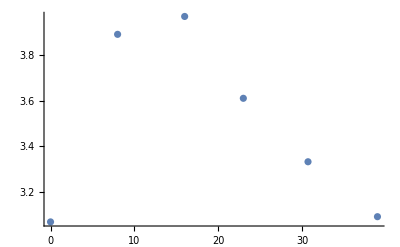

```mathematica
G0=ListPlot[Table[ID[2][[i]][[{4,5}]],{i,1,6}]]
```

```mathematica
slu1=FindFit[Table[ID[2][[i]][[{4,5}]],{i,1,6}],a*x^2+b*x+c,{a,b,c},x]
```

{a→-0.00195188,b→0.0691058,c→3.22766}

```mathematica
slu1=(a*x^2+b*x+c)/.%
```

3.22766+0.0691058 x-0.00195188 x^2

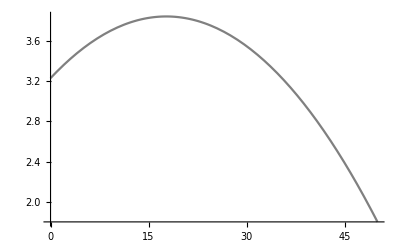

```mathematica
G1=Plot[slu1,{x,0,50},PlotStyle->Gray]
```

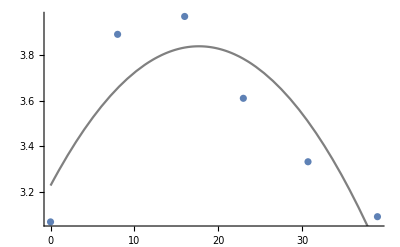

```mathematica
Show[G0,G1]
```

```mathematica
LC1={}
LC2={}
LC3={}
LC4={}
num1=0
num2=0
num3=0
num4=0
```

{}

{}

{}

«1 more identical outputs»

0

0

0

«1 more identical outputs»

```mathematica
Do[len=Length[ID[i]];
Switch[ID[i][[1,2]],
1,slu={a,b,c}/.FindFit[Table[ID[i][[j]][[{4,5}]],{j,1,len}],a*x^2+b*x+c,{a,b,c},x];LC1=AppendTo[LC1,slu];num1=num1+1,
2,slu={a,b,c}/.FindFit[Table[ID[i][[j]][[{4,5}]],{j,1,len}],a*x^2+b*x+c,{a,b,c},x];LC2=AppendTo[LC2,slu];num2=num2+1,
3,slu={a,b,c}/.FindFit[Table[ID[i][[j]][[{4,5}]],{j,1,len}],a*x^2+b*x+c,{a,b,c},x];LC3=AppendTo[LC3,slu];num3=num3+1,
4,slu={a,b,c}/.FindFit[Table[ID[i][[j]][[{4,5}]],{j,1,len}],a*x^2+b*x+c,{a,b,c},x];LC4=AppendTo[LC4,slu];num4=num4+1]
,{i,1,1313}]
```

```mathematica
LC1
```

{{0.,0.,3.7377},{-0.00144026,0.0332644,3.44758},{0.0028306,-0.0819926,3.47225},{0.000381851,-0.019038,3.9318},{0.,0.,2.7726},{0.00500244,-0.189235,4.1109},{0.00143514,-0.0131732,1.69788},{-0.0000159319,-0.0184277,3.71107},{-0.00341966,0.107748,3.0467},{-0.00156693,-0.0261901,2.4849},{-0.00238202,0.0721008,2.6741},{0.0120255,-0.203729,3.2581},{0.000602596,-0.052118,1.81073},{-0.00091661,0.00904189,3.9546},{-0.000426923,-0.0241626,2.94518},{0.00313311,-0.0654626,3.4657},{0.,0.,2.7081},{0.0000256542,-0.00986687,2.77575},{-0.00284412,0.0874529,2.02167},{0.000729607,-0.0437102,2.67246},{0.,0.,1.9459},{0.,0.,1.7918},{-0.00140065,-0.0226106,3.7257},{-0.00203534,-0.0159919,2.1972},{-0.00220049,-0.00300064,3.5553},{0.,0.,1.2528},{0.0013187,-0.0462959,3.5104},{0.0013418,-0.0367875,2.4423},{-0.00228133,0.0518413,3.3322},{0.00071953,-0.0578979,2.86162},{-0.000597869,-0.0349701,3.69475},{-0.00104627,0.0232171,3.65979},{-0.000694818,0.00434507,3.32488},{0.00190725,-0.0599782,1.85594},{0.00746195,-0.164088,2.6391},{0.000500846,-0.0322006,3.25024},{0.00244121,-0.103663,3.35109},{0.,0.,4.0431},{-0.000840581,-0.00322248,3.48378},{-0.00364028,0.130773,2.02859},{-0.00319663,0.063239,4.30054},{-0.0000772157,-0.039764,4.49449},{0.000458509,-0.0543431,3.0445},{-0.000903724,0.00933977,2.72875},{0.000568264,-0.0198811,3.20178},{0.000630747,-0.0176207,2.1972},{-0.00295941,0.105157,4.02039},{-0.000814526,0.000392492,3.70153},{0.00469261,-0.100043,3.091},{0.,0.,2.2513},{0.00144683,-0.0452622,2.41016},{-0.00190608,0.0000325096,2.8622},{-0.00571957,0.258582,1.85941},{0.000746304,-0.0530803,2.252},{0.00209645,-0.0714749,2.9863},{0.000745982,-0.0439242,3.12726},{0.00316797,0.0253438,2.0794},{0.00060682,-0.0692874,3.17232},{0.000703605,-0.0436527,4.02268},{-0.00906458,0.120992,2.2513},{-0.00610188,0.0831224,3.83921},{0.000924205,-0.0105366,2.36181},{-0.00139422,-0.00653777,2.6027},{0.000780494,-0.0312565,2.07986},{0.00267102,-0.120872,2.86545},{0.0000731926,0.00232531,3.18468},{-0.0011027,0.0151348,4.05584},{-0.00912051,-0.0429968,2.1972},{-0.00439203,0.0889363,2.4423},{0.0000859532,-0.0221203,3.9015},{0.00147028,-0.0094007,1.60858},{0.,0.,3.45},{0.0000503881,0.0103165,3.02576},{-0.000884007,-0.00961719,3.15738},{0.00108293,-0.0230666,3.56057},{0.,0.,2.9444},{0.00119658,-0.0562592,2.62073},{0.000373256,-0.0362333,3.12189},{0.00111683,-0.0659116,3.32756},{0.,0.,3.8286},{0.,0.,4.3307},{0.000915996,-0.0471602,3.59262},{7.19359×10^-18,3.99662×10^-17,2.3979},{0.00121954,0.0233455,1.5041},{1.79556×10^-18,-9.00365×10^-17,2.3979},{2.51595×10^-18,2.36358×10^-17,2.3979},{0.000541464,0.00531342,2.34492},{0.00218091,-0.0907254,2.63951},{-0.000680395,-0.0104249,3.04424},{-0.00379297,-0.0303437,1.8718},{0.00008852,-0.0237951,3.31387},{-0.0131188,-0.0993277,1.5041},{-0.000174287,-0.0133338,3.8712},{0.00174291,-0.0590902,3.03422},{0.000782418,-0.0308227,2.68209},{0.00256696,-0.0470332,3.4012},{-0.0006951,-0.0671784,1.9459},{0.00115844,0.0173767,2.2513},{0.00101536,-0.0577988,2.41852},{-0.00327152,0.0379069,2.35838},{-0.00332119,-0.0631026,2.3979},{-0.00236474,-0.00143701,2.68852},{-0.00281188,-0.0273154,2.1401},{-0.000238891,0.00745195,3.84854},{0.,0.,3.4657},{0.,0.,2.4423},{-0.0000617187,-0.0135066,3.10489},{-0.000830157,-0.0390462,3.1987},{0.,0.,1.6094},{-0.00210939,0.0118938,3.76429},{-0.0141857,0.158741,3.6889},{0.,0.,3.8395},{0.00419583,-0.128083,3.4177},{-0.000503715,-0.0169824,3.091},{-0.00216871,0.0640176,2.40584},{-0.0168416,-0.132326,2.0794},{-0.00502168,0.154607,3.12847},{-0.000661447,-0.0277552,2.64197},{0.000670257,-0.0380581,2.68398},{-0.000801924,0.00060767,3.44592},{-0.00279019,0.0854071,3.60304},{0.000223501,0.0389637,2.90764},{0.00399062,0.031925,1.7918},{-0.000446413,-0.00472744,3.34588},{0.00071222,-0.0585697,3.2581},{-0.0000555903,-0.0123563,1.87854},{0.023402,-0.555344,2.9704},{-0.000436366,0.0763431,0.708651},{0.00150542,-0.0802284,0.912807},{0.00396835,-0.0953436,3.20763},{0.000179989,-0.0300531,3.54584},{0.000525837,-0.0065354,2.66407},{0.000786918,-0.0361982,2.5649},{0.,9.81308×10^-18,0.6931},{0.00161227,-0.0785403,1.5041},{0.0010483,-0.0483416,1.15269},{0.000749678,-0.0794465,2.9627},{-0.00210032,0.0512413,2.6741},{0.000630057,-0.0540738,3.4143},{0.00230602,-0.138133,2.66888},{-0.000219851,0.0377038,3.25383},{-0.000489647,-0.0183632,3.88876},{-0.00452932,0.118478,3.48295},{-0.000562543,-0.00892029,3.541},{-0.0025746,0.0807889,3.2581},{-0.0117094,-0.0468375,2.7726},{0.000900658,-0.0481541,2.94891},{0.000158586,-0.0040458,2.92845},{-0.000218912,0.00873612,3.12808},{0.00329799,-0.077214,1.88503},{0.,0.,2.3979},{0.0017069,-0.103851,4.59368},{-0.00155323,0.0633815,4.05012},{0.,0.,0.},{-0.00372552,0.151584,0.987561},{-0.00302333,0.0694582,3.0676},{0.,0.,0.},{-0.00513834,0.0746407,2.96539},{-0.0109471,0.161916,2.4849},{-0.00051494,-0.0164045,4.5109},{-0.000105142,-0.0114855,3.31232},{0.,0.,3.3844},{-0.000367812,-0.0420628,3.8918},{-0.00193573,0.0681878,3.05196},{0.,0.,3.5695},{-0.000160726,0.00877384,3.633},{0.000544705,-0.0373069,3.5835},{-0.000353852,-0.0109326,3.03947},{0.0011019,-0.0329873,3.0445},{0.000442591,-0.0874962,2.50167},{0.000207589,-0.0452276,1.63978},{0.00806164,-0.147644,3.63385},{0.000362712,0.00590702,3.4965},{0.,0.,3.7842},{0.00229591,-0.0758025,3.15859},{0.00268457,0.0237775,2.3514},{-0.00103113,0.0436799,2.69583},{-0.000300376,0.00348905,2.77765},{-0.000987855,-0.0189104,2.8034},{-0.000123612,-0.0278998,3.75054},{0.000934587,-0.0673348,3.39889},{0.0014037,-0.0659741,2.6391},{-0.00167204,0.0534075,2.9957},{-0.00187158,0.0301607,2.65545},{0.00487441,-0.155961,2.8666},{-0.000124818,-0.0302757,3.75527},{0.00064309,-0.0528753,4.03467},{0.00184675,-0.0957448,3.64971},{0.00154974,-0.0733546,4.1564},{0.00187579,-0.0600336,2.48764},{0.000979846,-0.0279222,2.2349},{-0.000278125,-0.0446125,2.7726},{-0.000262439,0.0264115,2.28666},{-0.00473021,0.0865833,3.0445},{0.00464632,-0.205597,4.21221},{0.00120556,-0.0519934,2.78307},{0.00090443,-0.0497759,4.3074},{-0.00131936,0.0329625,3.2333},{0.00135391,0.0216625,3.5553},{-0.00016436,0.00783623,2.7791},{-0.000438846,-0.0092022,4.15116},{0.,0.,2.1401},{-0.00315855,0.079602,3.29371},{0.00206993,-0.0932694,3.37017},{0.,0.,3.7495},{-0.000993493,-0.0241488,3.3869},{-0.00127517,0.0625753,3.24065},{0.00123032,-0.025929,1.32699},{0.00123885,-0.0183565,3.6763},{0.,0.,3.5973},{0.00155622,-0.0137836,3.0445},{0.00026297,-0.0331931,3.10253},{-2.49766×10^-6,-0.0207686,3.13704},{0.00161388,-0.0907671,3.6508},{-0.00305015,0.0926943,3.33346},{0.,0.,3.5835},{-0.00292734,-0.0234188,2.7726},{0.00523865,-0.124231,3.0445},{-0.00669087,-0.054483,3.9318},{0.000713693,-0.0458605,3.23874},{-0.00359009,0.0696673,2.8332},{0.,0.,4.3438},{0.,0.,2.6741},{0.,0.,3.4012},{-0.00140206,-0.00501128,3.83777},{-0.000889816,0.0203433,3.68875},{-0.0115877,0.149048,2.07154},{0.00141339,-0.0643285,2.0794},{0.0000782313,-0.0364476,3.2958},{-0.00283845,0.024208,4.05433},{0.000801047,-0.0801014,3.95813},{-0.00294923,0.0555959,3.54764},{0.,0.,3.6889},{-0.0000309177,0.00484052,1.63527},{0.00102589,-0.0246405,3.91626},{-0.000204647,0.0183153,2.51318},{0.000325662,-0.0202678,2.98708},{0.00214569,-0.0816691,2.17705},{0.00337742,-0.121104,3.69512},{-0.00359701,0.0936022,3.3322},{0.00191053,-0.083329,3.3322},{-0.0026225,-0.026225,3.8918},{0.00226309,-0.0914719,3.8286},{0.000832881,0.013564,2.8904},{0.0199693,-0.48664,2.6741},{0.000696584,-0.0135128,1.69107},{0.000140598,-0.115134,4.08998},{-0.000816243,-0.0115827,4.37561},{0.000282203,-0.019443,3.5177},{-0.00246894,0.0500765,2.42828},{0.00115468,-0.0538203,2.3881},{-0.00602191,0.175327,2.1761},{-0.00234534,0.063682,3.7612},{0.00731014,-0.133333,3.2771},{-0.000408539,0.0244344,0.943276},{-0.00175977,0.0394552,2.77588},{0.00268214,-0.0991503,3.3142},{-0.00280969,0.09536,2.07077},{-0.00260666,0.0930054,1.73069},{-0.00148881,0.0053789,4.1109},{-0.00202796,0.0448367,3.86239},{0.,0.,0.},{-0.00520198,0.138309,3.25885},{0.00240929,-0.0771093,3.08484},{0.000797979,0.00706778,3.4012},{-0.00243661,0.0811666,2.92929},{0.00214764,-0.0702068,3.32042},{-0.00295143,0.105633,2.9957},{-0.000998333,0.0118483,3.157},{-0.00230401,0.114645,3.2387},{-0.00827568,0.0400145,2.7081},{-0.0009548,0.0257373,3.59386},{-0.00442614,0.0840966,3.0445},{0.00513601,-0.144077,1.99328},{-0.00501341,0.128858,3.11362},{-0.000462442,-0.0149706,3.98134},{0.00256043,-0.0922744,4.2627},{-0.00188143,0.0575438,2.08009},{-0.000622442,0.0269728,2.16336},{-0.00119136,0.0529305,3.24134},{0.00282904,-0.0699174,2.7726},{0.00209434,-0.0569282,2.7726},{-0.00028078,-0.00549526,3.434},{-0.000883346,0.0101289,3.33445},{0.0000619236,-0.102114,3.23607},{0.00240413,-0.103948,2.5755},{-0.00422821,0.148764,2.94516},{-0.000591018,-0.0129627,4.5074},{-0.00227801,0.00999922,3.5835},{0.00179423,-0.0746335,4.0254},{-0.00278758,0.0917935,2.0794},{-0.000550433,0.0508882,3.2387},{0.000078499,-0.00240219,3.84345},{0.000713257,-0.00904163,3.215},{0.0038386,-0.142715,2.98179},{-0.00108464,0.0390782,3.64684},{0.0000562965,-0.0892153,2.64309},{0.00182317,-0.0993694,4.1329},{-0.00133728,-0.0173846,2.3979},{-0.00034933,-0.00192893,3.64953},{0.000493046,-0.0726538,4.12159},{0.0000446361,-0.0362059,3.54649},{0.,0.,2.3979},{-0.00415302,0.126746,2.03141},{0.00252724,-0.101842,3.58294},{-0.00175959,0.0796346,3.0681},{0.00117473,-0.0661904,2.879},{-0.0029326,0.0576483,3.36588},{0.,0.,2.2513},{0.00249844,-0.111002,3.091},{-0.00265616,0.119931,2.3979},{0.000352434,-0.0576139,4.18312},{0.,0.,2.9957},{-0.00370264,0.0418693,2.95453},{-0.000474367,-0.000920195,3.5973},{-0.00827755,0.095242,2.5649},{0.00299049,-0.0660412,2.4423},{0.00078314,-0.0336631,2.8293},{-0.00185528,0.0560785,3.22669},{0.000596326,-0.0361228,3.37639},{-0.00107519,0.0081407,1.7918},{-0.00164591,0.0125181,2.87321},{-0.000369593,0.0147681,1.4303},{-0.00509239,-0.0392842,3.3142},{-0.0000661348,-0.0379691,4.81096}}

```mathematica
LC2;
```

```mathematica
LC3;
```

```mathematica
LC4;
num1
```

325

```mathematica
a1=0;b1=0;c1=0;
```

```mathematica
For[i=1,i≤num1,i++,a1=a1+LC1[[i,1]]];a1=a1/num1
```

-0.000311484

```mathematica
For[i=1,i≤num1,i++,b1=b1+LC1[[i,2]]];b1=b1/num1
```

-0.012727

```mathematica
For[i=1,i≤num1,i++,c1=c1+LC1[[i,3]]];c1=c1/num1
```

2.98502

```mathematica
HLC1=a1*x^2+b1*x
```

-0.012727 x-0.000311484 x^2

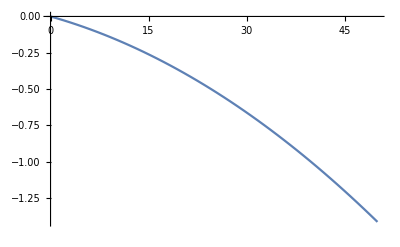

```mathematica
P1=Plot[HLC1,{x,0,50}]
```

-0.000378985

0.0000773113

2.94796

0.0000773113 x-0.000378985 x^2

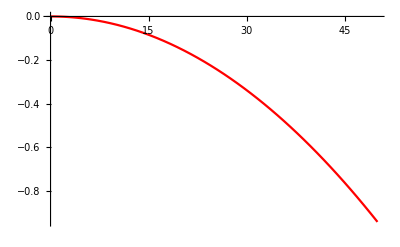

```mathematica
a2=0;b2=0;c2=0;
For[i=1,i≤num2,i++,a2=a2+LC2[[i,1]]];a2=a2/num2
For[i=1,i≤num2,i++,b2=b2+LC2[[i,2]]];b2=b2/num2
For[i=1,i≤num2,i++,c2=c2+LC2[[i,3]]];c2=c2/num2
HLC2=a2*x^2+b2*x
P2=Plot[HLC2,{x,0,50},PlotStyle->Red]
```

-0.000607097

0.0114499

2.91363

0.0114499 x-0.000607097 x^2

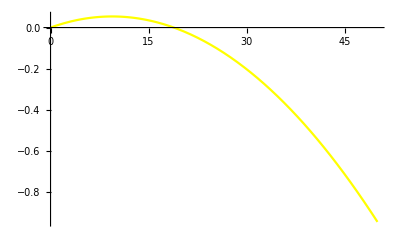

```mathematica
a3=0;b3=0;c3=0;
For[i=1,i≤num3,i++,a3=a3+LC3[[i,1]]];a3=a3/num3
For[i=1,i≤num3,i++,b3=b3+LC3[[i,2]]];b3=b3/num3
For[i=1,i≤num3,i++,c3=c3+LC3[[i,3]]];c3=c3/num3
HLC3=a3*x^2+b3*x
P3=Plot[HLC3,{x,0,50},PlotStyle->Yellow]
```

-0.000616306

0.0315555

2.86774

0.0315555 x-0.000616306 x^2

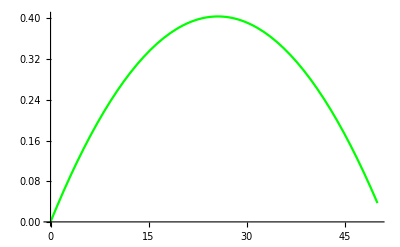

```mathematica
a4=0;b4=0;c4=0;
For[i=1,i≤num4,i++,a4=a4+LC4[[i,1]]];a4=a4/num4
For[i=1,i≤num4,i++,b4=b4+LC4[[i,2]]];b4=b4/num4
For[i=1,i≤num4,i++,c4=c4+LC4[[i,3]]];c4=c4/num4
HLC4=a4*x^2+b4*x
P4=Plot[HLC4,{x,0,50},PlotStyle->Green]
```

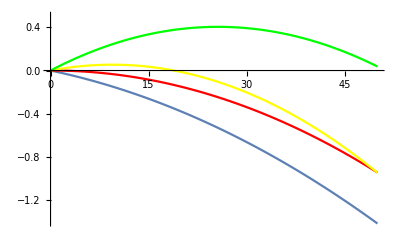

```mathematica
Show[P1,P2,P3,P4,PlotRange->{{0,50},{-1.4,0.5}}]
```